```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

Notebook load complete.

```mathematica
replSingVarPlus[e_]:=e/.Inactive[HeavisideTheta][a_]:>HeavisideTheta[a]/.PlusDistribution[a_*HeavisideTheta[1-b_]]:>HeavisideTheta[1-b-beta]a-DiracDelta[1-b-beta]Integrate[a,{b,0,b},Assumptions->0<b<1]/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{b,1,b},Assumptions->0<b<1]

$Assumptions=alphabar>0&&0<delta1<1&&0<delta2<2&&0<xa<1&&0<xb<1&&0<xi1<1&&0<xi2<1&&0<tau<1&&0<tauPerp<1&&tauPM>0&&muMS>0&&s>0&&0<z1<1&&0<z2<1&&0<delta<1

gluonSign=-1;
waveZ=1(*-Cf*alphaMS*(Gamma[eps])/(4*Pi)*)
Z2=1+Cf*alphaMS(2/eps^2+(-2*Log[(-Q^2-I*delta)/muMS^2]+3)/eps)/(4*Pi)
Z2bar=ComplexConjugate[Z2]
hardFunc=1+alphabar(-Log[sHat/muMS^2]^2+3Log[sHat/muMS^2]+7zeta2-8)

keepEpsOrderMatElemSqr=2;
```

ᾱ>0∧0<δ_1<1∧0<δ_2<2∧0<x_a<1∧0<x_b<1∧0<ξ_1<1∧0<ξ_2<1∧0<τ<1∧0<τ_⊥<1∧τ_(+-)>0∧μ_OverBar[MS]>0∧s>0∧0<z_1<1∧0<z_2<1∧0<δ<1

1

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-Q^2-ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-Q^2+ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

ᾱ (7 ζ_2-log^2((ŝ)/μ_OverBar[MS]^2)+3 log((ŝ)/μ_OverBar[MS]^2)-8)+1

```mathematica
(* integrated drell-yan kinematics *)

(* let qm = z1*p1m, qp=z2*p2p *)
applyIntDYkinematics[e_]:=e/.Vperp[p1]->Vperp[l1]/.Vperp[p2]->Vperp[l2]/.km->p1m+p2m-z1*p1m/.kp->p1p+p2p-z2*p2p/.p1p->-SPD[Vperp[p1],Vperp[p1]]/p1m/.p2m->-SPD[Vperp[p2],Vperp[p2]]/p2p/.Vperp[k]->-Vperp[Q]/.SPD[Q,Q]->tau*s/.SPD[Vperp[Q],Vperp[Q]]->QT^2/.l1->0/.l2->0/.p2m->0/.p1p->0/.s->p1m*p2p

applyDiracDeltaSimplification[e_]:=Expand[e]/.a_*myDelta[z1bar]:>(Normal@Series[a,{z1,1,0},{z1bar,0,0}])*myDelta[Z1BAR]/.a_*Inactive[DiracDelta][z2bar]:>(Normal@Series[a,{z2,1,0},{z2bar,0,0}])*myDelta[Z2BAR]/.Z1BAR->z1bar/.Z2BAR->z2bar/.a_*myDelta[QT^2]:>(Normal@Series[a/.QT->Sqrt[xyz],{xyz,0,0}])*myDelta[xyz]/.a_*myDelta[QT^2-b_]:>(a/.QT->Sqrt[b])*myDelta[QT^2-b]/.xyz->QT^2/.c_*myDelta[a_*z1bar]:> (c*myDelta[z1bar]/Abs[a])/.c_*myDelta[a_*z2bar]:> (c*myDelta[z2bar]/Abs[a])

applyDiracDeltaZ1[e_]:=e/.c_*myDelta[a_*z1-b_]:> (c/a/.z1->b/a)/.c_*myDelta[a_*z1+b_]:> (c/a/.z1->-b/a)e/.c_*myDelta[a_*z1-b_]:> (c/a/.z1->b/a)
applyDiracDeltaZ2[e_]:=e/.c_*myDelta[a_*z2-b_]:> (c/a/.z2->b/a)/.c_*myDelta[a_*z2+b_]:> (c/a/.z2->-b/a)

applyDiracDeltaKMinus[e_]:=e/.b_*myDelta[km-a_]:> (b/.km->a)/.b_*myDelta[km+a_]:> (b/.km->-a)/.b_*myDelta[km]:> (b/.km->0)
applyDiracDeltaKPlus[e_]:=e/.b_*myDelta[kp-a_]:> (b/.kp->a)/.b_*myDelta[kp+a_]:> (b/.kp->-a)
applyDiracDeltaKPerp[e_]:=e/.b_*myDelta[Vperp[k]-a_]:> (b/.Vperp[k]->a)/.b_*myDelta[Vperp[k]+a_]:> (b/.Vperp[k]->-a)

applyKsqrDiracDeltaKMinus[e_]:=e/.b_*myDelta[km*c_-a_]:> (b/c/.km->a/c)/.b_*myDelta[km*c_+a_]:> (b/c/.km->-a/c)
applyKsqrDiracDeltaKPlus[e_]:=e/.b_*myDelta[kp*c_-a_]:> (b/c/.kp->a/c)/.b_*myDelta[kp*c_+a_]:> (b/c/.kp->-a/c)

applyPlusIdentity[e_]:=e/.a_^(-1-eps)/;a==km||a==kp:>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]

applyDrellYanNotation[e_]:=e/.SPD[nb,Q]->z1*p1m/.SPD[n,Q]->z2*p2p/.SPD[Vperp[Q]]->-QT^2

removeRegulators[e_]:=e/.delta1->0/.delta2->0/.delta3->0/.delta4->0/.eta->0
applyLeadingTwistKinematics[e_]:=e/.Vperp[p1]->0/.Vperp[p2]->0/.p1p->0/.p2m->0

applyDrellYanAntennaNotation[e_]:=e/.SPD[nb,Q]->z1*(p1m+qm)/.SPD[n,Q]->z2*p2p/.SPD[Vperp[Q]]->-QT^2

simplifyDeltas[e_]:=e/.myDelta[a_*b_-a_]:>myDelta[1-b]/a
```

### QCD -- can assert that all perps are small

#### Setup

```mathematica
(* the (1/2) comes from the measure, the 2 comes from the dirac deltas *)

momConsDelta=2(1/2)myDelta[SPD[Q,n]+kp-p2p-p1p]myDelta[SPD[Q,nb]+km-p1m-p2m]myDelta[Vperp[Q]+Vperp[k]-Vperp[p1]-Vperp[p2]]

onShellDelta=2*Pi*myDelta[kp*km+SPD[Vperp[k],Vperp[k]]]*HeavisideTheta[km,kp,SPD[n,Q],SPD[nb,Q]]
```

δ[k^+-p_1^+-p_2^++Q^+] δ[k^--p_1^--p_2^-+Q^-] δ[k_⊥-p_1_⊥-p_2_⊥+Q_⊥]

2 π k^+,k^-,Q^+,Q^- δ[k^+ k^-+(k_⊥)^2]

```mathematica
matElem1Dag=-I*g*SpinorUBar[p1].((2FVD[p1,alpha]-GAD[alpha].GSD[k])/(-2SPD[p1,k])).GAD[tau].SpinorV[p2]
matElem2Dag=I*g*SpinorUBar[p1].GAD[tau].((2FVD[p2,alpha]-GSD[k].GAD[alpha])/(-2SPD[p2,k])).SpinorV[p2]

matElemDag=matElem1Dag+matElem2Dag//DiracSimplify//FCE
```

-ⅈ g ū(p_1).(-(2 p_1^α-γ^α.(γ·k))/(2 k·p_1)).γ^τ.v(p_2)

ⅈ g ū(p_1).γ^τ.(-(2 p_2^α-(γ·k).γ^α)/(2 k·p_2)).v(p_2)

(ⅈ g p_1^α φ(p_1).γ^τ.φ(p_2))/(k·p_1)-(ⅈ g p_2^α φ(p_1).γ^τ.φ(p_2))/(k·p_2)-(ⅈ g φ(p_1).γ^α.(γ·k).γ^τ.φ(p_2))/(2 k·p_1)+(ⅈ g φ(p_1).γ^τ.(γ·k).γ^α.φ(p_2))/(2 k·p_2)

```mathematica
matElem1=I*g*SpinorVBar[p2].GAD[rho].((2FVD[p1,alpha]-GSD[k].GAD[alpha])/(-2SPD[p1,k])).SpinorU[p1]
matElem2=-I*g*SpinorVBar[p2].((2FVD[p2,alpha]-GAD[alpha].GSD[k])/(-2SPD[p2,k])).GAD[rho].SpinorU[p1]

matElem=matElem1+matElem2//DiracSimplify//FCE
```

ⅈ g v̄(p_2).γ^ρ.(-(2 p_1^α-(γ·k).γ^α)/(2 k·p_1)).u(p_1)

-ⅈ g v̄(p_2).(-(2 p_2^α-γ^α.(γ·k))/(2 k·p_2)).γ^ρ.u(p_1)

-(ⅈ g p_1^α φ(p_2).γ^ρ.φ(p_1))/(k·p_1)+(ⅈ g p_2^α φ(p_2).γ^ρ.φ(p_1))/(k·p_2)-(ⅈ g φ(p_2).γ^α.(γ·k).γ^ρ.φ(p_1))/(2 k·p_2)+(ⅈ g φ(p_2).γ^ρ.(γ·k).γ^α.φ(p_1))/(2 k·p_1)

```mathematica
gluonSign(matElem/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDag/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE(* gluon sign tells whether to include the negative from gluon propagator *)

%//PhatDef//DiracSimplify//FCE
-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

trace=%/.SPD[k,k]->0//lcCompAll

temp=trace/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify

LOWmunuAvg=Series[temp/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal
```

-(γ^ρ.(γ·k).γ^τ.(γ·p_2) p_1·p_2 g^2)/(k·p_1 k·p_2)+(2 γ^ρ.(γ·p_1).γ^τ.(γ·p_2) p_1·p_2 g^2)/(k·p_1 k·p_2)+((γ·k).γ^ρ.γ^τ.(γ·p_2) p_1·p_2 g^2)/(k·p_2)^2+(D γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(2 k·p_1)-(γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(k·p_1)-(γ^ρ.(γ·p_1).γ^τ.(γ·p_2) g^2)/(k·p_1)-(D γ^ρ.γ^τ.(γ·k).(γ·p_2) g^2)/(2 k·p_2)+(2 γ^ρ.γ^τ.(γ·k).(γ·p_2) g^2)/(k·p_2)+(γ^ρ.γ^τ.(γ·p_1).(γ·p_2) g^2)/(k·p_2)+(D γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(2 k·p_2)-(2 γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(k·p_2)-(D (γ·p_1).(γ·k).γ^τ.(γ·p_2) k^ρ g^2)/(2 k·p_1 k·p_2)+(2 (γ·p_1).(γ·k).γ^τ.(γ·p_2) k^ρ g^2)/(k·p_1 k·p_2)+(D γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(2 k·p_1 k·p_2)-(2 γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(k·p_1 k·p_2)+((γ·k).(γ·p_1).γ^τ.(γ·p_2) p_1^ρ g^2)/(k·p_1 k·p_2)-(γ^ρ.(γ·k).(γ·p_1).(γ·p_2) p_1^τ g^2)/(k·p_1 k·p_2)+(γ^ρ.(γ·k).(γ·p_1).(γ·p_2) p_2^τ g^2)/(k·p_1 k·p_2)+(γ^ρ.(γ·p_1).(γ·k).(γ·p_2) p_2^τ g^2)/(k·p_1 k·p_2)-(γ^ρ.γ^τ.(γ·p_1).(γ·p_2) k^2 g^2)/(2 k·p_1 k·p_2)-(D γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(2 k·p_1 k·p_2)+(2 γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(k·p_1 k·p_2)-((γ·p_1).γ^ρ.γ^τ.(γ·p_2) k^2 g^2)/(2 k·p_1 k·p_2)-(D γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(4 (k·p_1)^2)+(γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(2 (k·p_1)^2)+(γ^τ.(γ·p_1).(γ·k).(γ·p_2) k^ρ g^2)/(k·p_2)^2+(D (γ·p_1).γ^τ.(γ·k).(γ·p_2) k^ρ g^2)/(2 (k·p_2)^2)-(2 (γ·p_1).γ^τ.(γ·k).(γ·p_2) k^ρ g^2)/(k·p_2)^2+(D γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(2 (k·p_2)^2)-(2 γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(k·p_2)^2+((γ·p_1).γ^ρ.(γ·k).(γ·p_2) k^τ g^2)/(k·p_2)^2-((γ·k).(γ·p_1).γ^τ.(γ·p_2) p_2^ρ g^2)/(k·p_2)^2-((γ·k).γ^ρ.(γ·p_1).(γ·p_2) p_2^τ g^2)/(k·p_2)^2-(D γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(4 (k·p_2)^2)+(γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(k·p_2)^2-(γ^τ.(γ·p_1).γ^ρ.(γ·p_2) k^2 g^2)/(2 (k·p_2)^2)-(D γ^ρ.γ^τ.(γ·k).(γ·p_2) k·p_1 g^2)/(2 (k·p_2)^2)+(2 γ^ρ.γ^τ.(γ·k).(γ·p_2) k·p_1 g^2)/(k·p_2)^2-(γ^τ.γ^ρ.(γ·k).(γ·p_2) k·p_1 g^2)/(k·p_2)^2

-(γ^ρ.(γ·k).γ^τ.(γ·p_2) p_1·p_2 g^2)/(k·p_1 k·p_2)+(2 γ^ρ.(γ·p_1).γ^τ.(γ·p_2) p_1·p_2 g^2)/(k·p_1 k·p_2)+((γ·k).γ^ρ.γ^τ.(γ·p_2) p_1·p_2 g^2)/(k·p_2)^2+(D γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(2 k·p_1)-(γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(k·p_1)-(γ^ρ.(γ·p_1).γ^τ.(γ·p_2) g^2)/(k·p_1)-(D γ^ρ.γ^τ.(γ·k).(γ·p_2) g^2)/(2 k·p_2)+(2 γ^ρ.γ^τ.(γ·k).(γ·p_2) g^2)/(k·p_2)+(γ^ρ.γ^τ.(γ·p_1).(γ·p_2) g^2)/(k·p_2)+(D γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(2 k·p_2)-(2 γ^ρ.(γ·k).γ^τ.(γ·p_2) g^2)/(k·p_2)-(D (γ·p_1).(γ·k).γ^τ.(γ·p_2) k^ρ g^2)/(2 k·p_1 k·p_2)+(2 (γ·p_1).(γ·k).γ^τ.(γ·p_2) k^ρ g^2)/(k·p_1 k·p_2)+(D γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(2 k·p_1 k·p_2)-(2 γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(k·p_1 k·p_2)+((γ·k).(γ·p_1).γ^τ.(γ·p_2) p_1^ρ g^2)/(k·p_1 k·p_2)-(γ^ρ.(γ·k).(γ·p_1).(γ·p_2) p_1^τ g^2)/(k·p_1 k·p_2)+(γ^ρ.(γ·k).(γ·p_1).(γ·p_2) p_2^τ g^2)/(k·p_1 k·p_2)+(γ^ρ.(γ·p_1).(γ·k).(γ·p_2) p_2^τ g^2)/(k·p_1 k·p_2)-(γ^ρ.γ^τ.(γ·p_1).(γ·p_2) k^2 g^2)/(2 k·p_1 k·p_2)-(D γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(2 k·p_1 k·p_2)+(2 γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(k·p_1 k·p_2)-((γ·p_1).γ^ρ.γ^τ.(γ·p_2) k^2 g^2)/(2 k·p_1 k·p_2)-(D γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(4 (k·p_1)^2)+(γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(2 (k·p_1)^2)+(γ^τ.(γ·p_1).(γ·k).(γ·p_2) k^ρ g^2)/(k·p_2)^2+(D (γ·p_1).γ^τ.(γ·k).(γ·p_2) k^ρ g^2)/(2 (k·p_2)^2)-(2 (γ·p_1).γ^τ.(γ·k).(γ·p_2) k^ρ g^2)/(k·p_2)^2+(D γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(2 (k·p_2)^2)-(2 γ^ρ.(γ·p_1).(γ·k).(γ·p_2) k^τ g^2)/(k·p_2)^2+((γ·p_1).γ^ρ.(γ·k).(γ·p_2) k^τ g^2)/(k·p_2)^2-((γ·k).(γ·p_1).γ^τ.(γ·p_2) p_2^ρ g^2)/(k·p_2)^2-((γ·k).γ^ρ.(γ·p_1).(γ·p_2) p_2^τ g^2)/(k·p_2)^2-(D γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(4 (k·p_2)^2)+(γ^ρ.(γ·p_1).γ^τ.(γ·p_2) k^2 g^2)/(k·p_2)^2-(γ^τ.(γ·p_1).γ^ρ.(γ·p_2) k^2 g^2)/(2 (k·p_2)^2)-(D γ^ρ.γ^τ.(γ·k).(γ·p_2) k·p_1 g^2)/(2 (k·p_2)^2)+(2 γ^ρ.γ^τ.(γ·k).(γ·p_2) k·p_1 g^2)/(k·p_2)^2-(γ^τ.γ^ρ.(γ·k).(γ·p_2) k·p_1 g^2)/(k·p_2)^2

-1/4 C_F ((4 k·p_1 (k^τ p_2^ρ-k^ρ p_2^τ-g^ρτ k·p_2) g^2)/(k·p_2)^2+(2 D (k^τ p_2^ρ+k^ρ p_2^τ-g^ρτ k·p_2) g^2)/(k·p_1)-(4 (k^τ p_2^ρ+k^ρ p_2^τ-g^ρτ k·p_2) g^2)/(k·p_1)+(2 D (k^τ p_2^ρ+k^ρ p_2^τ-g^ρτ k·p_2) g^2)/(k·p_2)-(8 (k^τ p_2^ρ+k^ρ p_2^τ-g^ρτ k·p_2) g^2)/(k·p_2)-(2 D (k^τ p_2^ρ-k^ρ p_2^τ+g^ρτ k·p_2) g^2)/(k·p_2)+(8 (k^τ p_2^ρ-k^ρ p_2^τ+g^ρτ k·p_2) g^2)/(k·p_2)-(2 D k·p_1 (k^τ p_2^ρ-k^ρ p_2^τ+g^ρτ k·p_2) g^2)/(k·p_2)^2+(8 k·p_1 (k^τ p_2^ρ-k^ρ p_2^τ+g^ρτ k·p_2) g^2)/(k·p_2)^2-(4 (k^τ p_2^ρ-k^ρ p_2^τ-g^ρτ k·p_2) p_1·p_2 g^2)/(k·p_2)^2-(4 (k^τ p_2^ρ+k^ρ p_2^τ-g^ρτ k·p_2) p_1·p_2 g^2)/(k·p_1 k·p_2)-(4 k^τ (p_2^ρ k·p_1-p_1^ρ k·p_2-k^ρ p_1·p_2) g^2)/(k·p_2)^2+(4 p_2^τ (p_2^ρ k·p_1-p_1^ρ k·p_2-k^ρ p_1·p_2) g^2)/(k·p_2)^2+(2 D k^τ (p_2^ρ k·p_1+p_1^ρ k·p_2-k^ρ p_1·p_2) g^2)/(k·p_1 k·p_2)-(8 k^τ (p_2^ρ k·p_1+p_1^ρ k·p_2-k^ρ p_1·p_2) g^2)/(k·p_1 k·p_2)+(4 p_2^τ (p_2^ρ k·p_1+p_1^ρ k·p_2-k^ρ p_1·p_2) g^2)/(k·p_1 k·p_2)+(2 D k^τ (p_2^ρ k·p_1+p_1^ρ k·p_2-k^ρ p_1·p_2) g^2)/(k·p_2)^2-(8 k^τ (p_2^ρ k·p_1+p_1^ρ k·p_2-k^ρ p_1·p_2) g^2)/(k·p_2)^2-(4 p_1^τ (p_2^ρ k·p_1-p_1^ρ k·p_2+k^ρ p_1·p_2) g^2)/(k·p_1 k·p_2)+(4 p_2^τ (p_2^ρ k·p_1-p_1^ρ k·p_2+k^ρ p_1·p_2) g^2)/(k·p_1 k·p_2)-(2 D k^ρ (p_2^τ k·p_1-p_1^τ k·p_2-k^τ p_1·p_2) g^2)/(k·p_2)^2+(8 k^ρ (p_2^τ k·p_1-p_1^τ k·p_2-k^τ p_1·p_2) g^2)/(k·p_2)^2+(4 p_1^ρ (p_2^τ k·p_1+p_1^τ k·p_2-k^τ p_1·p_2) g^2)/(k·p_1 k·p_2)+(4 k^ρ (p_2^τ k·p_1+p_1^τ k·p_2-k^τ p_1·p_2) g^2)/(k·p_2)^2-(4 p_2^ρ (p_2^τ k·p_1+p_1^τ k·p_2-k^τ p_1·p_2) g^2)/(k·p_2)^2-(2 D k^ρ (p_2^τ k·p_1-p_1^τ k·p_2+k^τ p_1·p_2) g^2)/(k·p_1 k·p_2)+(8 k^ρ (p_2^τ k·p_1-p_1^τ k·p_2+k^τ p_1·p_2) g^2)/(k·p_1 k·p_2)+(2 k^2 (p_1^τ p_2^ρ-p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_1 k·p_2)+(8 p_1·p_2 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_1 k·p_2)-(4 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_1)-(2 D k^2 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_1 k·p_2)+(8 k^2 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_1 k·p_2)-(D k^2 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_1)^2+(2 k^2 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_1)^2-(D k^2 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_2)^2+(2 k^2 (p_1^τ p_2^ρ+p_1^ρ p_2^τ-g^ρτ p_1·p_2) g^2)/(k·p_2)^2-(2 k^2 (p_1^τ p_2^ρ-p_1^ρ p_2^τ+g^ρτ p_1·p_2) g^2)/(k·p_1 k·p_2)+(4 (p_1^τ p_2^ρ-p_1^ρ p_2^τ+g^ρτ p_1·p_2) g^2)/(k·p_2))

-1/4 C_F ((4 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2+1/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)2 D (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)+((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2-1/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)4 (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)+((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2+1/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)2 D (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)+((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2-1/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)8 (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)+((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2-1/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)2 D (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)+g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2+1/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)8 (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)+g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2-(2 D (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)+g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2+(8 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)+g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2-(4 (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2-(4 (((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)+((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(8 (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥) (((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)+((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))-1/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)4 (((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)+((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)-g^ρτ (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2+1/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)4 (((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)+g^ρτ (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2-(4 ((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2+(4 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2+(2 D ((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))-(8 ((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(4 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(2 D ((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2-(8 ((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2-(4 ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(4 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))-(2 D ((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2+(8 ((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2+(4 ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-) (((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(4 ((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2-(4 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-) (((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)^2-(2 D ((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(8 ((k_⊥)^ρ+((n̄)^ρ k^+)/2+(n^ρ k^-)/2) (((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-) (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+((k_⊥)^τ+((n̄)^τ k^+)/2+(n^τ k^-)/2) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)) g^2)/((1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥) (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)))

-1/4 C_F g^2 (-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))+(D (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-(4 (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+(2 (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)D (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)4 (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-(2 (2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+(2 (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)D (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)4 (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))+(2 (2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-(D (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)+(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+(4 (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)+(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-(2 (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+1/(k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)D ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/(k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)2 ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)D ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)4 ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)D ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)4 ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)D (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)4 (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+(4 (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) ((2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-1/(k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)2 ((2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)2 ((2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥)))

1/(8 π)C_F ϵ ((2 (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-(2 (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)+(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+1/(k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)2 ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)2 ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)2 ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))) g^2+1/(8 π)C_F (1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))-(2 (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+(2 (2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-(2 (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) ((2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-(2 (2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-) ((2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-) (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)+(2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)-(2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥))+1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/((k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)^2)2 (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))+(2 (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))-1/(k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)2 ((2 (k_⊥)^τ+(n̄)^τ k^++n^τ k^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (k_⊥)^ρ+(n̄)^ρ k^++n^ρ k^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-(4 (p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) ((2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥)))/((k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥) (k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥))+1/(k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)2 ((2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)+(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)-(p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))-1/(k^- p_2^++k^+ p_2^-+2 k_⊥·p_2_⊥)2 ((2 (p_1_⊥)^τ+(n̄)^τ p_1^++n^τ p_1^-) (2 (p_2_⊥)^ρ+(n̄)^ρ p_2^++n^ρ p_2^-)-(2 (p_1_⊥)^ρ+(n̄)^ρ p_1^++n^ρ p_1^-) (2 (p_2_⊥)^τ+(n̄)^τ p_2^++n^τ p_2^-)+(p_2^+ p_1^-+p_1^+ p_2^-+2 p_1_⊥·p_2_⊥) (n^τ (n̄)^ρ+n^ρ (n̄)^τ+2 (g^ρτ)_⊥))) g^2

#### Soft Limit

```mathematica
(* now take the soft limit *)
yuh/.myDelta[p2p-SPD[k,n]-SPD[Q,n]]->myDelta[p2p-SPD[Q,n]]-kp*D[myDelta[p2p-SPD[Q,n]],{p2p,1}]/.myDelta[p1m-SPD[k,nb]-SPD[Q,nb]]->myDelta[p1m-SPD[Q,nb]]-km*D[myDelta[p1m-SPD[Q,nb]],{p1m,1}]
%//Expand

Series[%,{QT,0,2}]//Normal
%/.kp->QT^2/km
%(*/.kp->lambda*kp*)/.QT->lambda*QT
ser=Series[%,{lambda,0,2}]//Normal
```

yuh

yuh

yuh

«3 more identical outputs»

```mathematica
Collect2[ser,lambda,QT]
(*Series[%,{eps,0,0}]//Normal*)
%/.myDelta[p1m-SPD[nb,Q]]->myDelta[z1bar]/p1m/.myDelta[p2p-SPD[n,Q]]->myDelta[z2bar]/p2p
%//Expand//applyDerivDiracDeltaP1//applyDerivDiracDeltaP2
%/.myDelta[p1m-SPD[nb,Q]]->myDelta[z1bar]/p1m/.myDelta[p2p-SPD[n,Q]]->myDelta[z2bar]/p2p
```

yuh

yuh

applyDerivDiracDeltaP2(applyDerivDiracDeltaP1(yuh))

applyDerivDiracDeltaP2(applyDerivDiracDeltaP1(yuh))

#### QCD LO Result

```mathematica
LOWmunuAvg//applyLeadingTwistKinematics;
%/.FVD[Vperp[k],a_]:> -FVD[Vperp[Q],a];
%/.FVD[Vperp[Q],a_]:>FVD[Q,a]-SPD[Q,nb]FVD[n,a]-SPD[Q,n]FVD[nb,a]//FullSimplify//applyDrellYanNotation

%/.FVD[Q,_]->0/.kp*km->QT^2/. 1/(kp*km)->1/QT^2/. 1/(p2p*p1m)->1/sHat//Simplify
```

-1/(2 π k^+ k^- p_2^+ p_1^-)g^2 C_F (((k^-)^2 (p_2^+)^2 (ϵ-1)+2 k^- p_1^- p_2^+ (k^+ ϵ+p_2^+)+(p_1^-)^2 (2 k^+ p_2^++(k^+)^2 (ϵ-1)-2 (p_2^+)^2)) (g^ρτ)_⊥+(n̄)^ρ (n^τ (p_1^- (k^- p_2^+ ϵ (k^++p_2^+ z_2)-p_2^+ p_1^- z_2 (k^+ (ϵ-1)+p_2^+))+p_2^+ p_1^- z_1 (p_1^- (k^+ ϵ+4 p_2^+ z_2 ϵ-p_2^+)-k^- p_2^+ (ϵ-1)))+p_2^+ Q^τ (p_1^- (p_2^+-ϵ (k^++4 p_2^+ z_2))+k^- p_2^+ (ϵ-1)))-k^+ (p_1^-)^2 n^τ Q^ρ+k^+ (p_1^-)^2 ϵ n^τ Q^ρ-k^- p_2^+ p_1^- ϵ n^τ Q^ρ+(n̄)^τ (n^ρ (p_1^- (k^- p_2^+ ϵ (k^++p_2^+ z_2)-p_2^+ p_1^- z_2 (k^+ (ϵ-1)+p_2^+))+p_2^+ p_1^- z_1 (p_1^- (k^+ ϵ+4 p_2^+ z_2 ϵ-p_2^+)-k^- p_2^+ (ϵ-1)))+p_2^+ (n̄)^ρ (2 p_2^+ p_1^- z_2 (k^+ ϵ+2 p_2^+ z_2 ϵ-p_2^+)-k^- p_2^+ (ϵ-1) (k^++2 p_2^+ z_2))+p_2^+ Q^ρ (p_1^- (p_2^+-ϵ (k^++4 p_2^+ z_2))+k^- p_2^+ (ϵ-1)))-k^+ (p_1^-)^2 n^ρ Q^τ+k^+ (p_1^-)^2 ϵ n^ρ Q^τ-k^- p_2^+ p_1^- ϵ n^ρ Q^τ+k^+ k^- (p_1^-)^2 n^ρ n^τ+2 k^+ (p_1^-)^3 z_1 n^ρ n^τ-2 k^+ (p_1^-)^3 z_1 ϵ n^ρ n^τ+2 k^- p_2^+ (p_1^-)^2 z_1 ϵ n^ρ n^τ-k^+ k^- (p_1^-)^2 ϵ n^ρ n^τ+p_2^+ (p_1^-)^2 n^τ Q^ρ-4 p_2^+ (p_1^-)^2 z_1 ϵ n^τ Q^ρ+p_2^+ (p_1^-)^2 n^ρ Q^τ-4 p_2^+ (p_1^-)^2 z_1 ϵ n^ρ Q^τ-2 p_2^+ (p_1^-)^3 z_1 n^ρ n^τ+4 p_2^+ (p_1^-)^3 z_1^2 ϵ n^ρ n^τ+4 p_2^+ p_1^- ϵ Q^ρ Q^τ)

1/(2 π ŝ Q_T^2)g^2 C_F (-((k^-)^2 (p_2^+)^2 (ϵ-1)+2 k^- p_1^- p_2^+ (k^+ ϵ+p_2^+)+(p_1^-)^2 (2 k^+ p_2^++(k^+)^2 (ϵ-1)-2 (p_2^+)^2)) (g^ρτ)_⊥+p_2^+ (n̄)^ρ (p_2^+ (n̄)^τ (k^+ (k^- (ϵ-1)-2 p_1^- z_2 ϵ)+2 p_2^+ z_2 (k^- (ϵ-1)+p_1^- (1-2 z_2 ϵ)))-p_1^- n^τ (k^+ (k^- ϵ+p_1^- (z_2 (-ϵ)+z_1 ϵ+z_2))+p_2^+ (k^- (z_1 (-ϵ)+z_2 ϵ+z_1)+p_1^- (4 z_2 z_1 ϵ-z_1-z_2))))+p_1^- (-n^ρ) (p_1^- n^τ (2 k^- p_2^+ z_1 ϵ-2 k^+ p_1^- z_1 (ϵ-1)+4 p_2^+ p_1^- z_1^2 ϵ-2 p_2^+ p_1^- z_1-ϵ Q_T^2+Q_T^2)+p_2^+ (n̄)^τ (k^+ (k^- ϵ+p_1^- (z_2 (-ϵ)+z_1 ϵ+z_2))+p_2^+ (k^- (z_1 (-ϵ)+z_2 ϵ+z_1)+p_1^- (4 z_2 z_1 ϵ-z_1-z_2)))))

```mathematica
Collect2[%,FVD[_,_]]
```

-1/(2 π ŝ Q_T^2)g^2 p_2^+ p_1^- C_F n^τ (n̄)^ρ (-k^- p_2^+ z_1 ϵ+k^- p_2^+ z_2 ϵ+k^+ p_1^- z_1 ϵ-k^+ p_1^- z_2 ϵ+k^- p_2^+ z_1+k^+ p_1^- z_2+k^+ k^- ϵ+4 p_2^+ p_1^- z_1 z_2 ϵ-p_2^+ p_1^- z_1-p_2^+ p_1^- z_2)-1/(2 π ŝ Q_T^2)g^2 p_2^+ p_1^- C_F n^ρ (n̄)^τ (-k^- p_2^+ z_1 ϵ+k^- p_2^+ z_2 ϵ+k^+ p_1^- z_1 ϵ-k^+ p_1^- z_2 ϵ+k^- p_2^+ z_1+k^+ p_1^- z_2+k^+ k^- ϵ+4 p_2^+ p_1^- z_1 z_2 ϵ-p_2^+ p_1^- z_1-p_2^+ p_1^- z_2)+(g^2 (p_1^-)^2 C_F n^ρ n^τ (-2 k^- p_2^+ z_1 ϵ+2 k^+ p_1^- z_1 ϵ-2 k^+ p_1^- z_1-4 p_2^+ p_1^- z_1^2 ϵ+2 p_2^+ p_1^- z_1+ϵ Q_T^2-Q_T^2))/(2 π ŝ Q_T^2)+(g^2 (p_2^+)^2 C_F (n̄)^ρ (n̄)^τ (2 k^- p_2^+ z_2 ϵ-2 k^+ p_1^- z_2 ϵ-2 k^- p_2^+ z_2+k^+ k^- ϵ-k^+ k^--4 p_2^+ p_1^- z_2^2 ϵ+2 p_2^+ p_1^- z_2))/(2 π ŝ Q_T^2)-1/(2 π ŝ Q_T^2)g^2 C_F ((k^-)^2 (p_2^+)^2 ϵ+2 k^+ k^- p_1^- p_2^+ ϵ+(k^+)^2 (p_1^-)^2 ϵ-(k^-)^2 (p_2^+)^2+2 k^- p_1^- (p_2^+)^2+2 k^+ (p_1^-)^2 p_2^+-(k^+)^2 (p_1^-)^2-2 (p_1^-)^2 (p_2^+)^2) (g^ρτ)_⊥

#### QCD Longitudinal Calculation -- normal delta usage

```mathematica
LOWmunuAvg*onShellDelta*momConsDelta*(kp*km)^-eps/8/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%//applyLeadingTwistKinematics//applyDrellYanNotation//Simplify

%//applyDiracDeltaKPlus;
%//applyDiracDeltaKPerp;
nowWeHave=%//applyDiracDeltaKMinus
```

-1/(p_2^+ p_1^-)ᾱ (k^+ k^-)^(-ϵ-1) μ_OverBar[MS]^(2 ϵ) k^+,k^-,z_2 p_2^+,z_1 p_1^- δ[k^+ k^-+(k_⊥)^2] (-(k^-)^2 (p_2^+)^2 (g^ρτ)_⊥+2 k^- p_1^- (p_2^+)^2 (g^ρτ)_⊥+2 k^+ (p_1^-)^2 p_2^+ (g^ρτ)_⊥-(k^+)^2 (p_1^-)^2 (g^ρτ)_⊥+(k^-)^2 (p_2^+)^2 ϵ (g^ρτ)_⊥+2 k^+ k^- p_1^- p_2^+ ϵ (g^ρτ)_⊥+(k^+)^2 (p_1^-)^2 ϵ (g^ρτ)_⊥-2 (p_1^-)^2 (p_2^+)^2 (g^ρτ)_⊥+p_2^+ (n̄)^ρ (k^+ k^- p_1^- ϵ n^τ+(p_1^- (k^+ ϵ-p_2^+)-k^- p_2^+ (ϵ-1)) (k_⊥)^τ)-(p_1^-)^2 p_2^+ n^τ (k_⊥)^ρ+k^+ (p_1^-)^2 n^τ (k_⊥)^ρ+k^- p_1^- p_2^+ ϵ n^τ (k_⊥)^ρ-k^+ (p_1^-)^2 ϵ n^τ (k_⊥)^ρ+p_2^+ (n̄)^τ (k^+ k^- (p_1^- ϵ n^ρ-p_2^+ (ϵ-1) (n̄)^ρ)+(p_1^- (k^+ ϵ-p_2^+)-k^- p_2^+ (ϵ-1)) (k_⊥)^ρ)-(p_1^-)^2 p_2^+ n^ρ (k_⊥)^τ+k^+ (p_1^-)^2 n^ρ (k_⊥)^τ+k^- p_1^- p_2^+ ϵ n^ρ (k_⊥)^τ-k^+ (p_1^-)^2 ϵ n^ρ (k_⊥)^τ+k^+ k^- (p_1^-)^2 n^ρ n^τ-k^+ k^- (p_1^-)^2 ϵ n^ρ n^τ+4 p_1^- p_2^+ ϵ (k_⊥)^ρ (k_⊥)^τ) δ[k^++p_2^+ (z_2-1)] δ[k^-+p_1^- (z_1-1)] δ[k_⊥+Q_⊥]

-1/(p_2^+ p_1^-)ᾱ μ_OverBar[MS]^(2 ϵ) (p_2^+ p_1^- (z_1-1) (z_2-1))^(-ϵ-1) -(z_2-1) p_2^+,z_2 p_2^+,-(z_1-1) p_1^-,z_1 p_1^- (-2 (p_2^+)^2 (p_1^-)^2 (g^ρτ)_⊥-(p_2^+)^2 (p_1^-)^2 (z_1-1)^2 (g^ρτ)_⊥-(p_2^+)^2 (p_1^-)^2 (z_2-1)^2 (g^ρτ)_⊥-2 (p_2^+)^2 (p_1^-)^2 (z_1-1) (g^ρτ)_⊥-2 (p_2^+)^2 (p_1^-)^2 (z_2-1) (g^ρτ)_⊥+(p_2^+)^2 (p_1^-)^2 (z_1-1)^2 ϵ (g^ρτ)_⊥+(p_2^+)^2 (p_1^-)^2 (z_2-1)^2 ϵ (g^ρτ)_⊥+2 (p_2^+)^2 (p_1^-)^2 (z_1-1) (z_2-1) ϵ (g^ρτ)_⊥+p_2^+ (n̄)^ρ (p_2^+ (p_1^-)^2 (z_1-1) (z_2-1) ϵ n^τ-(p_2^+ p_1^- (z_1-1) (ϵ-1)+p_1^- (p_2^+ (-(z_2-1)) ϵ-p_2^+)) (Q_⊥)^τ)+p_2^+ (p_1^-)^2 n^τ (Q_⊥)^ρ+p_2^+ (p_1^-)^2 (z_2-1) n^τ (Q_⊥)^ρ+p_2^+ (p_1^-)^2 (z_1-1) ϵ n^τ (Q_⊥)^ρ-p_2^+ (p_1^-)^2 (z_2-1) ϵ n^τ (Q_⊥)^ρ+p_2^+ (n̄)^τ (p_2^+ p_1^- (z_1-1) (z_2-1) (p_1^- ϵ n^ρ-p_2^+ (ϵ-1) (n̄)^ρ)-(p_2^+ p_1^- (z_1-1) (ϵ-1)+p_1^- (p_2^+ (-(z_2-1)) ϵ-p_2^+)) (Q_⊥)^ρ)+p_2^+ (p_1^-)^2 n^ρ (Q_⊥)^τ+p_2^+ (p_1^-)^2 (z_2-1) n^ρ (Q_⊥)^τ+p_2^+ (p_1^-)^2 (z_1-1) ϵ n^ρ (Q_⊥)^τ-p_2^+ (p_1^-)^2 (z_2-1) ϵ n^ρ (Q_⊥)^τ+p_2^+ (p_1^-)^3 (z_1-1) (z_2-1) n^ρ n^τ-p_2^+ (p_1^-)^3 (z_1-1) (z_2-1) ϵ n^ρ n^τ+4 p_2^+ p_1^- ϵ (Q_⊥)^ρ (Q_⊥)^τ) δ[p_2^+ p_1^- (z_1-1) (z_2-1)+(Q_⊥)^2]

```mathematica
nowWeHave/.MTD[___]->0/.eps->0/.HeavisideTheta[___]->1/.z1-1->-z1bar/.z2-1->-z2bar
%/.FVD[Vperp[Q],a_]:>FVD[Q,mu]-SPD[Q,nb]FVD[n,a]-SPD[Q,n]FVD[nb,a]//FullSimplify//applyDrellYanNotation
%//.myDelta[c_/a_-b_]:>a*myDelta[c-a*b]
%/.p1m/p2p->p1m^2/sHat//FullSimplify
simpl=%/.p1m*p2p->sHat
simpl/.FVD[Q,_]->0/.QT^2->sHat*z1bar*z2bar/.myDelta[_]->1/.z1bar->1-z1/.z2bar->1-z2//FullSimplify
%/. 1/p2p->p1m/sHat/. 1/p1m->p2p/sHat//FullSimplify
normalWay=Collect2[%/.p1m*p2p->sHat,FVD[_,_]]/.p1m*p2p->sHat
```

-1/((z̄)_1 (z̄)_2 (p_2^+)^2 (p_1^-)^2)ᾱ (-(z̄)_2 p_2^+ (p_1^-)^2 n^τ (Q_⊥)^ρ+p_2^+ (p_1^-)^2 n^τ (Q_⊥)^ρ-(z̄)_2 p_2^+ (p_1^-)^2 n^ρ (Q_⊥)^τ+p_2^+ (p_1^-)^2 n^ρ (Q_⊥)^τ+(z̄)_1 (z̄)_2 p_2^+ (p_1^-)^3 n^ρ n^τ-p_2^+ (n̄)^ρ ((z̄)_1 p_2^+ p_1^--p_2^+ p_1^-) (Q_⊥)^τ+p_2^+ (n̄)^τ ((z̄)_1 (z̄)_2 (p_2^+)^2 p_1^- (n̄)^ρ-((z̄)_1 p_2^+ p_1^--p_2^+ p_1^-) (Q_⊥)^ρ)) δ[(z̄)_1 (z̄)_2 p_2^+ p_1^-+(Q_⊥)^2]

1/((z̄)_1 (z̄)_2 p_2^+ p_1^-)ᾱ ((n̄)^ρ (n^τ (((z̄)_1-1) p_2^+ p_1^- (-z_1)-((z̄)_2-1) p_2^+ p_1^- z_2)-p_2^+ (n̄)^τ (2 ((z̄)_1-1) p_2^+ z_2+(z̄)_1 (z̄)_2 p_2^+)+((z̄)_1-1) p_2^+ Q^μ)+(n̄)^τ (((z̄)_1-1) p_2^+ (Q^μ-p_1^- z_1 n^ρ)-((z̄)_2-1) p_2^+ p_1^- z_2 n^ρ)+p_1^- (((z̄)_2-1) n^τ Q^μ+n^ρ (((z̄)_2-1) Q^μ-n^τ (2 ((z̄)_2-1) p_1^- z_1+(z̄)_1 (z̄)_2 p_1^-)))) δ[(z̄)_1 (z̄)_2 p_2^+ p_1^--Q_T^2]

1/((z̄)_1 (z̄)_2 p_2^+ p_1^-)ᾱ ((n̄)^ρ (n^τ (((z̄)_1-1) p_2^+ p_1^- (-z_1)-((z̄)_2-1) p_2^+ p_1^- z_2)-p_2^+ (n̄)^τ (2 ((z̄)_1-1) p_2^+ z_2+(z̄)_1 (z̄)_2 p_2^+)+((z̄)_1-1) p_2^+ Q^μ)+(n̄)^τ (((z̄)_1-1) p_2^+ (Q^μ-p_1^- z_1 n^ρ)-((z̄)_2-1) p_2^+ p_1^- z_2 n^ρ)+p_1^- (((z̄)_2-1) n^τ Q^μ+n^ρ (((z̄)_2-1) Q^μ-n^τ (2 ((z̄)_2-1) p_1^- z_1+(z̄)_1 (z̄)_2 p_1^-)))) δ[(z̄)_1 (z̄)_2 p_2^+ p_1^--Q_T^2]

1/((z̄)_1 (z̄)_2 p_2^+ p_1^-)ᾱ (p_1^- (((z̄)_2-1) Q^μ (n^τ+n^ρ)-p_2^+ (((z̄)_1-1) z_1+((z̄)_2-1) z_2) (n^τ (n̄)^ρ+n^ρ (n̄)^τ))+(p_1^-)^2 n^ρ n^τ (-(2 ((z̄)_2-1) z_1+(z̄)_1 (z̄)_2))+p_2^+ (((z̄)_1-1) Q^μ ((n̄)^ρ+(n̄)^τ)-p_2^+ (n̄)^ρ (n̄)^τ (2 ((z̄)_1-1) z_2+(z̄)_1 (z̄)_2))) δ[(z̄)_1 (z̄)_2 p_2^+ p_1^--Q_T^2]

1/((z̄)_1 (z̄)_2 p_2^+ p_1^-)ᾱ (p_1^- (((z̄)_2-1) Q^μ (n^τ+n^ρ)-p_2^+ (((z̄)_1-1) z_1+((z̄)_2-1) z_2) (n^τ (n̄)^ρ+n^ρ (n̄)^τ))+(p_1^-)^2 n^ρ n^τ (-(2 ((z̄)_2-1) z_1+(z̄)_1 (z̄)_2))+p_2^+ (((z̄)_1-1) Q^μ ((n̄)^ρ+(n̄)^τ)-p_2^+ (n̄)^ρ (n̄)^τ (2 ((z̄)_1-1) z_2+(z̄)_1 (z̄)_2))) δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]

(ᾱ (p_1^- p_2^+ (z_1^2+z_2^2) (n^τ (n̄)^ρ+n^ρ (n̄)^τ)+(p_1^-)^2 (z_2 z_1+z_1+z_2-1) n^ρ n^τ+(p_2^+)^2 (z_2 z_1+z_1+z_2-1) (n̄)^ρ (n̄)^τ))/(p_2^+ p_1^- (z_1-1) (z_2-1))

(ᾱ (p_1^- p_2^+ (z_1^2+z_2^2) (n^τ (n̄)^ρ+n^ρ (n̄)^τ)+(p_1^-)^2 (z_2 z_1+z_1+z_2-1) n^ρ n^τ+(p_2^+)^2 (z_2 z_1+z_1+z_2-1) (n̄)^ρ (n̄)^τ))/(ŝ (z_1-1) (z_2-1))

((z_1^2+z_2^2) ᾱ n^τ (n̄)^ρ)/((z_1-1) (z_2-1))+((z_1^2+z_2^2) ᾱ n^ρ (n̄)^τ)/((z_1-1) (z_2-1))+((p_1^-)^2 (z_2 z_1+z_1+z_2-1) ᾱ n^ρ n^τ)/(ŝ (z_1-1) (z_2-1))+((p_2^+)^2 (z_2 z_1+z_1+z_2-1) ᾱ (n̄)^ρ (n̄)^τ)/(ŝ (z_1-1) (z_2-1))

#### QCD Longitudinal Calculation -- SCET delta usage

```mathematica
LOWmunuAvg*onShellDelta*momConsDelta*(kp*km)^-eps/8/Pi^2;
%/.g^2->4*Pi*alphaMS*muMS^(2eps)/.alphaMS->alphabar*2*Pi/Cf//Simplify;
(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
%//applyLeadingTwistKinematics//applyDrellYanNotation//Simplify

%//applyKsqrDiracDeltaKPlus
%//applyDiracDeltaKPerp;
nowWeHave=%//applyDiracDeltaKMinus
```

-1/(p_2^+ p_1^-)ᾱ (k^+ k^-)^(-ϵ-1) μ_OverBar[MS]^(2 ϵ) k^+,k^-,z_2 p_2^+,z_1 p_1^- δ[k^+ k^-+(k_⊥)^2] (-(k^-)^2 (p_2^+)^2 (g^ρτ)_⊥+2 k^- p_1^- (p_2^+)^2 (g^ρτ)_⊥+2 k^+ (p_1^-)^2 p_2^+ (g^ρτ)_⊥-(k^+)^2 (p_1^-)^2 (g^ρτ)_⊥+(k^-)^2 (p_2^+)^2 ϵ (g^ρτ)_⊥+2 k^+ k^- p_1^- p_2^+ ϵ (g^ρτ)_⊥+(k^+)^2 (p_1^-)^2 ϵ (g^ρτ)_⊥-2 (p_1^-)^2 (p_2^+)^2 (g^ρτ)_⊥+p_2^+ (n̄)^ρ (k^+ k^- p_1^- ϵ n^τ+(p_1^- (k^+ ϵ-p_2^+)-k^- p_2^+ (ϵ-1)) (k_⊥)^τ)-(p_1^-)^2 p_2^+ n^τ (k_⊥)^ρ+k^+ (p_1^-)^2 n^τ (k_⊥)^ρ+k^- p_1^- p_2^+ ϵ n^τ (k_⊥)^ρ-k^+ (p_1^-)^2 ϵ n^τ (k_⊥)^ρ+p_2^+ (n̄)^τ (k^+ k^- (p_1^- ϵ n^ρ-p_2^+ (ϵ-1) (n̄)^ρ)+(p_1^- (k^+ ϵ-p_2^+)-k^- p_2^+ (ϵ-1)) (k_⊥)^ρ)-(p_1^-)^2 p_2^+ n^ρ (k_⊥)^τ+k^+ (p_1^-)^2 n^ρ (k_⊥)^τ+k^- p_1^- p_2^+ ϵ n^ρ (k_⊥)^τ-k^+ (p_1^-)^2 ϵ n^ρ (k_⊥)^τ+k^+ k^- (p_1^-)^2 n^ρ n^τ-k^+ k^- (p_1^-)^2 ϵ n^ρ n^τ+4 p_1^- p_2^+ ϵ (k_⊥)^ρ (k_⊥)^τ) δ[k^++p_2^+ (z_2-1)] δ[k^-+p_1^- (z_1-1)] δ[k_⊥+Q_⊥]

-1/(k^- p_2^+ p_1^-)ᾱ (-(k_⊥)^2)^(-ϵ-1) μ_OverBar[MS]^(2 ϵ) k^-,z_2 p_2^+,z_1 p_1^-,-(k_⊥)^2/k^- (-(k^-)^2 (p_2^+)^2 (g^ρτ)_⊥+2 k^- p_1^- (p_2^+)^2 (g^ρτ)_⊥-(2 (p_1^-)^2 p_2^+ (k_⊥)^2 (g^ρτ)_⊥)/k^--((p_1^-)^2 (k_⊥)^4 (g^ρτ)_⊥)/((k^-)^2)+(k^-)^2 (p_2^+)^2 ϵ (g^ρτ)_⊥-2 p_1^- p_2^+ ϵ (k_⊥)^2 (g^ρτ)_⊥+((p_1^-)^2 ϵ (k_⊥)^4 (g^ρτ)_⊥)/((k^-)^2)-2 (p_1^-)^2 (p_2^+)^2 (g^ρτ)_⊥+p_2^+ (n̄)^ρ ((k_⊥)^τ (p_1^- (-(ϵ (k_⊥)^2)/k^--p_2^+)-k^- p_2^+ (ϵ-1))-p_1^- ϵ (k_⊥)^2 n^τ)-(p_1^-)^2 p_2^+ n^τ (k_⊥)^ρ-((p_1^-)^2 (k_⊥)^2 n^τ (k_⊥)^ρ)/k^-+k^- p_1^- p_2^+ ϵ n^τ (k_⊥)^ρ+((p_1^-)^2 ϵ (k_⊥)^2 n^τ (k_⊥)^ρ)/k^-+p_2^+ (n̄)^τ ((k_⊥)^ρ (p_1^- (-(ϵ (k_⊥)^2)/k^--p_2^+)-k^- p_2^+ (ϵ-1))-(k_⊥)^2 (p_1^- ϵ n^ρ-p_2^+ (ϵ-1) (n̄)^ρ))-(p_1^-)^2 p_2^+ n^ρ (k_⊥)^τ-((p_1^-)^2 (k_⊥)^2 n^ρ (k_⊥)^τ)/k^-+k^- p_1^- p_2^+ ϵ n^ρ (k_⊥)^τ+((p_1^-)^2 ϵ (k_⊥)^2 n^ρ (k_⊥)^τ)/k^--(p_1^-)^2 (k_⊥)^2 n^ρ n^τ+(p_1^-)^2 ϵ (k_⊥)^2 n^ρ n^τ+4 p_1^- p_2^+ ϵ (k_⊥)^ρ (k_⊥)^τ) δ[k^-+p_1^- (z_1-1)] δ[k_⊥+Q_⊥] δ[p_2^+ (z_2-1)-(k_⊥)^2/k^-]

1/(p_2^+ (p_1^-)^2 (z_1-1))ᾱ μ_OverBar[MS]^(2 ϵ) (-(Q_⊥)^2)^(-ϵ-1) z_2 p_2^+,-(z_1-1) p_1^-,z_1 p_1^-,(Q_⊥)^2/((z_1-1) p_1^-) (-2 (p_2^+)^2 (p_1^-)^2 (g^ρτ)_⊥+(2 p_2^+ p_1^- (Q_⊥)^2 (g^ρτ)_⊥)/(z_1-1)-2 p_2^+ p_1^- ϵ (Q_⊥)^2 (g^ρτ)_⊥-(p_2^+)^2 (p_1^-)^2 (z_1-1)^2 (g^ρτ)_⊥-2 (p_2^+)^2 (p_1^-)^2 (z_1-1) (g^ρτ)_⊥+(p_2^+)^2 (p_1^-)^2 (z_1-1)^2 ϵ (g^ρτ)_⊥-((Q_⊥)^4 (g^ρτ)_⊥)/(z_1-1)^2+(ϵ (Q_⊥)^4 (g^ρτ)_⊥)/(z_1-1)^2+p_2^+ (n̄)^ρ (p_1^- (-ϵ) n^τ (Q_⊥)^2-(Q_⊥)^τ (p_1^- ((ϵ (Q_⊥)^2)/(p_1^- (z_1-1))-p_2^+)+p_2^+ p_1^- (z_1-1) (ϵ-1)))+p_2^+ (p_1^-)^2 n^τ (Q_⊥)^ρ-(p_1^- n^τ (Q_⊥)^2 (Q_⊥)^ρ)/(z_1-1)+p_2^+ (p_1^-)^2 (z_1-1) ϵ n^τ (Q_⊥)^ρ+(p_1^- ϵ n^τ (Q_⊥)^2 (Q_⊥)^ρ)/(z_1-1)+p_2^+ (n̄)^τ ((Q_⊥)^2 (-(p_1^- ϵ n^ρ-p_2^+ (ϵ-1) (n̄)^ρ))-(Q_⊥)^ρ (p_1^- ((ϵ (Q_⊥)^2)/(p_1^- (z_1-1))-p_2^+)+p_2^+ p_1^- (z_1-1) (ϵ-1)))+p_2^+ (p_1^-)^2 n^ρ (Q_⊥)^τ-(p_1^- n^ρ (Q_⊥)^2 (Q_⊥)^τ)/(z_1-1)+p_2^+ (p_1^-)^2 (z_1-1) ϵ n^ρ (Q_⊥)^τ+(p_1^- ϵ n^ρ (Q_⊥)^2 (Q_⊥)^τ)/(z_1-1)-(p_1^-)^2 n^ρ n^τ (Q_⊥)^2+(p_1^-)^2 ϵ n^ρ n^τ (Q_⊥)^2+4 p_2^+ p_1^- ϵ (Q_⊥)^ρ (Q_⊥)^τ) δ[(Q_⊥)^2/(p_1^- (z_1-1))+p_2^+ (z_2-1)]

```mathematica
nowWeHave/.MTD[___]->0/.eps->0/.HeavisideTheta[___]->1/.z1-1->-z1bar/.z2-1->-z2bar
%/.FVD[Vperp[Q],a_]:>FVD[Q,mu]-SPD[Q,nb]FVD[n,a]-SPD[Q,n]FVD[nb,a]//FullSimplify//applyDrellYanNotation
(*%//.myDelta[c_/a_-b_]:>a*myDelta[c-a*b]*)
%//.myDelta[c_/a_-b_]:>myDelta[b/p2p]/p2p(* the multipole expansion *)
%/.p1m/p2p->p1m^2/sHat//FullSimplify
simpl=%/.p1m*p2p->sHat
simpl/.FVD[Q,_]->0/.z1bar-1->-z1/.z2bar-1->-z2//FullSimplify

Collect2[%,FVD[_,_]]
%/.QT^2->z1bar*z2bar*sHat
%/.z1bar->1-z1/.z2bar->1-z2//FullSimplify
%/.p1m*p2p->sHat/. 1/(p1m*p2p)->1/sHat
scetway=Collect2[%,FVD[_,_]]
```

1/((z̄)_1 p_2^+ (p_1^-)^2 (Q_⊥)^2)ᾱ ((p_1^- n^τ (Q_⊥)^2 (Q_⊥)^ρ)/((z̄)_1)+p_2^+ (p_1^-)^2 n^τ (Q_⊥)^ρ+(p_1^- n^ρ (Q_⊥)^2 (Q_⊥)^τ)/((z̄)_1)+p_2^+ (p_1^-)^2 n^ρ (Q_⊥)^τ-(p_1^-)^2 n^ρ n^τ (Q_⊥)^2-p_2^+ (n̄)^ρ ((z̄)_1 p_2^+ p_1^--p_2^+ p_1^-) (Q_⊥)^τ+p_2^+ (n̄)^τ (((z̄)_1 p_2^+ p_1^--p_2^+ p_1^-) (-(Q_⊥)^ρ)-p_2^+ (n̄)^ρ (Q_⊥)^2)) δ[-(Q_⊥)^2/((z̄)_1 p_1^-)-(z̄)_2 p_2^+]

1/((z̄)_1^2 p_2^+ (p_1^-)^2 Q_T^2)ᾱ ((n̄)^ρ ((z̄)_1 p_2^+ p_1^- (p_2^+ z_2 (p_1^- n^τ-2 ((z̄)_1-1) p_2^+ (n̄)^τ)-((z̄)_1-1) p_1^- p_2^+ z_1 n^τ+((z̄)_1-1) p_2^+ Q^μ)-Q_T^2 (p_1^- p_2^+ z_2 n^τ+(z̄)_1 (p_2^+)^2 (n̄)^τ))+p_1^- ((z̄)_1 p_2^+ ((n̄)^τ (((z̄)_1-1) p_2^+ (Q^μ-p_1^- z_1 n^ρ)+p_2^+ p_1^- z_2 n^ρ)+p_1^- (2 p_1^- z_1 n^ρ n^τ-Q^μ (n^τ+n^ρ)))-Q_T^2 (n^ρ (n^τ ((z̄)_1 p_1^-+2 p_1^- z_1)+p_2^+ z_2 (n̄)^τ-Q^μ)-n^τ Q^μ))) δ[Q_T^2/((z̄)_1 p_1^-)-(z̄)_2 p_2^+]

1/((z̄)_1^2 (p_2^+)^2 (p_1^-)^2 Q_T^2)ᾱ δ[(z̄)_2] ((n̄)^ρ ((z̄)_1 p_2^+ p_1^- (p_2^+ z_2 (p_1^- n^τ-2 ((z̄)_1-1) p_2^+ (n̄)^τ)-((z̄)_1-1) p_1^- p_2^+ z_1 n^τ+((z̄)_1-1) p_2^+ Q^μ)-Q_T^2 (p_1^- p_2^+ z_2 n^τ+(z̄)_1 (p_2^+)^2 (n̄)^τ))+p_1^- ((z̄)_1 p_2^+ ((n̄)^τ (((z̄)_1-1) p_2^+ (Q^μ-p_1^- z_1 n^ρ)+p_2^+ p_1^- z_2 n^ρ)+p_1^- (2 p_1^- z_1 n^ρ n^τ-Q^μ (n^τ+n^ρ)))-Q_T^2 (n^ρ (n^τ ((z̄)_1 p_1^-+2 p_1^- z_1)+p_2^+ z_2 (n̄)^τ-Q^μ)-n^τ Q^μ)))

1/((z̄)_1^2 (p_2^+)^2 (p_1^-)^2 Q_T^2)ᾱ δ[(z̄)_2] (-(p_1^-)^2 ((z̄)_1 (p_2^+)^2 (((z̄)_1-1) z_1-z_2) (n^τ (n̄)^ρ+n^ρ (n̄)^τ)+(z̄)_1 p_2^+ Q^μ (n^τ+n^ρ)+n^ρ n^τ ((z̄)_1+2 z_1) Q_T^2)+p_1^- (n^τ Q_T^2 (Q^μ-p_2^+ z_2 (n̄)^ρ)+n^ρ Q_T^2 (Q^μ-p_2^+ z_2 (n̄)^τ)+((z̄)_1-1) (z̄)_1 (p_2^+)^2 (Q^μ ((n̄)^ρ+(n̄)^τ)-2 p_2^+ z_2 (n̄)^ρ (n̄)^τ))+2 (z̄)_1 p_2^+ (p_1^-)^3 z_1 n^ρ n^τ-(z̄)_1 (p_2^+)^2 (n̄)^ρ (n̄)^τ Q_T^2)

1/((z̄)_1^2 (p_2^+)^2 (p_1^-)^2 Q_T^2)ᾱ δ[(z̄)_2] (-(p_1^-)^2 ((z̄)_1 (p_2^+)^2 (((z̄)_1-1) z_1-z_2) (n^τ (n̄)^ρ+n^ρ (n̄)^τ)+(z̄)_1 p_2^+ Q^μ (n^τ+n^ρ)+n^ρ n^τ ((z̄)_1+2 z_1) Q_T^2)+p_1^- (n^τ Q_T^2 (Q^μ-p_2^+ z_2 (n̄)^ρ)+n^ρ Q_T^2 (Q^μ-p_2^+ z_2 (n̄)^τ)+((z̄)_1-1) (z̄)_1 (p_2^+)^2 (Q^μ ((n̄)^ρ+(n̄)^τ)-2 p_2^+ z_2 (n̄)^ρ (n̄)^τ))+2 (z̄)_1 p_2^+ (p_1^-)^3 z_1 n^ρ n^τ-(z̄)_1 (p_2^+)^2 (n̄)^ρ (n̄)^τ Q_T^2)

1/((z̄)_1^2 (p_2^+)^2 (p_1^-)^2 Q_T^2)ᾱ δ[(z̄)_2] (p_2^+ (n̄)^ρ (p_1^- n^τ ((z̄)_1 p_2^+ p_1^- (z_1^2+z_2)-z_2 Q_T^2)+(z̄)_1 p_2^+ (n̄)^τ (2 p_2^+ p_1^- z_1 z_2-Q_T^2))+p_1^- n^ρ (p_1^- n^τ (2 (z̄)_1 p_2^+ p_1^- z_1-((z̄)_1+2 z_1) Q_T^2)+p_2^+ (n̄)^τ ((z̄)_1 p_2^+ p_1^- (z_1^2+z_2)-z_2 Q_T^2)))

-(ᾱ n^τ (n̄)^ρ (-(z̄)_1 p_2^+ p_1^- z_1^2-(z̄)_1 p_2^+ p_1^- z_2+z_2 Q_T^2) δ[(z̄)_2])/((z̄)_1^2 p_2^+ p_1^- Q_T^2)-(ᾱ n^ρ (n̄)^τ (-(z̄)_1 p_2^+ p_1^- z_1^2-(z̄)_1 p_2^+ p_1^- z_2+z_2 Q_T^2) δ[(z̄)_2])/((z̄)_1^2 p_2^+ p_1^- Q_T^2)-(ᾱ n^ρ n^τ (-2 (z̄)_1 p_2^+ p_1^- z_1+(z̄)_1 Q_T^2+2 z_1 Q_T^2) δ[(z̄)_2])/((z̄)_1^2 (p_2^+)^2 Q_T^2)-(ᾱ (n̄)^ρ (n̄)^τ (Q_T^2-2 p_2^+ p_1^- z_1 z_2) δ[(z̄)_2])/((z̄)_1 (p_1^-)^2 Q_T^2)

-(ᾱ n^τ (n̄)^ρ (ŝ (z̄)_1 (z̄)_2 z_2-(z̄)_1 p_2^+ p_1^- z_1^2-(z̄)_1 p_2^+ p_1^- z_2) δ[(z̄)_2])/((z̄)_1^2 p_2^+ p_1^- Q_T^2)-(ᾱ n^ρ (n̄)^τ (ŝ (z̄)_1 (z̄)_2 z_2-(z̄)_1 p_2^+ p_1^- z_1^2-(z̄)_1 p_2^+ p_1^- z_2) δ[(z̄)_2])/((z̄)_1^2 p_2^+ p_1^- Q_T^2)-(ᾱ n^ρ n^τ (2 ŝ (z̄)_2 (z̄)_1 z_1+ŝ (z̄)_2 (z̄)_1^2-2 (z̄)_1 p_2^+ p_1^- z_1) δ[(z̄)_2])/((z̄)_1^2 (p_2^+)^2 Q_T^2)-(ᾱ (n̄)^ρ (n̄)^τ (ŝ (z̄)_1 (z̄)_2-2 p_2^+ p_1^- z_1 z_2) δ[(z̄)_2])/((z̄)_1 (p_1^-)^2 Q_T^2)

-(ᾱ n^τ (n̄)^ρ (ŝ (z_2-1) z_2+p_2^+ p_1^- (z_1^2+z_2)) δ[1-z_2])/(p_2^+ p_1^- (z_1-1) Q_T^2)-(ᾱ n^ρ (n̄)^τ (ŝ (z_2-1) z_2+p_2^+ p_1^- (z_1^2+z_2)) δ[1-z_2])/(p_2^+ p_1^- (z_1-1) Q_T^2)-(ᾱ n^ρ n^τ (ŝ (z_1+1) (z_2-1)+2 p_2^+ p_1^- z_1) δ[1-z_2])/((p_2^+)^2 (z_1-1) Q_T^2)+(ᾱ (n̄)^ρ (n̄)^τ (ŝ (z_1-1) (z_2-1)-2 p_2^+ p_1^- z_1 z_2) δ[1-z_2])/((p_1^-)^2 (z_1-1) Q_T^2)

-(ᾱ n^τ (n̄)^ρ (ŝ (z_2-1) z_2+ŝ (z_1^2+z_2)) δ[1-z_2])/(ŝ (z_1-1) Q_T^2)-(ᾱ n^ρ (n̄)^τ (ŝ (z_2-1) z_2+ŝ (z_1^2+z_2)) δ[1-z_2])/(ŝ (z_1-1) Q_T^2)-(ᾱ n^ρ n^τ (2 ŝ z_1+ŝ (z_1+1) (z_2-1)) δ[1-z_2])/((p_2^+)^2 (z_1-1) Q_T^2)+(ᾱ (n̄)^ρ (n̄)^τ (ŝ (z_1-1) (z_2-1)-2 ŝ z_1 z_2) δ[1-z_2])/((p_1^-)^2 (z_1-1) Q_T^2)

-((z_1^2+z_2^2) ᾱ n^τ (n̄)^ρ δ[1-z_2])/((z_1-1) Q_T^2)-((z_1^2+z_2^2) ᾱ n^ρ (n̄)^τ δ[1-z_2])/((z_1-1) Q_T^2)-(ŝ (z_2 z_1+z_1+z_2-1) ᾱ n^ρ n^τ δ[1-z_2])/((p_2^+)^2 (z_1-1) Q_T^2)-(ŝ (z_2 z_1+z_1+z_2-1) ᾱ (n̄)^ρ (n̄)^τ δ[1-z_2])/((p_1^-)^2 (z_1-1) Q_T^2)

```mathematica
normalWay//FullSimplify
%/.z1->1-QT^2/(sHat*(1-z2))//Simplify
%//FullSimplify
Collect2[%,FVD[___]]
```

(ᾱ ((n̄)^τ (ŝ (z_1^2+z_2^2) n^ρ+(p_2^+)^2 (z_2 z_1+z_1+z_2-1) (n̄)^ρ)+n^τ ((p_1^-)^2 (z_2 z_1+z_1+z_2-1) n^ρ+ŝ (z_1^2+z_2^2) (n̄)^ρ)))/(ŝ (z_1-1) (z_2-1))

1/(ŝ (z_2-1)^2 Q_T^2)ᾱ ((n̄)^τ (n^ρ ((ŝ)^2 (z_2-1)^2 (z_2^2+1)+2 ŝ (z_2-1) Q_T^2+Q_T^4)+(p_2^+)^2 (z_2-1) (n̄)^ρ (2 ŝ (z_2-1) z_2+(z_2+1) Q_T^2))+n^τ ((p_1^-)^2 (z_2-1) n^ρ (2 ŝ (z_2-1) z_2+(z_2+1) Q_T^2)+(n̄)^ρ ((ŝ)^2 (z_2-1)^2 (z_2^2+1)+2 ŝ (z_2-1) Q_T^2+Q_T^4)))

1/(ŝ (z_2-1)^2 Q_T^2)ᾱ ((n̄)^τ (n^ρ ((ŝ)^2 (z_2-1)^2 (z_2^2+1)+2 ŝ (z_2-1) Q_T^2+Q_T^4)+(p_2^+)^2 (z_2-1) (n̄)^ρ (2 ŝ (z_2-1) z_2+(z_2+1) Q_T^2))+n^τ ((p_1^-)^2 (z_2-1) n^ρ (2 ŝ (z_2-1) z_2+(z_2+1) Q_T^2)+(n̄)^ρ ((ŝ)^2 (z_2-1)^2 (z_2^2+1)+2 ŝ (z_2-1) Q_T^2+Q_T^4)))

(ᾱ n^τ (n̄)^ρ ((ŝ)^2 z_2^4-2 (ŝ)^2 z_2^3+2 (ŝ)^2 z_2^2-2 (ŝ)^2 z_2+(ŝ)^2+2 ŝ z_2 Q_T^2-2 ŝ Q_T^2+Q_T^4))/(ŝ (z_2-1)^2 Q_T^2)+(ᾱ n^ρ (n̄)^τ ((ŝ)^2 z_2^4-2 (ŝ)^2 z_2^3+2 (ŝ)^2 z_2^2-2 (ŝ)^2 z_2+(ŝ)^2+2 ŝ z_2 Q_T^2-2 ŝ Q_T^2+Q_T^4))/(ŝ (z_2-1)^2 Q_T^2)+((p_1^-)^2 ᾱ n^ρ n^τ (2 ŝ z_2^2-2 ŝ z_2+z_2 Q_T^2+Q_T^2))/(ŝ (z_2-1) Q_T^2)+((p_2^+)^2 ᾱ (n̄)^ρ (n̄)^τ (2 ŝ z_2^2-2 ŝ z_2+z_2 Q_T^2+Q_T^2))/(ŝ (z_2-1) Q_T^2)

```mathematica
scetway/.(a_*myDelta[b_]:> (a/.z2->1/.z2bar->0)*myDelta[b])/.z1-1->-z1bar/. 1-z2->z2bar
%//Together
```

((z_1^2+1) ᾱ n^τ (n̄)^ρ δ[(z̄)_2])/((z̄)_1 Q_T^2)+((z_1^2+1) ᾱ n^ρ (n̄)^τ δ[(z̄)_2])/((z̄)_1 Q_T^2)+(2 ŝ z_1 ᾱ n^ρ n^τ δ[(z̄)_2])/((z̄)_1 (p_2^+)^2 Q_T^2)+(2 ŝ z_1 ᾱ (n̄)^ρ (n̄)^τ δ[(z̄)_2])/((z̄)_1 (p_1^-)^2 Q_T^2)

1/((z̄)_1 (p_2^+)^2 (p_1^-)^2 Q_T^2)((p_1^-)^2 (p_2^+)^2 ᾱ n^τ (n̄)^ρ δ[(z̄)_2]+(p_1^-)^2 (p_2^+)^2 z_1^2 ᾱ n^τ (n̄)^ρ δ[(z̄)_2]+(p_1^-)^2 (p_2^+)^2 ᾱ n^ρ (n̄)^τ δ[(z̄)_2]+(p_1^-)^2 (p_2^+)^2 z_1^2 ᾱ n^ρ (n̄)^τ δ[(z̄)_2]+2 ŝ (p_1^-)^2 z_1 ᾱ n^ρ n^τ δ[(z̄)_2]+2 ŝ (p_2^+)^2 z_1 ᾱ (n̄)^ρ (n̄)^τ δ[(z̄)_2])

```mathematica
scetway/.(a_*myDelta[b_]:> (a/.z2->1/.z2bar->0)*myDelta[b])/.z1-1->-z1bar/. 1-z2->z2bar
%/. 1/QT^2:>-DiracDelta[QT^2]/eps+MuSqrDistribution[myTheta[QT^2]/QT^2]
%/. 1/z1bar->PlusDistribution[myTheta[z1bar]/z1bar]-myDelta[z1bar]Log[delta]
%/. 1/p2p^2->p1m^2/sHat^2/. 1/p1m^2->p2p^2/sHat^2//FullSimplify
```

((z_1^2+1) ᾱ n^τ (n̄)^ρ δ[(z̄)_2])/((z̄)_1 Q_T^2)+((z_1^2+1) ᾱ n^ρ (n̄)^τ δ[(z̄)_2])/((z̄)_1 Q_T^2)+(2 ŝ z_1 ᾱ n^ρ n^τ δ[(z̄)_2])/((z̄)_1 (p_2^+)^2 Q_T^2)+(2 ŝ z_1 ᾱ (n̄)^ρ (n̄)^τ δ[(z̄)_2])/((z̄)_1 (p_1^-)^2 Q_T^2)

((z_1^2+1) ᾱ n^τ (n̄)^ρ δ[(z̄)_2] ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/((z̄)_1)+((z_1^2+1) ᾱ n^ρ (n̄)^τ δ[(z̄)_2] ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/((z̄)_1)+(2 ŝ z_1 ᾱ n^ρ n^τ δ[(z̄)_2] ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/((z̄)_1 (p_2^+)^2)+(2 ŝ z_1 ᾱ (n̄)^ρ (n̄)^τ δ[(z̄)_2] ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/((z̄)_1 (p_1^-)^2)

(z_1^2+1) ᾱ n^τ (n̄)^ρ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ)+(z_1^2+1) ᾱ n^ρ (n̄)^τ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ)+(2 ŝ z_1 ᾱ n^ρ n^τ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/((p_2^+)^2)+(2 ŝ z_1 ᾱ (n̄)^ρ (n̄)^τ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/((p_1^-)^2)

(z_1^2+1) ᾱ n^τ (n̄)^ρ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ)+(z_1^2+1) ᾱ n^ρ (n̄)^τ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ)+(2 (p_1^-)^2 z_1 ᾱ n^ρ n^τ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/(ŝ)+(2 (p_2^+)^2 z_1 ᾱ (n̄)^ρ (n̄)^τ δ[(z̄)_2] ((θ[(z̄)_1]/((z̄)_1))_+-log(δ) δ[(z̄)_1]) ((θ[Q_T^2]/Q_T^2)_(μ^2)-Q_T^2/ϵ))/(ŝ)

```mathematica
(* specifically pick out the n_tau nb_rho term *)
nowWeHave/.MTD[___]->0/.eps->0/.HeavisideTheta[___]->1/.z1-1->-z1bar/.z2-1->-z2bar
%/.FVD[Vperp[Q],a_]:>FVD[Q,mu]-SPD[Q,nb]FVD[n,a]-SPD[Q,n]FVD[nb,a]//FullSimplify//applyDrellYanNotation
%//.myDelta[c_/a_-b_]:>a*myDelta[c-a*b]
%/.FVD[nb,tau]->0/.FVD[n,rho]->0
simpl=%/.p1m*p2p->sHat
simpl/.FVD[Q,_]->0/.myDelta[_]->1/.z1bar-1->-z1/.z2bar-1->-z2//FullSimplify

Collect2[%,FVD[_,_]]
%/.QT^2->z1bar*z2bar*sHat
%/.z1bar->1-z1/.z2bar->1-z2//FullSimplify
%/.p1m*p2p->sHat/. 1/(p1m*p2p)->1/sHat
scetway=Collect2[%,FVD[_,_]]
```

1/((z̄)_1 p_2^+ (p_1^-)^2 (Q_⊥)^2)ᾱ ((p_1^- n^τ (Q_⊥)^2 (Q_⊥)^ρ)/((z̄)_1)+p_2^+ (p_1^-)^2 n^τ (Q_⊥)^ρ+(p_1^- n^ρ (Q_⊥)^2 (Q_⊥)^τ)/((z̄)_1)+p_2^+ (p_1^-)^2 n^ρ (Q_⊥)^τ-(p_1^-)^2 n^ρ n^τ (Q_⊥)^2-p_2^+ (n̄)^ρ ((z̄)_1 p_2^+ p_1^--p_2^+ p_1^-) (Q_⊥)^τ+p_2^+ (n̄)^τ (((z̄)_1 p_2^+ p_1^--p_2^+ p_1^-) (-(Q_⊥)^ρ)-p_2^+ (n̄)^ρ (Q_⊥)^2)) δ[-(Q_⊥)^2/((z̄)_1 p_1^-)-(z̄)_2 p_2^+]

1/((z̄)_1^2 p_2^+ (p_1^-)^2 Q_T^2)ᾱ ((n̄)^ρ ((z̄)_1 p_2^+ p_1^- (p_2^+ z_2 (p_1^- n^τ-2 ((z̄)_1-1) p_2^+ (n̄)^τ)-((z̄)_1-1) p_1^- p_2^+ z_1 n^τ+((z̄)_1-1) p_2^+ Q^μ)-Q_T^2 (p_1^- p_2^+ z_2 n^τ+(z̄)_1 (p_2^+)^2 (n̄)^τ))+p_1^- ((z̄)_1 p_2^+ ((n̄)^τ (((z̄)_1-1) p_2^+ (Q^μ-p_1^- z_1 n^ρ)+p_2^+ p_1^- z_2 n^ρ)+p_1^- (2 p_1^- z_1 n^ρ n^τ-Q^μ (n^τ+n^ρ)))-Q_T^2 (n^ρ (n^τ ((z̄)_1 p_1^-+2 p_1^- z_1)+p_2^+ z_2 (n̄)^τ-Q^μ)-n^τ Q^μ))) δ[Q_T^2/((z̄)_1 p_1^-)-(z̄)_2 p_2^+]

1/((z̄)_1 p_2^+ p_1^- Q_T^2)ᾱ ((n̄)^ρ ((z̄)_1 p_2^+ p_1^- (p_2^+ z_2 (p_1^- n^τ-2 ((z̄)_1-1) p_2^+ (n̄)^τ)-((z̄)_1-1) p_1^- p_2^+ z_1 n^τ+((z̄)_1-1) p_2^+ Q^μ)-Q_T^2 (p_1^- p_2^+ z_2 n^τ+(z̄)_1 (p_2^+)^2 (n̄)^τ))+p_1^- ((z̄)_1 p_2^+ ((n̄)^τ (((z̄)_1-1) p_2^+ (Q^μ-p_1^- z_1 n^ρ)+p_2^+ p_1^- z_2 n^ρ)+p_1^- (2 p_1^- z_1 n^ρ n^τ-Q^μ (n^τ+n^ρ)))-Q_T^2 (n^ρ (n^τ ((z̄)_1 p_1^-+2 p_1^- z_1)+p_2^+ z_2 (n̄)^τ-Q^μ)-n^τ Q^μ))) δ[Q_T^2-(z̄)_1 (z̄)_2 p_2^+ p_1^-]

1/((z̄)_1 p_2^+ p_1^- Q_T^2)ᾱ ((n̄)^ρ ((z̄)_1 p_2^+ p_1^- (-((z̄)_1-1) p_1^- p_2^+ z_1 n^τ+p_1^- p_2^+ z_2 n^τ+((z̄)_1-1) p_2^+ Q^μ)-p_2^+ p_1^- z_2 n^τ Q_T^2)+p_1^- (n^τ Q^μ Q_T^2-(z̄)_1 p_2^+ p_1^- n^τ Q^μ)) δ[Q_T^2-(z̄)_1 (z̄)_2 p_2^+ p_1^-]

(ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((n̄)^ρ (ŝ (z̄)_1 (-((z̄)_1-1) p_1^- p_2^+ z_1 n^τ+p_1^- p_2^+ z_2 n^τ+((z̄)_1-1) p_2^+ Q^μ)-ŝ z_2 n^τ Q_T^2)+p_1^- (n^τ Q^μ Q_T^2-ŝ (z̄)_1 n^τ Q^μ)))/((z̄)_1 p_2^+ p_1^- Q_T^2)

ŝ ᾱ n^τ (n̄)^ρ ((z_1^2+z_2)/Q_T^2-z_2/((z̄)_1 p_2^+ p_1^-))

-(ŝ ᾱ n^τ (n̄)^ρ (-(z̄)_1 p_2^+ p_1^- z_1^2-(z̄)_1 p_2^+ p_1^- z_2+z_2 Q_T^2))/((z̄)_1 p_2^+ p_1^- Q_T^2)

-(ŝ ᾱ n^τ (n̄)^ρ (ŝ (z̄)_1 (z̄)_2 z_2-(z̄)_1 p_2^+ p_1^- z_1^2-(z̄)_1 p_2^+ p_1^- z_2))/((z̄)_1 p_2^+ p_1^- Q_T^2)

(ŝ ᾱ n^τ (n̄)^ρ (ŝ (z_2-1) z_2+p_2^+ p_1^- (z_1^2+z_2)))/(p_2^+ p_1^- Q_T^2)

(ᾱ n^τ (n̄)^ρ (ŝ (z_2-1) z_2+ŝ (z_1^2+z_2)))/Q_T^2

(ŝ (z_1^2+z_2^2) ᾱ n^τ (n̄)^ρ)/Q_T^2

### SCET -- when matching at Q, can assert all perps are small

#### Leading Order

```mathematica
(* qqbar->current->qqbar *)

matElemLO=(Sqrt[waveZ])^2*SpinorVBar[p2].Phatn.GAD[tau].Phatn.SpinorU[p1]//DiracSimplify//FCE

matElemDagLO=(Sqrt[waveZ])^2*SpinorUBar[p1].Phatnb.GAD[rho].Phatnb.SpinorV[p2]//DiracSimplify//FCE

(matElemLO/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagLO/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
spinAvg=-Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark *)

(* below, we just use k to get the kinemtics from our prefefined function -- there is no actual gluon at LO *)
momConsDelta=(2Pi)^D DiracDelta[km]DiracDelta[kp]Inactive[DiracDelta][-SPD[Vperp[k]]](4/SDM2)
(* ^ the 4 comes from a factor of 2 for the lightcone coordinates, then another factor of 2 from changing from |kT| -> kT^2 *)
(* SDM2 is the surface area of a D-2 dimensional ball *)

spinAvgWmunu=spinAvg*momConsDelta/2/Pi/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify(**(Q^2*z1bar*z2bar*muMS^2*Exp[EulerGamma]/Pi)^eps/(2*Pi)*)//applyIntDYkinematics

%/.SDM2->2*Pi^((D-2)/2)/Gamma[(D-2)/2]//Simplify
%/.D->4-2*eps//FullSimplify
Series[%,{alphaMS,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
%(*/.DiracDelta[tauPerp*a_]:>DiracDelta[tauPerp]/a*)/.z1->1-z1bar/.z2->1-z2bar/.DiracDelta[z1bar*a_]:>Inactive[DiracDelta][z1bar]/a/.DiracDelta[z2bar*a_]:>Inactive[DiracDelta][z2bar]/a/.tauPerp->QT^2/p1m/p2p

Series[%/(Z2*Z2bar)//expLogs//Expand,{alphaMS,0,1}]/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi//Normal//Expand

forwardLO=Series[%/.Log[Q]->LQ/2+Log[muMS],{eps,0,0}]//Normal
```

φ(p_2).(P̂)_n.γ^τ.(P̂)_n.φ(p_1)

φ(p_1).(P̂)_(n̄).γ^ρ.(P̂)_(n̄).φ(p_2)

(P̂)_n.γ^τ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^ρ.(P̂)_(n̄).(γ·p_2)

-1/4 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2)+1/2 p_1^- n^τ (n̄)^ρ (γ·n).(γ·p_2)+1/4 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2)-1/2 p_1^- γ^τ.γ^ρ.(γ·n).(γ·p_2)

1/4 (-2 p_1^- (-p_2^+ g^ρτ+n^τ p_2^ρ-n^ρ p_2^τ)-2 p_2^+ p_1^- n^τ (n̄)^ρ+p_1^- n^τ (-p_2^- n^ρ+p_2^+ (n̄)^ρ+2 p_2^ρ)-p_1^- n^ρ (-p_2^- n^τ+p_2^+ (n̄)^τ+2 p_2^τ))

(2^(D+2) π^D k^+ k^- δ[-(k_⊥)^2])/SDM2

(2^D π^(D-1) p_2^+ p_1^- p_2^+-z_2 p_2^+ p_1^--z_1 p_1^- (g^ρτ)_⊥ δ[-Q_T^2])/SDM2

2^(D-1) π^(D/2) p_2^+ p_1^- (D-2)/2 (z_2-1) p_2^+ (z_1-1) p_1^- (g^ρτ)_⊥ δ[-Q_T^2]

p_2^+ p_1^- 2^(3-2 ϵ) π^(2-ϵ) 1-ϵ (z_2-1) p_2^+ (z_1-1) p_1^- (g^ρτ)_⊥ δ[-Q_T^2]

p_2^+ p_1^- 2^(3-2 ϵ) π^(2-ϵ) 1-ϵ (z_2-1) p_2^+ (z_1-1) p_1^- (g^ρτ)_⊥ δ[-Q_T^2]

8 π^2 p_2^+ p_1^- (z_2-1) p_2^+ (z_1-1) p_1^- (g^ρτ)_⊥ δ[-Q_T^2]

8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

-(8 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ^2-(12 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ+(16 π C_F α_OverBar[MS] log(Q) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ-(16 π C_F α_OverBar[MS] log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

(8 π LQ C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-12 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ-(8 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ^2+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

#### NLO setup

```mathematica
matElemDagN=-I*g*SpinorUBar[p1].((2FVD[p1,alpha]-GAD[alpha].GSD[k])/(-2SPD[p1,k])-FVD[nb,alpha]/(-SPD[nb,k])).Phatnb.GAD[tau].Phatnb.SpinorV[p2]//DiracSimplify//FCE

matElemDagNbar=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.((2FVD[p2,alpha]-GSD[k].GAD[alpha])/(-2SPD[p2,k])-FVD[n,alpha]/(-SPD[n,k])).SpinorV[p2]//DiracSimplify//FCE

matElemDagOver=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.(FVD[nb,alpha]/(-SPD[nb,k])-FVD[n,alpha]/(-SPD[n,k])).SpinorV[p2]//DiracSimplify//FCE
```

-(ⅈ g (n̄)^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^-+(ⅈ g p_1^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_1)-(ⅈ g φ(p_1).γ^α.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(2 k·p_1)

(ⅈ g n^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^+-(ⅈ g p_2^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(k·p_2)+(ⅈ g φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).γ^α.φ(p_2))/(2 k·p_2)

(ⅈ g n^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^+-(ⅈ g (n̄)^α φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/k^-

```mathematica
matElemN=I*g*SpinorVBar[p2].Phatn.GAD[rho].Phatn.((2FVD[p1,alpha]-GSD[k].GAD[alpha])/(-2SPD[p1,k])-FVD[nb,alpha]/(-SPD[nb,k])).SpinorU[p1]//DiracSimplify//FCE

matElemNbar=-I*g*SpinorVBar[p2].((2FVD[p2,alpha]-GAD[alpha].GSD[k])/(-2SPD[p2,k])-FVD[n,alpha]/(-SPD[n,k])).Phatn.GAD[rho].Phatn.SpinorU[p1]//DiracSimplify//FCE

matElemOver=-I*g*SpinorVBar[p2].(FVD[nb,alpha]/(-SPD[nb,k])-FVD[n,alpha]/(-SPD[n,k])).Phatn.GAD[rho].Phatn.SpinorU[p1]//DiracSimplify//FCE
```

(ⅈ g (n̄)^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/k^--(ⅈ g p_1^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(k·p_1)+(ⅈ g φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·k).γ^α.φ(p_1))/(2 k·p_1)

-(ⅈ g n^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/k^++(ⅈ g p_2^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(k·p_2)-(ⅈ g φ(p_2).γ^α.(γ·k).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(2 k·p_2)

(ⅈ g (n̄)^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/k^--(ⅈ g n^α φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/k^+

#### N sector

```mathematica
gluonSign(matElemN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
spinAvgN=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

%/.SPD[k,k]->0//lcCompAll
traceN=%//applyIntDYkinematics
```

(D g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k·p_1)-(D g^2 k^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(4 (k·p_1)^2)+(2 g^2 p_1^- (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k^- k·p_1)-(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k·p_1)-(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·k).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k^- k·p_1)-(g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·k).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 k^- k·p_1)+(g^2 k^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 (k·p_1)^2)

-(D g^2 k^2 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(16 (k·p_1)^2)+(D g^2 k^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(8 k·p_1)+(D g^2 k^2 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(16 (k·p_1)^2)-(D g^2 k^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(8 k·p_1)-(D g^2 k^2 p_1^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(8 (k·p_1)^2)+(D g^2 k^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(4 k·p_1)+(D g^2 k^2 p_1^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(8 (k·p_1)^2)-(D g^2 k^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(4 k·p_1)+(g^2 (p_1^-)^2 n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(2 k^- k·p_1)-(g^2 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(2 k·p_1)+(g^2 k^2 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(8 (k·p_1)^2)-(g^2 k^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(4 k·p_1)-(g^2 (p_1^-)^2 n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(2 k^- k·p_1)+(g^2 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(2 k·p_1)-(g^2 k^2 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(8 (k·p_1)^2)+(g^2 k^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(4 k·p_1)+(g^2 (p_1^-)^2 n^ρ (n̄)^τ (γ·n).(γ·p_2))/(k^- k·p_1)-(g^2 p_1^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(k·p_1)+(g^2 k^2 p_1^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(4 (k·p_1)^2)-(g^2 k^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(2 k·p_1)-(g^2 (p_1^-)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2))/(k^- k·p_1)+(g^2 p_1^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(k·p_1)-(g^2 k^2 p_1^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(4 (k·p_1)^2)+(g^2 k^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(2 k·p_1)

-1/4 C_F ((4 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 g^2)/(k^- k·p_1)-(4 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) (p_1^-)^2 g^2)/(k^- k·p_1)+(D n^ρ (n̄)^τ k^- p_2^+ g^2)/(k·p_1)-(2 n^ρ (n̄)^τ k^- p_2^+ g^2)/(k·p_1)-(D k^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) g^2)/(k·p_1)+(2 k^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) g^2)/(k·p_1)-(4 n^ρ (n̄)^τ p_2^+ p_1^- g^2)/(k·p_1)-(D n^ρ (n̄)^τ k^2 p_2^+ p_1^- g^2)/(2 (k·p_1)^2)+(n^ρ (n̄)^τ k^2 p_2^+ p_1^- g^2)/(k·p_1)^2+(4 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- g^2)/(k·p_1)+(D k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- g^2)/(2 (k·p_1)^2)-(k^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- g^2)/(k·p_1)^2+(2 n^τ (p_1^-)^2 (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(k^- k·p_1)-(2 n^τ p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(k·p_1)-(D n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(4 (k·p_1)^2)+(n^τ k^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(2 (k·p_1)^2)+(D n^τ k^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(2 k·p_1)-(n^τ k^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) g^2)/(k·p_1)-(2 n^ρ (p_1^-)^2 (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k^- k·p_1)+(2 n^ρ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k·p_1)+(D n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(4 (k·p_1)^2)-(n^ρ k^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 (k·p_1)^2)-(D n^ρ k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(2 k·p_1)+(n^ρ k^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) g^2)/(k·p_1))

-1/4 C_F ((4 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))+(D n^ρ (n̄)^τ k^- p_2^+ g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(2 n^ρ (n̄)^τ k^- p_2^+ g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(4 n^ρ (n̄)^τ p_2^+ p_1^- g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(2 n^τ (p_1^-)^2 ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))+(D n^τ k^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))-(n^τ k^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(2 n^τ p_1^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(2 n^ρ (p_1^-)^2 ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))-(D n^ρ k^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))+(n^ρ k^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(2 n^ρ p_1^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)-(4 (p_1^-)^2 (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(k^- (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))-(D k^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(2 k^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+(4 p_1^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) g^2)/(1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥))

-1/4 C_F ((2 D g^2 p_2^+ n^τ (n̄)^ρ (p_1^--p_1^- z_1))/(p_1^- (p_2^+-p_2^+ z_2))-(2 D g^2 (p_1^--p_1^- z_1) (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/(p_1^- (p_2^+-p_2^+ z_2))-(4 g^2 p_2^+ n^τ (n̄)^ρ (p_1^--p_1^- z_1))/(p_1^- (p_2^+-p_2^+ z_2))-(8 g^2 p_2^+ n^τ (n̄)^ρ)/(p_2^+-p_2^+ z_2)+(8 g^2 p_2^+ p_1^- n^τ (n̄)^ρ)/((p_2^+-p_2^+ z_2) (p_1^--p_1^- z_1))+(8 g^2 (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/(p_2^+-p_2^+ z_2)+(4 g^2 (p_1^--p_1^- z_1) (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/(p_1^- (p_2^+-p_2^+ z_2))-(8 g^2 p_1^- (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/((p_2^+-p_2^+ z_2) (p_1^--p_1^- z_1)))

```mathematica
(*temp0N=traceN/.rho->tau//Contract//FCE*)
temp0N=traceN/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify
(* ^ negative for the gluon propagator *)
tempN=%//applyIntDYkinematics//Simplify



tempN/.Vperp[Q]->x*Vperp[Q]/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]/.tauPerp->x^2*tauPerp
LOtempN=SeriesCoefficient[%,{x,0,0}]//Normal//Simplify

LOsectorWmunuAvgN=(Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal)/.z1-1->-z1bar/.z2-1->-z2bar/.z1^2->(1-z1bar)^2/.x->1//Simplify
```

(g^2 C_F (D (z_1-1)^2-2 (z_1^2-4 z_1+1)) (g^ρτ)_⊥)/(2 (z_1-1) (z_2-1))

(g^2 C_F (D (z_1-1)^2-2 (z_1^2-4 z_1+1)) (g^ρτ)_⊥)/(2 (z_1-1) (z_2-1))

(g^2 C_F (D (z_1-1)^2-2 (z_1^2-4 z_1+1)) (g^ρτ)_⊥)/(2 (z_1-1) (z_2-1))

«1 more identical outputs»

-(g^2 C_F ((z̄)_1^2 (ϵ-1)+2 (z̄)_1-2) (g^ρτ)_⊥)/(2 π (z̄)_1 (z̄)_2)

```mathematica
LOsectorWmunuAvgN*2*Pi*Inactive[DiracDelta][QT^2-sHat*z1bar*z2bar]/8/Pi^2
%/.g^2->4*Pi*alphaMS/.alphaMS->alphabar*2*Pi/Cf
%//Simplify
Series[%,{eps,0,1}]/.z1-1->-z1bar/.z2->1-z2bar
```

-(g^2 C_F ((z̄)_1^2 (ϵ-1)+2 (z̄)_1-2) (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(8 π^2 (z̄)_1 (z̄)_2)

-(ᾱ ((z̄)_1^2 (ϵ-1)+2 (z̄)_1-2) (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)

-(ᾱ ((z̄)_1^2 (ϵ-1)+2 (z̄)_1-2) (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)

(((z̄)_1^2-2 (z̄)_1+2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)-((z̄)_1 ϵ ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+O(ϵ^2)

#### Nbar sector

```mathematica
gluonSign(matElemDagNbar/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemNbar/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
spinAvgNbar=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

%/.SPD[k,k]->0//lcCompAll
traceNbar=%//applyIntDYkinematics
```

(D g^2 (P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1))/(2 k·p_2)-(D g^2 k^2 (P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1))/(4 (k·p_2)^2)+(2 g^2 p_2^+ (P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1))/(k^+ k·p_2)-(g^2 (P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1))/(k·p_2)-(g^2 (P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·k).(γ·n).(γ·p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1))/(2 k^+ k·p_2)-(g^2 (P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2).(γ·n).(γ·k).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1))/(2 k^+ k·p_2)+(g^2 k^2 (P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·p_1))/(2 (k·p_2)^2)

-(D g^2 k^2 p_2^+ n^ρ (n̄)^τ (γ·n̄).(γ·p_1))/(8 (k·p_2)^2)+(D g^2 k^+ n^ρ (n̄)^τ (γ·n̄).(γ·p_1))/(4 k·p_2)-(D g^2 k^2 p_2^+ (n̄)^ρ γ^τ.(γ·n).(γ·n̄).(γ·p_1))/(16 (k·p_2)^2)+(D g^2 k^+ (n̄)^ρ γ^τ.(γ·n).(γ·n̄).(γ·p_1))/(8 k·p_2)+(D g^2 k^2 p_2^+ (n̄)^τ γ^ρ.(γ·n).(γ·n̄).(γ·p_1))/(16 (k·p_2)^2)-(D g^2 k^+ (n̄)^τ γ^ρ.(γ·n).(γ·n̄).(γ·p_1))/(8 k·p_2)+(D g^2 k^2 p_2^+ γ^τ.γ^ρ.(γ·n̄).(γ·p_1))/(8 (k·p_2)^2)-(D g^2 k^+ γ^τ.γ^ρ.(γ·n̄).(γ·p_1))/(4 k·p_2)+(g^2 (p_2^+)^2 n^ρ (n̄)^τ (γ·n̄).(γ·p_1))/(k^+ k·p_2)-(g^2 p_2^+ n^ρ (n̄)^τ (γ·n̄).(γ·p_1))/(k·p_2)+(g^2 k^2 p_2^+ n^ρ (n̄)^τ (γ·n̄).(γ·p_1))/(4 (k·p_2)^2)-(g^2 k^+ n^ρ (n̄)^τ (γ·n̄).(γ·p_1))/(2 k·p_2)+(g^2 (p_2^+)^2 (n̄)^ρ γ^τ.(γ·n).(γ·n̄).(γ·p_1))/(2 k^+ k·p_2)-(g^2 p_2^+ (n̄)^ρ γ^τ.(γ·n).(γ·n̄).(γ·p_1))/(2 k·p_2)+(g^2 k^2 p_2^+ (n̄)^ρ γ^τ.(γ·n).(γ·n̄).(γ·p_1))/(8 (k·p_2)^2)-(g^2 k^+ (n̄)^ρ γ^τ.(γ·n).(γ·n̄).(γ·p_1))/(4 k·p_2)-(g^2 (p_2^+)^2 (n̄)^τ γ^ρ.(γ·n).(γ·n̄).(γ·p_1))/(2 k^+ k·p_2)+(g^2 p_2^+ (n̄)^τ γ^ρ.(γ·n).(γ·n̄).(γ·p_1))/(2 k·p_2)-(g^2 k^2 p_2^+ (n̄)^τ γ^ρ.(γ·n).(γ·n̄).(γ·p_1))/(8 (k·p_2)^2)+(g^2 k^+ (n̄)^τ γ^ρ.(γ·n).(γ·n̄).(γ·p_1))/(4 k·p_2)-(g^2 (p_2^+)^2 γ^τ.γ^ρ.(γ·n̄).(γ·p_1))/(k^+ k·p_2)+(g^2 p_2^+ γ^τ.γ^ρ.(γ·n̄).(γ·p_1))/(k·p_2)-(g^2 k^2 p_2^+ γ^τ.γ^ρ.(γ·n̄).(γ·p_1))/(4 (k·p_2)^2)+(g^2 k^+ γ^τ.γ^ρ.(γ·n̄).(γ·p_1))/(2 k·p_2)

-1/4 C_F ((4 n^ρ (n̄)^τ (p_2^+)^2 p_1^- g^2)/(k^+ k·p_2)-(4 n^ρ (n̄)^τ p_2^+ p_1^- g^2)/(k·p_2)-(D n^ρ (n̄)^τ k^2 p_2^+ p_1^- g^2)/(2 (k·p_2)^2)+(n^ρ (n̄)^τ k^2 p_2^+ p_1^- g^2)/(k·p_2)^2+(D n^ρ (n̄)^τ k^+ p_1^- g^2)/(k·p_2)-(2 n^ρ (n̄)^τ k^+ p_1^- g^2)/(k·p_2)-(2 (n̄)^τ (p_2^+)^2 (2 p_1^ρ-(n̄)^ρ p_1^++n^ρ p_1^-) g^2)/(k^+ k·p_2)+(2 (n̄)^τ p_2^+ (2 p_1^ρ-(n̄)^ρ p_1^++n^ρ p_1^-) g^2)/(k·p_2)+(D (n̄)^τ k^2 p_2^+ (2 p_1^ρ-(n̄)^ρ p_1^++n^ρ p_1^-) g^2)/(4 (k·p_2)^2)-((n̄)^τ k^2 p_2^+ (2 p_1^ρ-(n̄)^ρ p_1^++n^ρ p_1^-) g^2)/(2 (k·p_2)^2)-(D (n̄)^τ k^+ (2 p_1^ρ-(n̄)^ρ p_1^++n^ρ p_1^-) g^2)/(2 k·p_2)+((n̄)^τ k^+ (2 p_1^ρ-(n̄)^ρ p_1^++n^ρ p_1^-) g^2)/(k·p_2)+(2 (n̄)^ρ (p_2^+)^2 (2 p_1^τ-(n̄)^τ p_1^++n^τ p_1^-) g^2)/(k^+ k·p_2)-(2 (n̄)^ρ p_2^+ (2 p_1^τ-(n̄)^τ p_1^++n^τ p_1^-) g^2)/(k·p_2)-(D (n̄)^ρ k^2 p_2^+ (2 p_1^τ-(n̄)^τ p_1^++n^τ p_1^-) g^2)/(4 (k·p_2)^2)+((n̄)^ρ k^2 p_2^+ (2 p_1^τ-(n̄)^τ p_1^++n^τ p_1^-) g^2)/(2 (k·p_2)^2)+(D (n̄)^ρ k^+ (2 p_1^τ-(n̄)^τ p_1^++n^τ p_1^-) g^2)/(2 k·p_2)-((n̄)^ρ k^+ (2 p_1^τ-(n̄)^τ p_1^++n^τ p_1^-) g^2)/(k·p_2)+(4 (p_2^+)^2 ((n̄)^τ p_1^ρ-(n̄)^ρ p_1^τ-g^ρτ p_1^-) g^2)/(k^+ k·p_2)-(4 p_2^+ ((n̄)^τ p_1^ρ-(n̄)^ρ p_1^τ-g^ρτ p_1^-) g^2)/(k·p_2)-(D k^2 p_2^+ ((n̄)^τ p_1^ρ-(n̄)^ρ p_1^τ-g^ρτ p_1^-) g^2)/(2 (k·p_2)^2)+(k^2 p_2^+ ((n̄)^τ p_1^ρ-(n̄)^ρ p_1^τ-g^ρτ p_1^-) g^2)/(k·p_2)^2+(D k^+ ((n̄)^τ p_1^ρ-(n̄)^ρ p_1^τ-g^ρτ p_1^-) g^2)/(k·p_2)-(2 k^+ ((n̄)^τ p_1^ρ-(n̄)^ρ p_1^τ-g^ρτ p_1^-) g^2)/(k·p_2))

-1/4 C_F ((4 n^ρ (n̄)^τ (p_2^+)^2 p_1^- g^2)/(k^+ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(D n^ρ (n̄)^τ k^+ p_1^- g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(2 n^ρ (n̄)^τ k^+ p_1^- g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(4 n^ρ (n̄)^τ p_2^+ p_1^- g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(2 (n̄)^τ (p_2^+)^2 (-(n̄)^ρ p_1^++n^ρ p_1^-+2 ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)) g^2)/(k^+ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))-(D (n̄)^τ k^+ (-(n̄)^ρ p_1^++n^ρ p_1^-+2 ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)) g^2)/(2 (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+((n̄)^τ k^+ (-(n̄)^ρ p_1^++n^ρ p_1^-+2 ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+(2 (n̄)^τ p_2^+ (-(n̄)^ρ p_1^++n^ρ p_1^-+2 ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+(2 (n̄)^ρ (p_2^+)^2 (-(n̄)^τ p_1^++n^τ p_1^-+2 ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(k^+ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(D (n̄)^ρ k^+ (-(n̄)^τ p_1^++n^τ p_1^-+2 ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(2 (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))-((n̄)^ρ k^+ (-(n̄)^τ p_1^++n^τ p_1^-+2 ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(2 (n̄)^ρ p_2^+ (-(n̄)^τ p_1^++n^τ p_1^-+2 ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)+(4 (p_2^+)^2 (-g^ρτ p_1^-+(n̄)^τ ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)-(n̄)^ρ ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(k^+ (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))+(D k^+ (-g^ρτ p_1^-+(n̄)^τ ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)-(n̄)^ρ ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(2 k^+ (-g^ρτ p_1^-+(n̄)^τ ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)-(n̄)^ρ ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-(4 p_2^+ (-g^ρτ p_1^-+(n̄)^τ ((p_1_⊥)^ρ+1/2 (n̄)^ρ p_1^++1/2 n^ρ p_1^-)-(n̄)^ρ ((p_1_⊥)^τ+1/2 (n̄)^τ p_1^++1/2 n^τ p_1^-)) g^2)/(1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥))

-1/4 C_F ((2 D g^2 p_1^- n^τ (n̄)^ρ (p_2^+-p_2^+ z_2))/(p_2^+ (p_1^--p_1^- z_1))+(2 D g^2 (p_2^+-p_2^+ z_2) (-p_1^- g^ρτ-1/2 p_1^- n^τ (n̄)^ρ+1/2 p_1^- n^ρ (n̄)^τ))/(p_2^+ (p_1^--p_1^- z_1))-(8 g^2 p_1^- n^τ (n̄)^ρ)/(p_1^--p_1^- z_1)-(4 g^2 p_1^- n^τ (n̄)^ρ (p_2^+-p_2^+ z_2))/(p_2^+ (p_1^--p_1^- z_1))+(8 g^2 p_2^+ p_1^- n^τ (n̄)^ρ)/((p_2^+-p_2^+ z_2) (p_1^--p_1^- z_1))-(4 g^2 (p_2^+-p_2^+ z_2) (-p_1^- g^ρτ-1/2 p_1^- n^τ (n̄)^ρ+1/2 p_1^- n^ρ (n̄)^τ))/(p_2^+ (p_1^--p_1^- z_1))+(8 g^2 p_2^+ (-p_1^- g^ρτ-1/2 p_1^- n^τ (n̄)^ρ+1/2 p_1^- n^ρ (n̄)^τ))/((p_2^+-p_2^+ z_2) (p_1^--p_1^- z_1))-(8 g^2 (-p_1^- g^ρτ-1/2 p_1^- n^τ (n̄)^ρ+1/2 p_1^- n^ρ (n̄)^τ))/(p_1^--p_1^- z_1))

```mathematica
(*temp0Nbar=traceNbar/.rho->tau//Contract//FCE*)
temp0Nbar=traceNbar/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify
(* ^ negative for the gluon propagator *)
tempNbar=%//applyIntDYkinematics//Simplify



tempNbar/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]
LOtempNbar=Series[%,{x,0,0}]//Normal//Simplify

LOsectorWmunuAvgNbar=(Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal)/.z2^2-z2->-z2*z2bar
```

(g^2 C_F (D (z_2-1)^2-2 (z_2^2-4 z_2+1)) (g^ρτ)_⊥)/(2 (z_1-1) (z_2-1))

(g^2 C_F (D (z_2-1)^2-2 (z_2^2-4 z_2+1)) (g^ρτ)_⊥)/(2 (z_1-1) (z_2-1))

(g^2 C_F (D (z_2-1)^2-2 (z_2^2-4 z_2+1)) (g^ρτ)_⊥)/(2 (z_1-1) (z_2-1))

«1 more identical outputs»

(g^2 (z_2^2+1) C_F (g^ρτ)_⊥)/(2 π (z_1-1) (z_2-1))-(g^2 (z_2-1) ϵ C_F (g^ρτ)_⊥)/(2 π (z_1-1))

#### Overlap sector

```mathematica
gluonSign(matElemOver/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagOver/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
spinAvgOver=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

%/.SPD[k,k]->0//lcCompAll
traceOver=%//applyIntDYkinematics
```

(4 g^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(k^+ k^-)

(g^2 p_1^- n^τ γ^ρ.(γ·n̄).(γ·n).(γ·p_2))/(k^+ k^-)-(g^2 p_1^- n^ρ γ^τ.(γ·n̄).(γ·n).(γ·p_2))/(k^+ k^-)+(2 g^2 p_1^- n^ρ (n̄)^τ (γ·n).(γ·p_2))/(k^+ k^-)-(2 g^2 p_1^- γ^ρ.γ^τ.(γ·n).(γ·p_2))/(k^+ k^-)

-1/4 C_F ((8 g^2 p_2^+ p_1^- n^ρ (n̄)^τ)/(k^+ k^-)+(4 g^2 p_1^- n^τ (-p_2^- n^ρ+p_2^+ (n̄)^ρ+2 p_2^ρ))/(k^+ k^-)-(4 g^2 p_1^- n^ρ (-p_2^- n^τ+p_2^+ (n̄)^τ+2 p_2^τ))/(k^+ k^-)-(8 g^2 p_1^- (p_2^+ g^ρτ+n^τ p_2^ρ-n^ρ p_2^τ))/(k^+ k^-))

-1/4 C_F ((8 g^2 p_2^+ p_1^- n^ρ (n̄)^τ)/(k^+ k^-)+(4 g^2 p_1^- n^τ (2 (1/2 p_2^- n^ρ+1/2 p_2^+ (n̄)^ρ+(p_2_⊥)^ρ)-p_2^- n^ρ+p_2^+ (n̄)^ρ))/(k^+ k^-)-(4 g^2 p_1^- n^ρ (2 (1/2 p_2^- n^τ+1/2 p_2^+ (n̄)^τ+(p_2_⊥)^τ)-p_2^- n^τ+p_2^+ (n̄)^τ))/(k^+ k^-)-(8 g^2 p_1^- (p_2^+ g^ρτ+n^τ (1/2 p_2^- n^ρ+1/2 p_2^+ (n̄)^ρ+(p_2_⊥)^ρ)-n^ρ (1/2 p_2^- n^τ+1/2 p_2^+ (n̄)^τ+(p_2_⊥)^τ)))/(k^+ k^-))

-1/4 C_F ((8 g^2 p_2^+ p_1^- n^τ (n̄)^ρ)/((p_2^+-p_2^+ z_2) (p_1^--p_1^- z_1))-(8 g^2 p_1^- (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/((p_2^+-p_2^+ z_2) (p_1^--p_1^- z_1)))

```mathematica
(*temp0Over=traceOver/.rho->tau//Contract//FCE*)
temp0Over=traceOver/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify
(* ^ negative for the gluon propagator *)
tempOver=%//Simplify



tempOver/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]
LOtempOver=Series[%,{x,0,0}]//Normal//Simplify

LOsectorWmunuAvgOver=Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal
```

(2 g^2 C_F (g^ρτ)_⊥)/((z_1-1) (z_2-1))

(2 g^2 C_F (g^ρτ)_⊥)/((z_1-1) (z_2-1))

(2 g^2 C_F (g^ρτ)_⊥)/((z_1-1) (z_2-1))

«1 more identical outputs»

(g^2 C_F (g^ρτ)_⊥)/(π (z_1-1) (z_2-1))

#### Finding Altarelli-Parisi in the Differential Answer

```mathematica
forwardLO//Simplify

one=LOsectorWmunuAvgN*2*Pi*Inactive[DiracDelta][z1bar*z2bar*sHat-QT^2]
two=LOsectorWmunuAvgNbar*2*Pi*Inactive[DiracDelta][z1bar*z2bar*sHat-QT^2]
three= LOsectorWmunuAvgOver*2*Pi*Inactive[DiracDelta][z1bar*z2bar*sHat-QT^2]

LOqcdWmunuAvg*2*Pi*Inactive[DiracDelta][z1bar*z2bar*sHat-QT^2]//Expand

%-(one+two-three)//Together
```

(8 π LQ C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-12 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ-(8 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ^2+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

-(g^2 C_F ((z̄)_1^2 (ϵ-1)+2 (z̄)_1-2) (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2])/((z̄)_1 (z̄)_2)

2 π ((g^2 (z_2^2+1) C_F (g^ρτ)_⊥)/(2 π (z_1-1) (z_2-1))-(g^2 (z_2-1) ϵ C_F (g^ρτ)_⊥)/(2 π (z_1-1))) δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]

(2 g^2 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2])/((z_1-1) (z_2-1))

2 π LOqcdWmunuAvg δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]

1/((z̄)_1 (z̄)_2 (z_1-1))(g^2 (z̄)_1^2 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]+2 g^2 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-2 g^2 (z̄)_1 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-g^2 (z̄)_1 (z̄)_2 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-g^2 (z̄)_1^2 ϵ C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-g^2 (z̄)_1 (z̄)_2 ϵ C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-g^2 (z̄)_1^2 z_1 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-2 g^2 z_1 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]+2 g^2 (z̄)_1 z_1 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-g^2 (z̄)_1 (z̄)_2 z_2 C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]+g^2 (z̄)_1^2 z_1 ϵ C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]+g^2 (z̄)_1 (z̄)_2 z_2 ϵ C_F (g^ρτ)_⊥ δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]-2 π LOqcdWmunuAvg (z̄)_1 (z̄)_2 δ[ŝ (z̄)_1 (z̄)_2-Q_T^2]+2 π LOqcdWmunuAvg (z̄)_1 (z̄)_2 z_1 δ[ŝ (z̄)_1 (z̄)_2-Q_T^2])

```mathematica
zeroG=forwardLO

evalMeQCD=LOqcdWmunuAvg;
evalMeSCET=(LOsectorWmunuAvgN+LOsectorWmunuAvgNbar-LOsectorWmunuAvgOver);
evalMe=evalMeSCET;
oneGeps0=Series[evalMe,{eps,0,0}]//Normal//Simplify
oneGeps1=SeriesCoefficient[evalMe,{eps,0,1}]//Simplify
oneGeps2=SeriesCoefficient[evalMe,{eps,0,2}]//Simplify
```

(8 π LQ C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-12 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ-(8 π C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ^2+8 π^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

(g^2 C_F ((z̄)_1 ((z̄)_2 z_2+(z̄)_2+2)+((z̄)_1^2-2 (z̄)_1+2) z_1-(z̄)_1^2-2) (g^ρτ)_⊥)/(2 π (z̄)_1 (z̄)_2 (z_1-1))

-(g^2 C_F ((z̄)_1 (z_1-1)+(z̄)_2 (z_2-1)) (g^ρτ)_⊥)/(2 π (z̄)_2 (z_1-1))

0

```mathematica
(* work with the eps^0 terms *)

oneGeps0*(2*Pi)*Inactive[DiracDelta][QT^2-sHat*z1bar*z2bar]*(kp*km)^((D-4)/2)/.D->4-2*eps//applyIntDYkinematics//Simplify;
%/.z1->1-z1bar/.z2->1-z2bar//Simplify
%/.(p2p*p1m*(z1bar)*(z2bar))^a_:>p2p^a*p1m^a*(z1bar)^a*(z2bar)^a;

%/.a_^(-1-eps)/;a==z1bar||a==z2bar:>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]

%/.g^2->alphaMS*4*Pi*(muMS^2)^eps;

LOscetDeltaEps0=Series[Series[%,{alphaMS,0,1}],{eps,0,0}]//Normal//Expand;
%/.Log[p1m]->Log[sHat]-Log[p2p];
(*%/.Log[sHat]->Log[(Q^2+qT^2)/(z1*z2)];*)
%/.z1->1-z1bar/.z2->1-z2bar/.qT^2->z1bar*z2bar*sHat//Expand;
(*%/.a_*Inactive[DiracDelta][z1bar]:>(a/.z1->1/.z1bar->0)*Inactive[DiracDelta][z1bar]/.a_*Inactive[DiracDelta][z2bar]:>(a/.z2->1/.z2bar->0)*Inactive[DiracDelta][z2bar];*)
play0Eps=%(*/.Log[Q]->Log[Q^2]/2/.Log[Q^2]->LQ+2Log[muMS]*)//Expand
```

(g^2 ((z̄)_1^2-2 (z̄)_1+(z̄)_2^2-2 (z̄)_2+2) C_F ((z̄)_1 (z̄)_2 p_2^+ p_1^-)^-ϵ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)

g^2 ((z̄)_1^2-2 (z̄)_1+(z̄)_2^2-2 (z̄)_2+2) C_F (p_2^+)^-ϵ (p_1^-)^-ϵ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (-δ[(z̄)_1]/ϵ+(θ[(z̄)_1]/((z̄)_1))_+-ϵ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+) (-δ[(z̄)_2]/ϵ+(θ[(z̄)_2]/((z̄)_2))_+-ϵ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+)

4 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-(4 α_OverBar[MS] C_F π (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/ϵ+4 α_OverBar[MS] C_F π ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-(4 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/ϵ+4 α_OverBar[MS] C_F π ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 α_OverBar[MS] C_F π log^2(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 α_OverBar[MS] C_F π log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(4 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/ϵ-4 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-(4 α_OverBar[MS] C_F π log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/ϵ+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/ϵ^2-8 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-8 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+(8 α_OverBar[MS] C_F π (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/ϵ-8 α_OverBar[MS] C_F π ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-8 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+(8 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/ϵ-8 α_OverBar[MS] C_F π ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 α_OverBar[MS] C_F π log^2(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 α_OverBar[MS] C_F π log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/ϵ+8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+(8 α_OverBar[MS] C_F π log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/ϵ-(8 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/ϵ^2+4 α_OverBar[MS] C_F π (z̄)_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π (z̄)_2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 α_OverBar[MS] C_F π (z̄)_2^2 log(μ_OverBar[MS]^2) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π (z̄)_2 log(μ_OverBar[MS]^2) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 α_OverBar[MS] C_F π (z̄)_2^2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π (z̄)_2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(4 α_OverBar[MS] C_F π (z̄)_2^2 (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ+(8 α_OverBar[MS] C_F π (z̄)_2 (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ-(8 α_OverBar[MS] C_F π (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ+4 α_OverBar[MS] C_F π (z̄)_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π (z̄)_2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 α_OverBar[MS] C_F π (z̄)_2^2 log(μ_OverBar[MS]^2) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π (z̄)_2 log(μ_OverBar[MS]^2) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 α_OverBar[MS] C_F π (z̄)_2^2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π (z̄)_2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(4 α_OverBar[MS] C_F π (z̄)_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ+(8 α_OverBar[MS] C_F π (z̄)_2 (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ-(8 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ+4 α_OverBar[MS] C_F π (z̄)_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π (z̄)_2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 α_OverBar[MS] C_F π (z̄)_2^2 log^2(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 α_OverBar[MS] C_F π (z̄)_2 log^2(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 α_OverBar[MS] C_F π log^2(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 α_OverBar[MS] C_F π (z̄)_2^2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 α_OverBar[MS] C_F π (z̄)_2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 α_OverBar[MS] C_F π log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(4 α_OverBar[MS] C_F π (z̄)_2^2 log(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ-(8 α_OverBar[MS] C_F π (z̄)_2 log(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ+(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ-4 α_OverBar[MS] C_F π (z̄)_2^2 log(μ_OverBar[MS]^2) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 α_OverBar[MS] C_F π (z̄)_2 log(μ_OverBar[MS]^2) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 α_OverBar[MS] C_F π log(μ_OverBar[MS]^2) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(4 α_OverBar[MS] C_F π (z̄)_2^2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ+(8 α_OverBar[MS] C_F π (z̄)_2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ-(8 α_OverBar[MS] C_F π log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ+(4 α_OverBar[MS] C_F π (z̄)_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ^2-(8 α_OverBar[MS] C_F π (z̄)_2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ^2+(8 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/ϵ^2

```mathematica
(* work with the eps^1 terms *)

eps*oneGeps1*(2*Pi)*Inactive[DiracDelta][QT^2-sHat*z1bar*z2bar]*(kp*km)^((D-4)/2)/.D->4-2*eps//applyIntDYkinematics//Simplify;
%/.z1->1-z1bar/.z2->1-z2bar//Expand;


%/.(p2p*p1m*(z1bar)*(z2bar))^a_:>p2p^a*p1m^a*(z1bar)^a*(z2bar)^a
%/.a_^(-1-eps)/;a==z1bar||a==z2bar:>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a];

%/.g^2->alphaMS*4*Pi*(muMS^2)^eps;
LOscetDeltaEps1=Series[Series[%,{alphaMS,0,1}],{eps,0,0}]//Normal//Expand;
%/.Log[p1m]->Log[sHat]-Log[p2p];
(*%/.Log[sHat]->Log[(Q^2+qT^2)/(z1*z2)];*)
%/.z1->1-z1bar/.z2->1-z2bar/.qT^2->z1bar*z2bar*sHat//Expand;
(*%/.a_*Inactive[DiracDelta][z1bar]:>(a/.z1->1/.z1bar->0)*Inactive[DiracDelta][z1bar]/.a_*Inactive[DiracDelta][z2bar]:>(a/.z2->1/.z2bar->0)*Inactive[DiracDelta][z2bar];*)
play1Eps=%(*/.Log[Q]->Log[Q^2]/2/.Log[Q^2]->LQ+2Log[muMS]*)//expLogs//Expand
```

g^2 ϵ (-C_F) (z̄)_2^(1-ϵ) (z̄)_1^(-ϵ-1) (p_2^+)^-ϵ (p_1^-)^-ϵ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-g^2 ϵ C_F (z̄)_2^(-ϵ-1) (z̄)_1^(1-ϵ) (p_2^+)^-ϵ (p_1^-)^-ϵ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

4 π (z̄)_2 C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 π (z̄)_1 C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

```mathematica
(* work with the eps^2 terms *)

eps^2*oneGeps2*(2*Pi)*Inactive[DiracDelta][QT^2-sHat*z1bar*z2bar]*(kp*km)^((D-4)/2)/.D->4-2*eps//applyIntDYkinematics//Simplify;
%/.z1->1-z1bar/.z2->1-z2bar//Expand;


%/.(p2p*p1m*(z1bar)*(z2bar))^a_:>p2p^a*p1m^a*(z1bar)^a*(z2bar)^a
%/.a_^(-1-eps):>-Inactive[DiracDelta][a]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a];

%/.g^2->alphaMS*4*Pi*(muMS^2)^eps;
LOscetDeltaEps2=Series[Series[%,{alphaMS,0,1}],{eps,0,0}]//Normal//Expand;
%/.Log[p1m]->Log[sHat]-Log[p2p];
(*%/.Log[sHat]->Log[(Q^2+qT^2)/(z1*z2)];*)
%/.z1->1-z1bar/.z2->1-z2bar/.qT^2->z1bar*z2bar*sHat//Expand;
(*%/.a_*Inactive[DiracDelta][z1bar]:>(a/.z1->1/.z1bar->0)*Inactive[DiracDelta][z1bar]/.a_*Inactive[DiracDelta][z2bar]:>(a/.z2->1/.z2bar->0)*Inactive[DiracDelta][z2bar];*)
play2Eps=%(*/.Log[Q]->Log[Q^2]/2/.Log[Q^2]->LQ+2Log[muMS]*)//Expand
```

0

0

```mathematica
(zeroG/.LQ->Ls)+(play0Eps+play1Eps+play2Eps);
Series[%,{eps,0,0}]//Normal//expLogs//Expand;

%/.PlusDistribution[a_/z1bar]/eps:>(eps*AP1-3Inactive[DiracDelta][z1bar]/2)/(1+z1^2)/eps;
%/.PlusDistribution[a_/z2bar]/eps:>(eps*AP2-3Inactive[DiracDelta][z2bar]/2)/(1+z2^2)/eps/.z1bar->1-z1/.z2bar->1-z2//Together;
%//Expand;

matchPerp=%/. 1-z1->z1bar/. 1-z2->z2bar(*/.Log[Q]->LQ/2+Log[muMS]*)//expLogs//Expand
```

(4 α_OverBar[MS] C_F π z_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(4 α_OverBar[MS] C_F π log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(6 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)-(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))+(8 π^2 z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 π^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(12 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(8 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π z_2^4 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^3 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(16 α_OverBar[MS] C_F π z_2^2 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^4 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(4 α_OverBar[MS] C_F π log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(12 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(4 α_OverBar[MS] C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(8 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))+(8 π^2 z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 π^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))-(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(12 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)-(8 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π z_2^4 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^3 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^4 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(6 α_OverBar[MS] C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(4 α_OverBar[MS] C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)

```mathematica
matchPerp;
SeriesCoefficient[%,{eps,0,-1}]//Together;
Collect2[%,Inactive[DiracDelta][z2bar],Inactive[DiracDelta][z1bar]]/8/Pi^2;
%/.FVD[___]->0//FullSimplify
%/.Log[sHat]->Ls+2Log[muMS]/.z1->1/.z2->1//Expand
%//Simplify
```

1/(4 π (z_1^2+1) (z_2^2+1))C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] (4 Ls δ[-Q_T^2]+4 Ls z_2^2 z_1^2 δ[-Q_T^2]+4 Ls z_1^2 δ[-Q_T^2]+4 Ls z_2^2 δ[-Q_T^2]+4 z_2^2 z_1^4 log(μ_OverBar[MS]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_1^4 log(μ_OverBar[MS]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^4 z_1^2 log(μ_OverBar[MS]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 z_2^2 z_1^2 log(μ_OverBar[MS]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_1^2 log(μ_OverBar[MS]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^4 log(μ_OverBar[MS]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^2 log(μ_OverBar[MS]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+3 z_1^4 δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+6 z_2^2 z_1^2 δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+6 z_1^2 δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+3 z_2^4 δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+6 z_2^2 δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2^2 z_1^4 log(ŝ) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_1^4 log(ŝ) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2^4 z_1^2 log(ŝ) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_2^2 z_1^2 log(ŝ) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_1^2 log(ŝ) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2^4 log(ŝ) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2^2 log(ŝ) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-6 δ[-Q_T^2]-6 z_2^2 z_1^2 δ[-Q_T^2]-6 z_1^2 δ[-Q_T^2]-6 z_2^2 δ[-Q_T^2])

-(Ls C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/π+(Ls C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/π+(3 C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 π)-(3 C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/(2 π)

-(Ls C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/π+(Ls C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/π+(3 C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 π)-(3 C_F α_OverBar[MS] (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/(2 π)

```mathematica
matchPerp/8/Pi^2(*/.AP1->0/.AP2->0*)
%//expLogs//Expand;
%//Simplify;
%/.a_*DiracDelta[z1bar-beta]:>(a/.z1bar->beta/.z1->1-beta)/.a_*DiracDelta[z2bar-beta]:>(a/.z2bar->beta/.z2->1-beta);
%/.HeavisideTheta[a_-beta]:>HeavisideTheta[a-BETA];
Series[%,{beta,0,0}]//Normal;
matchPerp2=Collect2[%/.alphaMS->alphabar*2*Pi/Cf,Log[beta]]
```

1/(8 π^2)((4 α_OverBar[MS] C_F π z_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(4 α_OverBar[MS] C_F π log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(6 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)-(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))+(8 π^2 z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 π^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(12 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(8 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π z_2^4 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^3 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(16 α_OverBar[MS] C_F π z_2^2 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^4 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(16 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(4 α_OverBar[MS] C_F π log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(12 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(4 α_OverBar[MS] C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(8 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))+(8 π^2 z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 π^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))-(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(12 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F Ls π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)-(8 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π z_2^4 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^3 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP2 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2 (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^4 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] AP1 C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(4 α_OverBar[MS] C_F π (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^2 log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^4 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 α_OverBar[MS] C_F π z_2^2 log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(8 α_OverBar[MS] C_F π z_2^4 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(8 α_OverBar[MS] C_F π z_2^2 log(μ_OverBar[MS]) log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(4 α_OverBar[MS] C_F π z_2^4 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(4 α_OverBar[MS] C_F π z_2^2 log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(6 α_OverBar[MS] C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(12 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(4 α_OverBar[MS] C_F π z_2^4 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(4 α_OverBar[MS] C_F π z_2^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2))

(z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1))+(2 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1) ϵ)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)-(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))+(2 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(2 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(3 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(2 (z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(2 (z_1^2+1) (z_2^2+1))+(2 z_2^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(4 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))+(2 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(2 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(3 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)-(2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP1 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 z_2^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))+(2 z_2^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(2 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(3 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1) ϵ)+(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)

```mathematica
matchPerp2;
SeriesCoefficient[%,{eps,0,-2}]
%//applyDiracDeltaSimplification

matchPerp2;
SeriesCoefficient[%,{eps,0,-1}]/.Log[sHat]->Ls+2Log[muMS]//Expand
%//applyDiracDeltaSimplification
```

z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

-(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1))+(2 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(3 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(Ls z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))-(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))-(3 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))-(Ls z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(3 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))-(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))

2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

```mathematica
matchPerp2
```

(z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1))+(2 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)-(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ)+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1) ϵ)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1) ϵ^2)-(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))+(2 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(2 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(3 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(2 (z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(2 (z_1^2+1) (z_2^2+1))+(2 z_2^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(4 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)-(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ)+(z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1) ϵ^2)-(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))+(2 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(2 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(3 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)-(2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP1 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 z_2^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))+(2 z_2^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(2 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(2 z_2^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)-(z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(3 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1) ϵ)+(3 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ)+(z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1) ϵ^2)

```mathematica
matchPerp2;
Collect2[%,Log[_]]/.Log[sHat]->Ls+2Log[muMS];
Collect2[%,Inactive[DiracDelta][_]];
Series[%,{eps,0,0}]//Normal
(*%/.a_/eps^2:>(a/.z1->1/.z2->1/.z1bar->0/.z2bar->0)*)
Collect2[%,eps]/.Inactive[DiracDelta][z1bar]*Inactive[DiracDelta][z2bar]*a_:>Inactive[DiracDelta][z1bar]*Inactive[DiracDelta][z2bar](a/.z1->1/.z2->1/.z1bar->0/.z2bar->0)
Collect2[%,Inactive[DiracDelta][_]];
matchPerp3=Collect2[%,PlusDistribution[_],AP1,AP2];
```

1/(z_1^2+1)ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (Ls z_1^4 (θ[(z̄)_1]/((z̄)_1))_++Ls z_2^2 z_1^2 (θ[(z̄)_1]/((z̄)_1))_++Ls z_1^2 (θ[(z̄)_1]/((z̄)_1))_++Ls z_2^2 (θ[(z̄)_1]/((z̄)_1))_++z_1^4 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_++z_2^2 z_1^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_++z_1^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_++z_2^2 ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+-AP1 z_1^2-AP1 z_2^2-z_1^3+z_1^2-z_1+1)+1/(z_2^2+1)ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (Ls z_2^4 (θ[(z̄)_2]/((z̄)_2))_++Ls z_1^2 z_2^2 (θ[(z̄)_2]/((z̄)_2))_++Ls z_2^2 (θ[(z̄)_2]/((z̄)_2))_++Ls z_1^2 (θ[(z̄)_2]/((z̄)_2))_++z_2^4 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_++z_1^2 z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_++z_1^2 ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+-AP2 z_2^2-AP2 z_1^2-z_2^3+z_2^2-z_2+1)+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/ϵ(((z_1^2+z_2^2) ᾱ (-2 Ls z_2^2 z_1^2-2 Ls z_1^2-2 Ls z_2^2-2 Ls+3 z_1^2+3 z_2^2+6) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))+2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2])/ϵ^2+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

-(ᾱ (g^ρτ)_⊥ (2 δ[-Q_T^2]-2 δ[Q_T^2]) δ[(z̄)_1] δ[(z̄)_2])/ϵ^2+(ᾱ (g^ρτ)_⊥ (16 Ls δ[-Q_T^2]-24 δ[-Q_T^2]-16 Ls δ[Q_T^2]+24 δ[Q_T^2]) δ[(z̄)_1] δ[(z̄)_2])/(8 ϵ)+1/(2 (z_1^2+1) (z_2^2+1))(g^ρτ)_⊥ (2 z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 AP2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls z_2^2 ᾱ (θ[(z̄)_2]/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls ᾱ (θ[(z̄)_2]/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls ᾱ (θ[(z̄)_1]/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 z_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3-2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3+2 z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 z_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP2 z_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 z_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls z_2^4 ᾱ (θ[(z̄)_2]/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls z_2^2 ᾱ (θ[(z̄)_2]/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls ᾱ (θ[(z̄)_2]/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP1 z_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls ᾱ (θ[(z̄)_1]/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 z_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1-2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1+8 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+8 Ls^2 ᾱ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+2 z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP2 z_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^4 ᾱ (θ[(z̄)_2]/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 ᾱ (θ[(z̄)_2]/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP1 z_2^4 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP1 z_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

#### Soft Matching Coefficient Conclusion

```mathematica
matchPerp3/.Inactive[DiracDelta][z1bar]*Ls*PlusDistribution[a_]:>Inactive[DiracDelta][z1bar](PlusDistribution[Ls2*a]-PlusDistribution[Log[z2bar]*a])/.Inactive[DiracDelta][z2bar]*Ls*PlusDistribution[a_]:>Inactive[DiracDelta][z2bar](PlusDistribution[Ls1*a]-PlusDistribution[Log[z1bar]*a]);
matchPerp4=Collect2[%,Inactive[DiracDelta][_],Log[_],AP1,AP2]
```

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (z_1^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_++z_2^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_+-z_1+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (z_1^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_+-z_2+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(-3 ᾱ+2 Ls ᾱ+1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-(2 Ls-3) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]

```mathematica
matchPerp4
%+Vperp[MTD[rho,tau]]Inactive[DiracDelta][QT^2]Inactive[DiracDelta][z2bar]Inactive[DiracDelta][z1bar](hardFunc-1)//expLogs//Expand
%/.Log[sHat]->Ls+2Log[muMS]//Expand
%//FullSimplify
%//applyDiracDeltaSimplification
```

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (z_1^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_++z_2^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_+-z_1+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (z_1^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_+-z_2+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(-3 ᾱ+2 Ls ᾱ+1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-(2 Ls-3) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]

-(AP1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-6 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+3 ᾱ log(ŝ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+7 ζ_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-5 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (-ᾱ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]+Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+7 ζ_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-5 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (-ᾱ) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]+Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+7 ζ_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-5 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

-(AP1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2])/(z_1^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2])/(z_2^2+1)-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_++z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_++ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2] ((Ls2 θ[(z̄)_2])/((z̄)_2))_++z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2] ((Ls2 θ[(z̄)_2])/((z̄)_2))_++z_1^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]+Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+7 ζ_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-5 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2]-z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

```mathematica
Collect2[%,Inactive[DiracDelta][_]]
```

ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2] (((Ls1 θ[(z̄)_1])/((z̄)_1))_++z_1^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_+-AP1-z_1+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2] (((Ls2 θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_+-AP2-z_2+1)+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (7 ζ_2+Ls-5) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+(-3 ᾱ+2 Ls ᾱ+1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]

#### Where’s the scale-- take the plus function defn and set beta=0 (we find mu^2=sHat*z1bar*z2bar=QT^2)

```mathematica
SeriesCoefficient[matchPerp3,{eps,0,-2}]

SeriesCoefficient[matchPerp2,{eps,0,-1}]
%/.Log[sHat]->Log[(Q^2+QT^2)/(z1*z2)]//Expand;
%/.a_*Inactive[DiracDelta][z1bar]:>(a/.z1->1/.z1bar->0)*Inactive[DiracDelta][z1bar]/.a_*Inactive[DiracDelta][z2bar]:>(a/.z2->1/.z2bar->0)*Inactive[DiracDelta][z2bar]/.a_*Inactive[DiracDelta][QT^2]:>(a/.QT->0)*Inactive[DiracDelta][QT^2];
%/.Log[Q^2]->LQ+2Log[muMS]//Expand


SeriesCoefficient[matchPerp2,{eps,0,0}]
%//expLogs//Expand;
%//.PlusDistribution[d_(a_+b_)/c_]:>PlusDistribution[a*d/c]+PlusDistribution[b*d/c];
%/.z1->1-z1bar/.z2->1-z2bar;
contLimit0=%//replSingVarPlus
```

0

1/(2 (z_1^2+1) (z_2^2+1))(4 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+4 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2-6 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2+4 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2-6 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2+6 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+8 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 z_2^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+6 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-6 z_2^2 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+4 Ls ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-6 ᾱ (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+3 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+6 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

-2 LQ ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]+2 Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]+3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

(z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/(2 (z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z_2^2+1))-(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/((z_1^2+1) (z_2^2+1))+(z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 z_2^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(4 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(z_2^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(2 (z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(2 (z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(4 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z_2^2+1))-(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/((z_1^2+1) (z_2^2+1))+(z_2^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_2]/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP1 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 log(ŝ) ᾱ (θ[(z̄)_1]/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^2 ᾱ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 z_2^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(2 z_2^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))+(z_2^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))+(z_2^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 (z_1^2+1) (z_2^2+1))-(2 z_2^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))-(2 z_2^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z_2^2+1))

((1-(z̄)_2)^2 ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^3)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^3)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log(ŝ) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 (1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log(ŝ) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 (1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(4 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 (1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 (1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))

```mathematica
contLimit0/.DiracDelta[a_]:>Inactive[DiracDelta][a]
%/.beta->0
Collect2[%,Log[_]];
%/.HeavisideTheta[a_,b_]->1/.HeavisideTheta[a_]->1;
%/.z2bar^2-2z2bar+2->z2^2+1/.z1bar^2-2z1bar+2->z1^2+1/.z2bar^2-2z2bar+1->z2^2/.z1bar^2-2z1bar+1->z1^2;
Collect2[%,AP1,AP2]/.z2bar^2-2z2bar+2->z2^2+1/.z1bar^2-2z1bar+2->z1^2+1/.z2bar^2-2z2bar+1->z2^2/.z1bar^2-2z1bar+1->z1^2;
red=%/.z2bar^2-2z2bar+2->z2^2+1/.z1bar^2-2z1bar+2->z1^2+1/.z2bar^2-2z2bar+1->z2^2/.z1bar^2-2z1bar+1->z1^2
```

-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_1-β] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_1-β] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_2-β] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_2-β] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^3)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^3)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(4 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_1-β] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_1-β] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_1-β] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_2-β] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_2-β] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_2-β] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_1-β] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_1-β] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1-β]) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2-β]))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_2-β] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1/2 δ[(z̄)_2-β] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))

-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ (1/2 δ[(z̄)_1] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1 log((z̄)_1))/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ (1/2 δ[(z̄)_1] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1 log((z̄)_1))/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (1/2 δ[(z̄)_2] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (1/2 δ[(z̄)_2] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^4)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^3)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^3)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(4 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ (1/2 δ[(z̄)_1] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1 log((z̄)_1))/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ (1/2 δ[(z̄)_1] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1 log((z̄)_1))/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ (1/2 δ[(z̄)_1] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1 log((z̄)_1))/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(4 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (1/2 δ[(z̄)_2] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (1/2 δ[(z̄)_2] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (1/2 δ[(z̄)_2] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1))/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 (g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((g^ρτ)_⊥ δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2)^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-((1-(z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(AP1 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^4 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+(2 (1-(z̄)_2)^2 log^2(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log^2(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(2 ((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ (1/2 δ[(z̄)_1] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1 log((z̄)_1))/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ (1/2 δ[(z̄)_1] log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1 log((z̄)_1))/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^4 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))-(2 (1-(z̄)_2)^2 log(μ_OverBar[MS]) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 log(ŝ) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ ((OverBar[TraditionalForm`z]_1)/((z̄)_1)+log((z̄)_1) δ[(z̄)_1]) ((OverBar[TraditionalForm`z]_2)/((z̄)_2)+log((z̄)_2) δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (1/2 δ[(z̄)_2] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))+((1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (1/2 δ[(z̄)_2] log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(((1-(z̄)_1)^2+1) ((1-(z̄)_2)^2+1))

-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/(2 (z_1^2+1) (z̄)_1 (z_2^2+1) (z̄)_2)(g^ρτ)_⊥ (-4 (z̄)_1 z_2^2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 log(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 log(ŝ) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 log(ŝ) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 z_2^2 (z̄)_2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 log(ŝ) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 log(ŝ) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+4 (z̄)_1 z_2^2 (z̄)_2 log^2(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+4 (z̄)_1 (z̄)_2 log^2(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 z_2^2 (z̄)_2 log^2(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 (z̄)_2 log^2(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 (z̄)_2 log(μ_OverBar[MS]) log(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 (z̄)_2 log(ŝ) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 (z̄)_2 log(ŝ) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 (z̄)_2 log(ŝ) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 (z̄)_2 log(ŝ) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-4 (z̄)_1 z_2^4 log(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-8 (z̄)_1 z_2^2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_1 log(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 log(ŝ) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 log(ŝ) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 log(ŝ) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 z_2^4 (z̄)_2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-8 z_2^2 (z̄)_2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 log(ŝ) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 log(ŝ) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 log(ŝ) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^4 (z̄)_2 log^2(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+8 (z̄)_1 z_2^2 (z̄)_2 log^2(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 (z̄)_2 log^2(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 z_2^4 (z̄)_2 log^2(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 log^2(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 (z̄)_2 log^2(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_1 z_2^4 (z̄)_2 log(μ_OverBar[MS]) log(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-8 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_1 (z̄)_2 log(μ_OverBar[MS]) log(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_1 z_2^4 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-8 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_1 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 (z̄)_2 log(ŝ) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 (z̄)_2 log(ŝ) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 log(ŝ) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_1 z_2^4 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-8 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-4 (z̄)_1 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 (z̄)_2 log(ŝ) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 (z̄)_2 log(ŝ) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 log(ŝ) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1^3 (z̄)_2^3 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-4 (z̄)_1^2 (z̄)_2^3 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+4 (z̄)_1 (z̄)_2^3 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-4 (z̄)_1^3 (z̄)_2^2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+8 (z̄)_1^2 (z̄)_2^2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-8 (z̄)_1 (z̄)_2^2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+4 (z̄)_1^3 (z̄)_2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-8 (z̄)_1^2 (z̄)_2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+8 (z̄)_1 (z̄)_2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+4 (z̄)_1^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^2 (z̄)_2^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 (z̄)_2^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_2^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-16 (z̄)_1^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^2 (z̄)_2^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+16 (z̄)_1 (z̄)_2^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-16 (z̄)_2^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+32 (z̄)_1^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^4 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^3 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+28 (z̄)_1^2 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-40 (z̄)_1 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+32 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-32 (z̄)_1 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^4 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+16 (z̄)_1^3 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-40 (z̄)_1^2 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+48 (z̄)_1 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-32 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+16 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^3 (z̄)_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^2 (z̄)_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1 (z̄)_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^3 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1^3 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^4 log(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 log(ŝ) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 log(ŝ) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^4 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^3 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1^2 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^4 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1^3 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1^4 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^3 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_2^4 (z̄)_2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_2^2 (z̄)_2 log(μ_OverBar[MS]) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 log(ŝ) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 log(ŝ) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1 z_2^4 (z̄)_2 log^2(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1 z_2^2 (z̄)_2 log^2(μ_OverBar[MS]) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^4 (z̄)_2 log^2(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^2 (z̄)_2 log^2(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^4 (z̄)_2 log(μ_OverBar[MS]) log(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log(ŝ) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^4 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 (z̄)_2 log(ŝ) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 log(ŝ) log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^4 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 z_2^2 (z̄)_2 log(μ_OverBar[MS]) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 (z̄)_2 log(ŝ) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 log(ŝ) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

```mathematica
Collect2[red,Log[_]];
%/.Log[sHat]->Ls+2Log[muMS]//Expand;
Collect2[%,AP1,AP2]
Collect2[%,Inactive[DiracDelta][_]]/.z2bar^2-2z2bar+2->z2^2+1/.z1bar^2-2z1bar+2->z1^2+1/.z2bar^2-2z2bar+1->z2^2/.z1bar^2-2z1bar+1->z1^2

%//FullSimplify;
%/.z1bar-2->-1-z1/.z2bar-2->-1-z2;
%/.z1bar*z1-z1->z1(-z1)/.z2bar*z2-z2->z2(-z2);
%/.z1bar-1->-z1/.z2bar-1->-z2;
%//FullSimplify

%/.z1bar-2->-1-z1/.z2bar-2->-1-z2;
%/.z1bar*z1-z1->z1(-z1)/.z2bar*z2-z2->z2(-z2);
%/.z1bar-1->-z1/.z2bar-1->-z2;
%//FullSimplify

%//FullSimplify;
%/.z1bar*z1^2+z1bar->(1+z1^2)z1bar/.z2bar*z2^2+z2bar->(1+z2^2)z2bar;
%/.AP1*(z1^2+z2^2)->(1+z1^2)AP1/.AP2*(z1^2+z2^2)->(1+z2^2)AP2;
fin=%//FullSimplify
```

-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/(2 (z_1^2+1) (z̄)_1 (z_2^2+1) (z̄)_2)(g^ρτ)_⊥ (2 Ls (z̄)_1 z_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+Ls^2 (z̄)_1 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 z_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls (z̄)_1 z_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls z_2^4 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+Ls^2 (z̄)_1 z_2^4 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+Ls^2 (z̄)_1 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 z_2^4 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 z_2^4 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls (z̄)_1 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1^3 (z̄)_2^3 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-4 (z̄)_1^2 (z̄)_2^3 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+4 (z̄)_1 (z̄)_2^3 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-4 (z̄)_1^3 (z̄)_2^2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+8 (z̄)_1^2 (z̄)_2^2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-8 (z̄)_1 (z̄)_2^2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+4 (z̄)_1^3 (z̄)_2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-8 (z̄)_1^2 (z̄)_2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+8 (z̄)_1 (z̄)_2 δ[-Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+4 (z̄)_1^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^2 (z̄)_2^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1 (z̄)_2^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_2^4 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-16 (z̄)_1^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^2 (z̄)_2^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+16 (z̄)_1 (z̄)_2^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-16 (z̄)_2^3 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+32 (z̄)_1^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^4 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^3 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+28 (z̄)_1^2 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-40 (z̄)_1 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+32 (z̄)_2^2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-32 (z̄)_1 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^4 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+16 (z̄)_1^3 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-40 (z̄)_1^2 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+48 (z̄)_1 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-32 (z̄)_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+16 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^3 (z̄)_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^2 (z̄)_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1 (z̄)_2^4 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^3 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1^3 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1^4 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^3 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1^2 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_1^4 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1^3 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 (z̄)_1^4 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^4 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-8 (z̄)_1^3 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+8 (z̄)_1^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^4 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^2 (z̄)_2 log^2((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (z̄)_1 z_2^4 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^4 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^4 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^2 (z̄)_2 log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 log((z̄)_1) log((z̄)_2) ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

1/((z̄)_1 (z_1^2+1) (z_2^2+1))ᾱ (g^ρτ)_⊥ (-AP1 (z̄)_1 z_2^2 z_1^2-AP1 (z̄)_1 z_1^2-AP1 (z̄)_1 z_2^4-AP1 (z̄)_1 z_2^2+Ls z_2^2 z_1^4+Ls z_1^4+Ls z_2^4 z_1^2+2 Ls z_2^2 z_1^2+Ls z_1^2+Ls z_2^4+Ls z_2^2+z_2^2 z_1^4 log((z̄)_1)+z_1^4 log((z̄)_1)+z_2^2 z_1^4 log((z̄)_2)+z_1^4 log((z̄)_2)+z_2^4 z_1^2 log((z̄)_1)+2 z_2^2 z_1^2 log((z̄)_1)+z_1^2 log((z̄)_1)+z_2^4 z_1^2 log((z̄)_2)+2 z_2^2 z_1^2 log((z̄)_2)+z_1^2 log((z̄)_2)+z_2^4 log((z̄)_1)+z_2^2 log((z̄)_1)+z_2^4 log((z̄)_2)+z_2^2 log((z̄)_2)+2 (z̄)_1^4-4 (z̄)_1^3+4 (z̄)_1^2+(z̄)_1^4 (z̄)_2^2-2 (z̄)_1^3 (z̄)_2^2+2 (z̄)_1^2 (z̄)_2^2-2 (z̄)_1^4 (z̄)_2+4 (z̄)_1^3 (z̄)_2-4 (z̄)_1^2 (z̄)_2) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-1/((z̄)_2 (z_1^2+1) (z_2^2+1))ᾱ (g^ρτ)_⊥ (AP2 (z̄)_2 z_1^4+AP2 (z̄)_2 z_2^2 z_1^2+AP2 (z̄)_2 z_1^2+AP2 (z̄)_2 z_2^2-Ls z_2^2 z_1^4-Ls z_1^4-Ls z_2^4 z_1^2-2 Ls z_2^2 z_1^2-Ls z_1^2-Ls z_2^4-Ls z_2^2-z_2^2 z_1^4 log((z̄)_1)-z_1^4 log((z̄)_1)-z_2^2 z_1^4 log((z̄)_2)-z_1^4 log((z̄)_2)-z_2^4 z_1^2 log((z̄)_1)-2 z_2^2 z_1^2 log((z̄)_1)-z_1^2 log((z̄)_1)-z_2^4 z_1^2 log((z̄)_2)-2 z_2^2 z_1^2 log((z̄)_2)-z_1^2 log((z̄)_2)-z_2^4 log((z̄)_1)-z_2^2 log((z̄)_1)-z_2^4 log((z̄)_2)-z_2^2 log((z̄)_2)-(z̄)_1^2 (z̄)_2^4+2 (z̄)_1 (z̄)_2^4-2 (z̄)_2^4+2 (z̄)_1^2 (z̄)_2^3-4 (z̄)_1 (z̄)_2^3+4 (z̄)_2^3-2 (z̄)_1^2 (z̄)_2^2+4 (z̄)_1 (z̄)_2^2-4 (z̄)_2^2) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (z_1^2+z_2^2) ᾱ (Ls+log((z̄)_1)+log((z̄)_2))^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

1/((z̄)_1 (z_1^2+1) (z_2^2+1))ᾱ (g^ρτ)_⊥ ((z̄)_1 ((z̄)_1 ((z̄)_1 z_1+(z̄)_1-2) ((z̄)_2 z_2+(z̄)_2-2)-AP1 (z_2^2+1) (z_1^2+z_2^2))+Ls (z_1^2+1) (z_2^2+1) (z_1^2+z_2^2)+(z_1^2+1) (z_2^2+1) (z_1^2+z_2^2) (log((z̄)_1)+log((z̄)_2))) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/((z̄)_2 (z_1^2+1) (z_2^2+1))ᾱ (g^ρτ)_⊥ ((z̄)_2 ((z̄)_2 ((z̄)_1 z_1+(z̄)_1-2) ((z̄)_2 z_2+(z̄)_2-2)-AP2 (z_1^2+1) (z_1^2+z_2^2))+Ls (z_1^2+1) (z_2^2+1) (z_1^2+z_2^2)+(z_1^2+1) (z_2^2+1) (z_1^2+z_2^2) (log((z̄)_1)+log((z̄)_2))) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (z_1^2+z_2^2) ᾱ (Ls+log((z̄)_1)+log((z̄)_2))^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

(ᾱ (g^ρτ)_⊥ ((z̄)_1 (-AP1 (z_1^2+z_2^2)+(z̄)_1 z_1^2+(z̄)_1)+Ls (z_1^2+1) (z_1^2+z_2^2)+(z_1^2+1) (z_1^2+z_2^2) (log((z̄)_1)+log((z̄)_2))) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z_1^2+1))+(ᾱ (g^ρτ)_⊥ ((z̄)_2 (-AP2 (z_1^2+z_2^2)+(z̄)_2 z_2^2+(z̄)_2)+Ls (z_2^2+1) (z_1^2+z_2^2)+(z_2^2+1) (z_1^2+z_2^2) (log((z̄)_1)+log((z̄)_2))) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2 (z_2^2+1))+1/2 (z_1^2+z_2^2) ᾱ (Ls+log((z̄)_1)+log((z̄)_2))^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

(ᾱ (g^ρτ)_⊥ ((z̄)_1 ((z̄)_1-AP1)+Ls (z_1^2+z_2^2)+(z_1^2+z_2^2) (log((z̄)_1)+log((z̄)_2))) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(ᾱ (g^ρτ)_⊥ ((z̄)_2 ((z̄)_2-AP2)+Ls (z_1^2+z_2^2)+(z_1^2+z_2^2) (log((z̄)_1)+log((z̄)_2))) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+1/2 (z_1^2+z_2^2) ᾱ (Ls+log((z̄)_1)+log((z̄)_2))^2 (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

#### Where’s the scale -- conclusion

```mathematica
fin/.Ls*a_+a_*Log[z1bar]->Ls1/.Ls*a_+a_*Log[z2bar]->Ls2/.Ls*a_+a_*(Log[z1bar]+Log[z2bar])->Ls12/.Ls+Log[z1bar]+Log[z2bar]->Ls12
Collect2[%/.alphaMS->alphabar*2*Pi/Cf,Inactive[DiracDelta][_]]
```

(ᾱ ((z̄)_1 ((z̄)_1-AP1)+Ls12) (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(ᾱ ((z̄)_2 ((z̄)_2-AP2)+Ls12) (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+1/2 Ls12^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

(ᾱ (-AP1 (z̄)_1+Ls12+(z̄)_1^2) (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(ᾱ (-AP2 (z̄)_2+Ls12+(z̄)_2^2) (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+1/2 Ls12^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]

#### Transform to C_s perp-position space

```mathematica
matchPerp4

rah=SDM3*Integrate[(1-mu^2)^((D-5)/2)Exp[I*mu*xT*qT],{mu,-1,1},Assumptions->xT>0&&qT>0]/.SDM3->2*Pi^((D-3)/2)/Gamma[(D-3)/2]/.D->4-2*eps
```

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (z_1^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_++z_2^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_+-z_1+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (z_1^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_+-z_2+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(-3 ᾱ+2 Ls ᾱ+1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-(2 Ls-3) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2]+2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[Q_T^2]

ConditionalExpression[2 π^(1/2 (1-2 ϵ)+1/2) 1/2 (4-2 ϵ)-1-1/4 q_T^2 xT^2,Re(ϵ)<1/2]

```mathematica
Series[rah,{eps,0,0}]//Normal
%//FullSimplify
%*matchPerp4/.Inactive[DiracDelta][QT^2-sHat*z1bar*z2bar]->DiracDelta[qT^2-sHat*z1bar*z2bar]/.Inactive[DiracDelta][QT^2]->DiracDelta[qT^2-delta]
int=Integrate[%*qT^(D-3),{qT,0,Infinity},Assumptions->0<delta<1/10&&xT>0&&sHat>0&&0<z1bar<1&&0<z2bar<1]
```

2 π 1-1/4 q_T^2 xT^2

2 π 0q_T xT

2 π 0q_T xT (-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_1])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2] (z_1^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_++z_2^2 ((Ls1 θ[(z̄)_1])/((z̄)_1))_+-z_1+1)+ᾱ (g^ρτ)_⊥ q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_1] (z_1^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((Ls2 θ[(z̄)_2])/((z̄)_2))_+-z_2+1)+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_1] δ[(z̄)_2]-(2 Ls-3) ᾱ q_T^2-δ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2]+2 ᾱ q_T^2-δ (g^ρτ)_⊥ δ[0]^2+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_++(-3 ᾱ+2 Ls ᾱ+1) (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[-Q_T^2]-2 ᾱ (g^ρτ)_⊥ δ[0]^2 δ[-Q_T^2])

$Aborted

```mathematica
int/.D->4
%/.Inactive[DiracDelta][z1bar]*a_:>Inactive[DiracDelta][z1bar]*(Limit[a,z1bar->0])/.Inactive[DiracDelta][z2bar]*a_:>Inactive[DiracDelta][z2bar]*(Limit[a,z2bar->0])

%/.delta->0/.Ls->Log[sHat/muMS^2]/.Ls1->Log[z1bar*sHat/muMS^2]/.Ls2->Log[z2bar*sHat/muMS^2]/.Ls12->Log[z1bar*z2bar*sHat/muMS^2]//replSingVarPlus;
%/.beta->0/.HeavisideTheta[___]->1/.DiracDelta[a_]:>Inactive[DiracDelta][a]//expLogs//Expand;
Collect2[%/.Log[sHat]->Ls12-Log[z1bar]-Log[z2bar]+2Log[muMS],Inactive[DiracDelta][_],Log[_]];

Series[%,{xT,Infinity,0},Assumptions->sHat>0&&z1bar>0&&z2bar>0]//Normal;
Collect2[%,Log[_]];
Simplify[%,Assumptions->sHat>0&&z1bar>0&&z2bar>0]
```

-(π AP1 z_1^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_2])/(z_1^2+1)-(π AP1 z_2^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_2])/(z_1^2+1)-(π AP2 z_1^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1])/(z_2^2+1)-(π AP2 z_2^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1])/(z_2^2+1)+π z_1^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_++π z_2^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_++π z_1^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_++π z_2^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_++1/2 π Ls^2 z_1^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1] δ[(z̄)_2]+1/2 π Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1] δ[(z̄)_2]+π ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1]+π ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_2]-π z_1 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_2]-π z_2 ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) δ[(z̄)_1]+π (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_++π 0xT √δ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2]

-(π AP1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/(z_1^2+1)-(π AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/(z_1^2+1)-(π AP2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1])/(z_2^2+1)-(π AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1])/(z_2^2+1)+π z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_++π z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((Ls1 θ[(z̄)_1])/((z̄)_1))_++π z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_++π z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((Ls2 θ[(z̄)_2])/((z̄)_2))_++1/2 π Ls^2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2]+1/2 π Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2]+π ᾱ (g^ρτ)_⊥ δ[(z̄)_1]+π ᾱ (g^ρτ)_⊥ δ[(z̄)_2]-π z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2]-π z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1]+π (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ 0xT √(ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2) (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_++π 0xT √δ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2]

-1/(8 ŝ (z̄)_1 (z̄)_2^2)(z_1^2+z_2^2) log((z̄)_1) ᾱ (√(2 π) (ŝ (z̄)_1 (z̄)_2)^(1/4) cos(√(ŝ (z̄)_1 (z̄)_2) xT+π/4) (1/xT)^(3/2)-8 √(2 π) (ŝ (z̄)_1 (z̄)_2)^(3/4) sin(√(ŝ (z̄)_1 (z̄)_2) xT+π/4) √(1/xT)+8 π ŝ (z̄)_1 (z̄)_2) (g^ρτ)_⊥ δ[(z̄)_1]-1/(8 ŝ (z̄)_1 (z̄)_2)(z_1^2+z_2^2) log((z̄)_1) log((z̄)_2) ᾱ (√(2 π) (ŝ (z̄)_1 (z̄)_2)^(1/4) cos(√(ŝ (z̄)_1 (z̄)_2) xT+π/4) (1/xT)^(3/2)-8 √(2 π) (ŝ (z̄)_1 (z̄)_2)^(3/4) sin(√(ŝ (z̄)_1 (z̄)_2) xT+π/4) √(1/xT)+8 π ŝ (z̄)_1 (z̄)_2) (g^ρτ)_⊥ δ[(z̄)_2] δ[(z̄)_1]-1/(8 ŝ (z̄)_1^2 (z̄)_2)(z_1^2+z_2^2) log((z̄)_2) ᾱ (√(2 π) (ŝ (z̄)_1 (z̄)_2)^(1/4) cos(√(ŝ (z̄)_1 (z̄)_2) xT+π/4) (1/xT)^(3/2)-8 √(2 π) (ŝ (z̄)_1 (z̄)_2)^(3/4) sin(√(ŝ (z̄)_1 (z̄)_2) xT+π/4) √(1/xT)+8 π ŝ (z̄)_1 (z̄)_2) (g^ρτ)_⊥ δ[(z̄)_2]-1/(8 ŝ (z_1^2+1) (z̄)_1^2 (z_2^2+1) (z̄)_2^2)(g^ρτ)_⊥ (8 AP2 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] z_1^4-8 Ls12 π ŝ (z̄)_1^2 (z̄)_2 ᾱ δ[(z̄)_1] z_1^4-8 Ls12 π ŝ (z̄)_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] z_1^4-8 Ls12 π ŝ (z̄)_1 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^4-8 Ls12 π ŝ (z̄)_1 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^4-4 Ls12^2 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] z_1^4-4 Ls12^2 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] z_1^4+8 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^3+8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^3+8 π ŝ (z̄)_1^2 z_2^3 (z̄)_2^2 ᾱ δ[(z̄)_1] z_1^2+8 AP2 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] z_1^2-8 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] z_1^2+8 AP2 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] z_1^2-8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] z_1^2+8 π ŝ (z̄)_1^2 z_2 (z̄)_2^2 ᾱ δ[(z̄)_1] z_1^2-8 Ls12 π ŝ (z̄)_1^2 z_2^4 (z̄)_2 ᾱ δ[(z̄)_1] z_1^2-8 Ls12 π ŝ (z̄)_1^2 (z̄)_2 ᾱ δ[(z̄)_1] z_1^2-16 Ls12 π ŝ (z̄)_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] z_1^2-8 Ls12 π ŝ (z̄)_1 z_2^4 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^2+8 AP1 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^2-8 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^2+8 AP1 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^2-8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^2-16 Ls12 π ŝ (z̄)_1 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^2-8 Ls12 π ŝ (z̄)_1 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1^2-8 π ŝ (z̄)_1^2 (z̄)_2^2 δ[(z̄)_1] δ[(z̄)_2] z_1^2-8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 δ[(z̄)_1] δ[(z̄)_2] z_1^2-4 Ls12^2 π ŝ (z̄)_1^2 z_2^4 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] z_1^2-4 Ls12^2 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] z_1^2-8 Ls12^2 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] z_1^2+8 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1+8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] z_1+(1+ⅈ) (-1)^(3/4) √(π/2) (1/xT)^(3/2) (z_1^2+1) (z_2^2+1) (z_1^2+z_2^2) (ŝ (z̄)_1 (z̄)_2)^(1/4) ᾱ ((8 xT √(ŝ (z̄)_1 (z̄)_2)-1) cos(xT √(ŝ (z̄)_1 (z̄)_2))+(8 √(ŝ (z̄)_1 (z̄)_2) xT+1) sin(xT √(ŝ (z̄)_1 (z̄)_2)))+8 π ŝ (z̄)_1^2 z_2^3 (z̄)_2^2 ᾱ δ[(z̄)_1]-8 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1]+8 AP2 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1]-8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1]+8 π ŝ (z̄)_1^2 z_2 (z̄)_2^2 ᾱ δ[(z̄)_1]-8 Ls12 π ŝ (z̄)_1^2 z_2^4 (z̄)_2 ᾱ δ[(z̄)_1]-8 Ls12 π ŝ (z̄)_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1]+8 AP1 π ŝ (z̄)_1^2 z_2^4 (z̄)_2^2 ᾱ δ[(z̄)_2]-8 Ls12 π ŝ (z̄)_1 z_2^4 (z̄)_2^2 ᾱ δ[(z̄)_2]-8 π ŝ (z̄)_1^2 (z̄)_2^2 ᾱ δ[(z̄)_2]+8 AP1 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2]-8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2]-8 Ls12 π ŝ (z̄)_1 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2]-8 π ŝ (z̄)_1^2 (z̄)_2^2 δ[(z̄)_1] δ[(z̄)_2]-8 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 δ[(z̄)_1] δ[(z̄)_2]-4 Ls12^2 π ŝ (z̄)_1^2 z_2^4 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2]-4 Ls12^2 π ŝ (z̄)_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2])

```mathematica
%//Expand;
%/.Inactive[DiracDelta][z1bar]*a_:>Inactive[DiracDelta][Z1BAR]*(Series[a,{z1bar,0,0},{z1,1,0}])/.Inactive[DiracDelta][z2bar]*a_:>Inactive[DiracDelta][Z2BAR]*(Series[a,{z2bar,0,0},{z2,1,0}])//Normal

Collect2[%,Inactive[DiracDelta][_]];
%/.Ls12-Log[z1bar]->Ls2/.Ls12-Log[z2bar]->Ls1;
FullSimplify[%,Assumptions->sHat>0&&z1bar>0&&z2bar>0&&xT>0];
Collect2[%,Inactive[DiracDelta][_],Log[_]]
%/.(a_*b_)^c_:>a^c*b^c/.(a_*b_*d_)^c_:>a^c*b^c*d^c
```

$Aborted

$Aborted

$Aborted

```mathematica
%//Expand
%/.(a_*b_)^c_:>a^c*b^c/.(a_*b_*d_)^c_:>a^c*b^c*d^c
```

(2 π Ls1 ᾱ (g^ρτ)_⊥ δ[Z2BAR])/((z̄)_1)+(2 π Ls12 ((z̄)_1 (z̄)_2)^(3/4) ᾱ (g^ρτ)_⊥ δ[Z1BAR])/((z̄)_1^(3/4) (z̄)_2^(7/4))-(√π z_2^2 ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(3/4) (z̄)_1^(3/4) (z̄)_2^(7/4) xT^(3/2))-(√π ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(3/4) (z̄)_1^(3/4) (z̄)_2^(7/4) xT^(3/2))-(√π ((z̄)_1 (z̄)_2)^(1/4) ᾱ log((z̄)_1) log((z̄)_2) (g^ρτ)_⊥ δ[Z1BAR] δ[Z2BAR])/(4 (ŝ)^(3/4) (z̄)_1 (z̄)_2 xT^(3/2))+(9 √π √((z̄)_1 (z̄)_2) z_2^2 ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(1/4) (z̄)_1^(3/4) (z̄)_2^(7/4) √xT)+(9 √π √((z̄)_1 (z̄)_2) ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(1/4) (z̄)_1^(3/4) (z̄)_2^(7/4) √xT)+(9 √π ((z̄)_1 (z̄)_2)^(3/4) ᾱ log((z̄)_1) log((z̄)_2) (g^ρτ)_⊥ δ[Z1BAR] δ[Z2BAR])/(4 (ŝ)^(1/4) (z̄)_1 (z̄)_2 √xT)-(2 π ((z̄)_1 (z̄)_2)^(3/4) ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/((z̄)_1^(3/4) (z̄)_2^(7/4))-(25 √π (ŝ)^(3/4) ((z̄)_1 (z̄)_2)^(3/4) xT^(3/2) ᾱ (g^ρτ)_⊥)/(24 (z̄)_1 (z̄)_2)-(√π ((z̄)_1 (z̄)_2)^(1/4) ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(3/4) (z̄)_1^2 (z̄)_2^2 xT^(3/2))-(√π ((z̄)_1 (z̄)_2)^(1/4) z_2^2 ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(3/4) (z̄)_1^2 (z̄)_2^2 xT^(3/2))+(9 √π ((z̄)_1 (z̄)_2)^(3/4) ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(1/4) (z̄)_1^2 (z̄)_2^2 √xT)+(17 √π (ŝ)^(1/4) ((z̄)_1 (z̄)_2)^(1/4) √xT ᾱ (g^ρτ)_⊥)/(8 (z̄)_1 (z̄)_2)+(9 √π ((z̄)_1 (z̄)_2)^(3/4) z_2^2 ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(1/4) (z̄)_1^2 (z̄)_2^2 √xT)

(2 π Ls1 ᾱ (g^ρτ)_⊥ δ[Z2BAR])/((z̄)_1)+(2 π Ls12 ᾱ (g^ρτ)_⊥ δ[Z1BAR])/((z̄)_2)-(√π z_2^2 ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(3/4) (z̄)_1^(3/4) (z̄)_2^(7/4) xT^(3/2))-(√π ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(3/4) (z̄)_1^(3/4) (z̄)_2^(7/4) xT^(3/2))-(√π ᾱ log((z̄)_1) log((z̄)_2) (g^ρτ)_⊥ δ[Z1BAR] δ[Z2BAR])/(4 (ŝ)^(3/4) (z̄)_1^(3/4) (z̄)_2^(3/4) xT^(3/2))+(9 √π z_2^2 ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(1/4) ((z̄)_1)^(1/4) (z̄)_2^(5/4) √xT)+(9 √π ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/(8 (ŝ)^(1/4) ((z̄)_1)^(1/4) (z̄)_2^(5/4) √xT)+(9 √π ᾱ log((z̄)_1) log((z̄)_2) (g^ρτ)_⊥ δ[Z1BAR] δ[Z2BAR])/(4 (ŝ)^(1/4) ((z̄)_1)^(1/4) ((z̄)_2)^(1/4) √xT)-(2 π ᾱ log((z̄)_1) (g^ρτ)_⊥ δ[Z1BAR])/((z̄)_2)-(25 √π (ŝ)^(3/4) xT^(3/2) ᾱ (g^ρτ)_⊥)/(24 ((z̄)_1)^(1/4) ((z̄)_2)^(1/4))-(√π ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(3/4) (z̄)_1^(7/4) (z̄)_2^(7/4) xT^(3/2))-(√π z_2^2 ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(3/4) (z̄)_1^(7/4) (z̄)_2^(7/4) xT^(3/2))+(17 √π (ŝ)^(1/4) √xT ᾱ (g^ρτ)_⊥)/(8 (z̄)_1^(3/4) (z̄)_2^(3/4))+(9 √π ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(1/4) (z̄)_1^(5/4) (z̄)_2^(5/4) √xT)+(9 √π z_2^2 ᾱ (g^ρτ)_⊥)/(8 (ŝ)^(1/4) (z̄)_1^(5/4) (z̄)_2^(5/4) √xT)

### Additional

#### Integrate the matching coefficient to see the natural scales

```mathematica
tutu=matchPerp4/.Ls1->Log[z1bar*sHat/muMS^2]/.Ls2->Log[z2bar*sHat/muMS^2]/.Ls->Log[sHat/muMS^2]
support=%/.Inactive[DiracDelta][z1bar]->0/.Inactive[DiracDelta][z2bar]->0/.z1->1-z1bar/.z2->1-z2bar
```

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z_1^2 ((log((ŝ (z̄)_2)/μ_OverBar[MS]^2) θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((log((ŝ (z̄)_2)/μ_OverBar[MS]^2) θ[(z̄)_2])/((z̄)_2))_+-z_2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z_1^2 ((log((ŝ (z̄)_1)/μ_OverBar[MS]^2) θ[(z̄)_1])/((z̄)_1))_++z_2^2 ((log((ŝ (z̄)_1)/μ_OverBar[MS]^2) θ[(z̄)_1])/((z̄)_1))_+-z_1+1)+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

((1-(z̄)_1)^2+(1-(z̄)_2)^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

```mathematica
nonSupport=tutu-support/.z1->1-z1bar/.z2->1-z2bar/.AP1->0/.AP2->0//Expand;

%/.a_*Inactive[DiracDelta][z1bar]:> (a*DONE1/.z1bar->0)/.a_*Inactive[DiracDelta][z2bar]:> (a*DONE2/.z2bar->0);
%/.PlusDistribution[a_/z1bar]*b_:>a(b-(b/.z1bar->0))/z1bar;
umm=%/.PlusDistribution[a_/z2bar]*b_:>a(b-(b/.z2bar->0))/z2bar

DOME1=SeriesCoefficient[umm,{DONE1,0,0}]//expLogs//Expand//Activate
END1=DONE1*Integrate[%,{z1bar,beta,1},Assumptions->0<beta<1]

DOME2=SeriesCoefficient[umm,{DONE2,0,0}]//expLogs//Expand//Activate
END2=DONE2*Integrate[%,{z2bar,beta,1},Assumptions->0<beta<1]

yeppersNonSupport=SeriesCoefficient[umm+END1+END2,{DONE1,0,1},{DONE2,0,1}]
```

DONE1 DONE2 ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]-2 DONE1 ᾱ (g^ρτ)_⊥ log((ŝ (z̄)_2)/μ_OverBar[MS]^2) θ[(z̄)_2] δ[Q_T^2]+DONE1 (z̄)_2 ᾱ (g^ρτ)_⊥ log((ŝ (z̄)_2)/μ_OverBar[MS]^2) θ[(z̄)_2] δ[Q_T^2]+DONE1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2]-2 DONE2 ᾱ (g^ρτ)_⊥ log((ŝ (z̄)_1)/μ_OverBar[MS]^2) θ[(z̄)_1] δ[Q_T^2]+DONE2 (z̄)_1 ᾱ (g^ρτ)_⊥ log((ŝ (z̄)_1)/μ_OverBar[MS]^2) θ[(z̄)_1] δ[Q_T^2]+DONE2 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[Q_T^2]+DONE1 DONE2 (g^ρτ)_⊥ δ[Q_T^2]

4 DONE2 ᾱ OverBar[TraditionalForm`z]_1 Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-2 DONE2 (z̄)_1 ᾱ OverBar[TraditionalForm`z]_1 Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-2 DONE2 ᾱ OverBar[TraditionalForm`z]_1 log(ŝ) Q_T^2 (g^ρτ)_⊥+DONE2 (z̄)_1 ᾱ OverBar[TraditionalForm`z]_1 log(ŝ) Q_T^2 (g^ρτ)_⊥-2 DONE2 ᾱ OverBar[TraditionalForm`z]_1 log((z̄)_1) Q_T^2 (g^ρτ)_⊥+DONE2 (z̄)_1 ᾱ OverBar[TraditionalForm`z]_1 log((z̄)_1) Q_T^2 (g^ρτ)_⊥+DONE2 (z̄)_1 ᾱ Q_T^2 (g^ρτ)_⊥

DONE1 ((β^2-1) DONE2 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-4 (β-1) DONE2 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-1/2 (β^2-1) DONE2 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥+2 (β-1) DONE2 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-1/2 β^2 DONE2 ᾱ Q_T^2 (g^ρτ)_⊥+1/4 DONE2 ᾱ (β^2-2 β^2 log(β)-1) Q_T^2 (g^ρτ)_⊥+2 DONE2 ᾱ (-β+β log(β)+1) Q_T^2 (g^ρτ)_⊥+1/2 DONE2 ᾱ Q_T^2 (g^ρτ)_⊥)

4 DONE1 ᾱ OverBar[TraditionalForm`z]_2 Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-2 DONE1 (z̄)_2 ᾱ OverBar[TraditionalForm`z]_2 Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-2 DONE1 ᾱ OverBar[TraditionalForm`z]_2 log(ŝ) Q_T^2 (g^ρτ)_⊥+DONE1 (z̄)_2 ᾱ OverBar[TraditionalForm`z]_2 log(ŝ) Q_T^2 (g^ρτ)_⊥-2 DONE1 ᾱ OverBar[TraditionalForm`z]_2 log((z̄)_2) Q_T^2 (g^ρτ)_⊥+DONE1 (z̄)_2 ᾱ OverBar[TraditionalForm`z]_2 log((z̄)_2) Q_T^2 (g^ρτ)_⊥+DONE1 (z̄)_2 ᾱ Q_T^2 (g^ρτ)_⊥

DONE2 ((β^2-1) DONE1 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-4 (β-1) DONE1 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-1/2 (β^2-1) DONE1 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥+2 (β-1) DONE1 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-1/2 β^2 DONE1 ᾱ Q_T^2 (g^ρτ)_⊥+1/4 DONE1 ᾱ (β^2-2 β^2 log(β)-1) Q_T^2 (g^ρτ)_⊥+2 DONE1 ᾱ (-β+β log(β)+1) Q_T^2 (g^ρτ)_⊥+1/2 DONE1 ᾱ Q_T^2 (g^ρτ)_⊥)

ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+2 β^2 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-8 β ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥+6 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-β^2 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥+4 β ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-3 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-1/2 β^2 ᾱ Q_T^2 (g^ρτ)_⊥-β^2 ᾱ log(β) Q_T^2 (g^ρτ)_⊥-4 β ᾱ Q_T^2 (g^ρτ)_⊥+4 β ᾱ log(β) Q_T^2 (g^ρτ)_⊥+9/2 ᾱ Q_T^2 (g^ρτ)_⊥+(g^ρτ)_⊥ δ[Q_T^2]

```mathematica
support/.PlusDistribution[a_/z1bar]*b_:>(b-(b/.z1bar->0))/z1bar
%//Activate
(*%/.DiracDelta[QT^2]->Inactive[DiracDelta][QT^2]//Expand*)
eight=Integrate[%,{z1bar,beta,1},Assumptions->QT>0&&1>beta>0&&sHat>0&&z2bar>0]

%/.PlusDistribution[1/z2bar]->(PlusDistribution[HeavisideTheta[z2bar]/z2bar]//replSingVarPlus)

(*eight/.PlusDistribution[1/z2bar]*b_:>(b-(Limit[b,z2bar->0,Assumptions->QT>0&&sHat>0]))/z2bar
%/.IgnoringInactive[Limit][_,_->_,Assumptions->_]->0
%//Activate
%/.DiracDelta[QT^2]->Inactive[DiracDelta][QT^2]//Expand*)



Integrate[%,{z2bar,0,1},Assumptions->QT>0&&1>beta>0&&sHat>0&&0<beta^2*sHat<beta*sHat<QT^2<sHat/4]

%//expLogs//Expand
yeppersSupport=Series[%,{beta,0,0}]//Normal
```

(((1-(z̄)_1)^2+(1-(z̄)_2)^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-((1-(z̄)_2)^2+1) ᾱ (g^ρτ)_⊥ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2])/((z̄)_1)

(((1-(z̄)_1)^2+(1-(z̄)_2)^2) ᾱ ((OverBar[TraditionalForm`z]_2)/((z̄)_2))_+ (g^ρτ)_⊥ Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2-((1-(z̄)_2)^2+1) ᾱ ((OverBar[TraditionalForm`z]_2)/((z̄)_2))_+ Q_T^2 (g^ρτ)_⊥)/((z̄)_1)

((1/((z̄)_2))_+ ᾱ (g^ρτ)_⊥ ((ŝ)^2 (z̄)_2^2 ((z̄)_2^2-2 (z̄)_2+2)-2 ŝ (z̄)_2 Q_T^2+Q_T^4) ŝ OverBar[TraditionalForm`z]_2-Q_T^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_2 β)/((ŝ)^2 (z̄)_2^2 Q_T^2)

(ᾱ (g^ρτ)_⊥ ((ŝ)^2 (z̄)_2^2 ((z̄)_2^2-2 (z̄)_2+2)-2 ŝ (z̄)_2 Q_T^2+Q_T^4) (log((z̄)_2) OverBar[TraditionalForm`z]_2-β+(OverBar[TraditionalForm`z]_2-β)/((z̄)_2)) ŝ OverBar[TraditionalForm`z]_2-Q_T^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_2 β)/((ŝ)^2 (z̄)_2^2 Q_T^2)

-(ᾱ (g^ρτ)_⊥ (-2 (ŝ)^2 log((ŝ)/Q_T^2)+3 (ŝ)^2-4 ŝ Q_T^2+Q_T^4))/((ŝ)^2 Q_T^2)

-(ᾱ Q_T^2 (g^ρτ)_⊥)/(ŝ)^2+(4 ᾱ (g^ρτ)_⊥)/(ŝ)+(2 ᾱ log(ŝ) (g^ρτ)_⊥)/Q_T^2-(3 ᾱ (g^ρτ)_⊥)/Q_T^2-(4 ᾱ log(Q_T) (g^ρτ)_⊥)/Q_T^2

-(ᾱ Q_T^2 (g^ρτ)_⊥)/(ŝ)^2+(4 ᾱ (g^ρτ)_⊥)/(ŝ)+(2 ᾱ log(ŝ) (g^ρτ)_⊥)/Q_T^2-(3 ᾱ (g^ρτ)_⊥)/Q_T^2-(4 ᾱ log(Q_T) (g^ρτ)_⊥)/Q_T^2

```mathematica
yeppersSupport+yeppersNonSupport//FullSimplify
%/.QT^2->r*sHat/.QT->Sqrt[r*sHat]//expLogs//Expand
Simplify[%,Assumptions->r>0&&sHat>0]
%*sHat/.Inactive[DiracDelta][sHat*r]->Inactive[DiracDelta][r]/sHat//Expand
%/.Log[r]/r->PlusDistribution[HeavisideTheta[r]*Log[r]/r]-Log[r]^2Inactive[DiracDelta][r]/2/.alphabar/r->alphabar*PlusDistribution[HeavisideTheta[r]/r]-alphabar*Log[r]Inactive[DiracDelta][r]
%//Expand
```

ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+2 β^2 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-8 β ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥+6 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-β^2 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥+4 β ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-3 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-1/2 β^2 ᾱ Q_T^2 (g^ρτ)_⊥-β^2 ᾱ log(β) Q_T^2 (g^ρτ)_⊥-4 β ᾱ Q_T^2 (g^ρτ)_⊥+4 β ᾱ log(β) Q_T^2 (g^ρτ)_⊥+9/2 ᾱ Q_T^2 (g^ρτ)_⊥-(ᾱ (g^ρτ)_⊥ (4 (ŝ)^2 log(Q_T)+3 (ŝ)^2-2 (ŝ)^2 log(ŝ)-4 ŝ Q_T^2+Q_T^4))/((ŝ)^2 Q_T^2)+(g^ρτ)_⊥ δ[Q_T^2]

4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[ŝ r]-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[ŝ r]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[ŝ r]+2 β^2 ᾱ r ŝ log(μ_OverBar[MS]) (g^ρτ)_⊥-8 β ᾱ r ŝ log(μ_OverBar[MS]) (g^ρτ)_⊥+6 ᾱ r ŝ log(μ_OverBar[MS]) (g^ρτ)_⊥-1/2 β^2 ᾱ r ŝ (g^ρτ)_⊥-β^2 ᾱ log(ŝ) r ŝ (g^ρτ)_⊥-β^2 ᾱ log(β) r ŝ (g^ρτ)_⊥-4 β ᾱ r ŝ (g^ρτ)_⊥+4 β ᾱ log(ŝ) r ŝ (g^ρτ)_⊥+4 β ᾱ log(β) r ŝ (g^ρτ)_⊥+9/2 ᾱ r ŝ (g^ρτ)_⊥-3 ᾱ log(ŝ) r ŝ (g^ρτ)_⊥+(4 ᾱ (g^ρτ)_⊥)/(ŝ)-(r ᾱ (g^ρτ)_⊥)/(ŝ)-(3 ᾱ (g^ρτ)_⊥)/(ŝ r)+(2 ᾱ log(ŝ) (g^ρτ)_⊥)/(ŝ r)-(2 ᾱ log(ŝ r) (g^ρτ)_⊥)/(ŝ r)+(g^ρτ)_⊥ δ[ŝ r]

4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[ŝ r]-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[ŝ r]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[ŝ r]-(ᾱ (r^2-4 r+2 log(r)+3) (g^ρτ)_⊥)/(ŝ r)+(g^ρτ)_⊥ δ[ŝ r]

-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[r]+4 ᾱ (g^ρτ)_⊥-r ᾱ (g^ρτ)_⊥-(3 ᾱ (g^ρτ)_⊥)/r-(2 ᾱ log(r) (g^ρτ)_⊥)/r+(g^ρτ)_⊥ δ[r]

-2 ᾱ (g^ρτ)_⊥ (((r log(r))/r)_+-1/2 log^2(r) δ[r])-3 (g^ρτ)_⊥ (ᾱ (r/r)_+-ᾱ log(r) δ[r])-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[r]+4 ᾱ (g^ρτ)_⊥-r ᾱ (g^ρτ)_⊥+(g^ρτ)_⊥ δ[r]

-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[r]+ᾱ log^2(r) (g^ρτ)_⊥ δ[r]+3 ᾱ log(r) (g^ρτ)_⊥ δ[r]+4 ᾱ (g^ρτ)_⊥-3 ᾱ (r/r)_+ (g^ρτ)_⊥-2 ᾱ ((r log(r))/r)_+ (g^ρτ)_⊥-r ᾱ (g^ρτ)_⊥+(g^ρτ)_⊥ δ[r]

```mathematica
%//FullSimplify
Collect2[%,Inactive[DiracDelta][_]]
%/.Log[beta]->Log[r]
```

-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[r]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[r]+ᾱ log^2(r) (g^ρτ)_⊥ δ[r]+3 ᾱ log(r) (g^ρτ)_⊥ δ[r]-ᾱ (3 (r/r)_++2 ((r log(r))/r)_++r-4) (g^ρτ)_⊥+(g^ρτ)_⊥ δ[r]

(g^ρτ)_⊥ (-4 ᾱ log(ŝ) log(μ_OverBar[MS])+4 ᾱ log^2(μ_OverBar[MS])+ᾱ log^2(ŝ)+ᾱ log^2(r)+3 ᾱ log(r)+1) δ[r]-ᾱ (3 (r/r)_++2 ((r log(r))/r)_++r-4) (g^ρτ)_⊥

(g^ρτ)_⊥ (-4 ᾱ log(ŝ) log(μ_OverBar[MS])+4 ᾱ log^2(μ_OverBar[MS])+ᾱ log^2(ŝ)+ᾱ log^2(r)+3 ᾱ log(r)+1) δ[r]-ᾱ (3 (r/r)_++2 ((r log(r))/r)_++r-4) (g^ρτ)_⊥

```mathematica
PlusDistribution[HeavisideTheta[x]/x]//replSingVarPlus
PlusDistribution[Log[x]HeavisideTheta[x]/x]//replSingVarPlus
```

log(x) x-β+(x-β)/x

1/2 log^2(x) x-β+(log(x) x-β)/x

```mathematica
3PlusDistribution[HeavisideTheta[x]/x]+2PlusDistribution[Log[x]HeavisideTheta[x]/x]
%//replSingVarPlus//Expand
```

3 (x/x)_++2 ((x log(x))/x)_+

log^2(x) x-β+3 log(x) x-β+(3 x-β)/x+(2 log(x) x-β)/x

```mathematica
yeppersNonSupport+yeppersSupport(*+Vperp[MTD[rho,tau]]Inactive[DiracDelta][QT^2](hardFunc-1)//expLogs//Expand*)
Series[%,{beta,0,0}]//Normal//expLogs

%/.Log[sHat]->Ls+2Log[muMS]//Expand;
%/.DiracDelta[a_]:>Inactive[DiracDelta][a]//Simplify;
%/.Log[QT]->LT/2+Log[muMS]//Expand;
%//FullSimplify;
%/. 2LT-2Ls->-2LR;
%//Expand;
Series[%,{QT,0,2}]//Normal;
%/.Inactive[DiracDelta][_]->Inactive[DiracDelta][QT^2]/.Derivative[1][Inactive[DiracDelta]][_]->0
%/.LR->Log[Q^2/QT^2]/.Ls->Log[sHat/muMS^2]
```

ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+2 β^2 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-8 β ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥+6 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-β^2 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥+4 β ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-3 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥-1/2 β^2 ᾱ Q_T^2 (g^ρτ)_⊥-β^2 ᾱ log(β) Q_T^2 (g^ρτ)_⊥-4 β ᾱ Q_T^2 (g^ρτ)_⊥+4 β ᾱ log(β) Q_T^2 (g^ρτ)_⊥+9/2 ᾱ Q_T^2 (g^ρτ)_⊥-(ᾱ Q_T^2 (g^ρτ)_⊥)/(ŝ)^2+(4 ᾱ (g^ρτ)_⊥)/(ŝ)+(2 ᾱ log(ŝ) (g^ρτ)_⊥)/Q_T^2-(3 ᾱ (g^ρτ)_⊥)/Q_T^2-(4 ᾱ log(Q_T) (g^ρτ)_⊥)/Q_T^2+(g^ρτ)_⊥ δ[Q_T^2]

ᾱ (g^ρτ)_⊥ (log(ŝ)-2 log(μ_OverBar[MS]))^2 δ[Q_T^2]+6 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥-3 ᾱ log(ŝ) Q_T^2 (g^ρτ)_⊥+9/2 ᾱ Q_T^2 (g^ρτ)_⊥-(ᾱ Q_T^2 (g^ρτ)_⊥)/(ŝ)^2+(4 ᾱ (g^ρτ)_⊥)/(ŝ)+(2 ᾱ log(ŝ) (g^ρτ)_⊥)/Q_T^2-(3 ᾱ (g^ρτ)_⊥)/Q_T^2-(4 ᾱ log(Q_T) (g^ρτ)_⊥)/Q_T^2+(g^ρτ)_⊥ δ[Q_T^2]

Ls^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2]-3 Ls ᾱ (g^ρτ)_⊥ δ[Q_T^2]+9/2 ᾱ (g^ρτ)_⊥ δ[Q_T^2]+(2 LR ᾱ (g^ρτ)_⊥-3 ᾱ (g^ρτ)_⊥)/Q_T^2-(ᾱ Q_T^2 (g^ρτ)_⊥)/(ŝ)^2+(4 ᾱ (g^ρτ)_⊥)/(ŝ)+(g^ρτ)_⊥ δ[Q_T^2]

ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]-3 ᾱ (g^ρτ)_⊥ log((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+9/2 ᾱ (g^ρτ)_⊥ δ[Q_T^2]-(ᾱ Q_T^2 (g^ρτ)_⊥)/(ŝ)^2+(4 ᾱ (g^ρτ)_⊥)/(ŝ)+(2 ᾱ log(Q^2/Q_T^2) (g^ρτ)_⊥-3 ᾱ (g^ρτ)_⊥)/Q_T^2+(g^ρτ)_⊥ δ[Q_T^2]

```mathematica
%//expLogs//Expand
```

-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]+4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]+6 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[Q_T^2]-3 ᾱ log(ŝ) (g^ρτ)_⊥ δ[Q_T^2]-3/2 ᾱ log(β) (g^ρτ)_⊥ δ[Q_T^2]+9/2 ᾱ (g^ρτ)_⊥ δ[Q_T^2]-(ᾱ Q_T^2 (g^ρτ)_⊥)/(ŝ)^2+(4 ᾱ (g^ρτ)_⊥)/(ŝ)-(3 ᾱ (g^ρτ)_⊥)/Q_T^2+(4 ᾱ log(Q) (g^ρτ)_⊥)/Q_T^2-(4 ᾱ log(Q_T) (g^ρτ)_⊥)/Q_T^2+(g^ρτ)_⊥ δ[Q_T^2]

#### Hard way to do ^

```mathematica
matchPerp4/.Ls1->Log[z1bar*s/muMS^2]/.Ls2->Log[z2bar*s/muMS^2]/.Ls->Log[s/muMS^2]

matchPerpPlusDef=%//replSingVarPlus
```

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z_1^2 ((log(((z̄)_2 s)/μ_OverBar[MS]^2) θ[(z̄)_2])/((z̄)_2))_++z_2^2 ((log(((z̄)_2 s)/μ_OverBar[MS]^2) θ[(z̄)_2])/((z̄)_2))_+-z_2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z_1^2 ((log(((z̄)_1 s)/μ_OverBar[MS]^2) θ[(z̄)_1])/((z̄)_1))_++z_2^2 ((log(((z̄)_1 s)/μ_OverBar[MS]^2) θ[(z̄)_1])/((z̄)_1))_+-z_1+1)+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ log^2(s/μ_OverBar[MS]^2) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (z_1^2 (1/2 log((z̄)_2) OverBar[TraditionalForm`z]_2-β log(((z̄)_2 s^2)/μ_OverBar[MS]^4)+(OverBar[TraditionalForm`z]_2-β log(((z̄)_2 s)/μ_OverBar[MS]^2))/((z̄)_2))+z_2^2 (1/2 log((z̄)_2) OverBar[TraditionalForm`z]_2-β log(((z̄)_2 s^2)/μ_OverBar[MS]^4)+(OverBar[TraditionalForm`z]_2-β log(((z̄)_2 s)/μ_OverBar[MS]^2))/((z̄)_2))-z_2+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (z_1^2 (1/2 log((z̄)_1) OverBar[TraditionalForm`z]_1-β log(((z̄)_1 s^2)/μ_OverBar[MS]^4)+(OverBar[TraditionalForm`z]_1-β log(((z̄)_1 s)/μ_OverBar[MS]^2))/((z̄)_1))+z_2^2 (1/2 log((z̄)_1) OverBar[TraditionalForm`z]_1-β log(((z̄)_1 s^2)/μ_OverBar[MS]^4)+(OverBar[TraditionalForm`z]_1-β log(((z̄)_1 s)/μ_OverBar[MS]^2))/((z̄)_1))-z_1+1) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (log((z̄)_1) OverBar[TraditionalForm`z]_1-β+(OverBar[TraditionalForm`z]_1-β)/((z̄)_1)) (log((z̄)_2) OverBar[TraditionalForm`z]_2-β+(OverBar[TraditionalForm`z]_2-β)/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ log^2(s/μ_OverBar[MS]^2) δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

```mathematica
matchPerpPlusDef/.AP1->0/.AP2->0/.z1->1-z1bar//Expand
%/.Inactive[DiracDelta][z1bar]->DiracDelta[z1bar-beta]
%/.HeavisideTheta[z1bar-beta]Inactive[DiracDelta][QT^2-sHat*z1bar*z2bar]->HeavisideTheta[z1bar-beta]DiracDelta[QT^2-sHat*z1bar*z2bar]
ansZ1=integrateTermByTerm[%,{z1bar,0,1}]
```

(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+1/2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-(2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)-2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+1/2 z_2^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2 (z̄)_1)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2 (z̄)_1)+(z_2^2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(z_2^2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)

(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+1/2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+OverBar[TraditionalForm`z]_1-β (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_2]-z_2 OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)-2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2 (z̄)_1)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2 (z̄)_1)+(z_2^2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(z_2^2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)

(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+1/2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ (z̄)_1)/((z̄)_2)+Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ (z̄)_1+Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (z̄)_1-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-(2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2)-2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥-2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2]+OverBar[TraditionalForm`z]_1-β (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_2]-z_2 OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2 (z̄)_1)+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2 (z̄)_1)+(z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/((z̄)_1)+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/((z̄)_1)+(z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/((z̄)_1)+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/((z̄)_1)

Integrating (OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2)/((z̄)_2)+1/2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ (z̄)_1)/((z̄)_2)+Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ (z̄)_1+Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (z̄)_1-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-(2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1)/((z̄)_2)-OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-(2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2)-2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥-2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2]+OverBar[TraditionalForm`z]_1-β (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_2]-z_2 OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2 (z̄)_1)+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2 (z̄)_1)+(z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/((z̄)_1)+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/((z̄)_1)+(z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/((z̄)_1)+(Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/((z̄)_1)

Integrating 40 terms.

Term 1 : -(2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2)

1 : ConditionalExpression[-(2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥)/((z̄)_2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 2 : (Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_1 (z̄)_2)

2 : ConditionalExpression[(ŝ Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥)/(Q_T^2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 3 : ((z̄)_1 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_2)

3 : ConditionalExpression[(Q_T^2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2^2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 4 : (z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥)/((z̄)_1 (z̄)_2)

4 : ConditionalExpression[(ŝ z_2^2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥)/(Q_T^2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 5 : -2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥

5 : ConditionalExpression[-(2 OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥)/Abs[ŝ OverBar[TraditionalForm`z]_2],ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 6 : (Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/((z̄)_1)

6 : ConditionalExpression[(ŝ (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥)/(Q_T^2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 7 : (z̄)_1 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥

7 : ConditionalExpression[(Q_T^2 OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 8 : (z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/((z̄)_1)

8 : ConditionalExpression[(ŝ z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥)/(Q_T^2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 9 : -2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2]

9 : ConditionalExpression[-(2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/Abs[ŝ OverBar[TraditionalForm`z]_2],ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 10 : (Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/((z̄)_1)

10 : ConditionalExpression[(ŝ (z̄)_2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/(Q_T^2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 11 : (z̄)_1 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2]

11 : ConditionalExpression[(Q_T^2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/(ŝ (z̄)_2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 12 : (z_2^2 Q_T^2-ŝ OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1-β log((s (z̄)_1)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/((z̄)_1)

12 : ConditionalExpression[(ŝ z_2^2 (z̄)_2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/(Q_T^2 Abs[ŝ OverBar[TraditionalForm`z]_2]),ŝ (z̄)_2∈ℝ∧Q_T^2∈ℝ]

Term 13 : OverBar[TraditionalForm`z]_1-β (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_2]

13 : ConditionalExpression[1-β β (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_2],β∈ℝ]

Term 14 : OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

14 : ConditionalExpression[Boole[0<β<1] ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 15 : -z_2 OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

15 : ConditionalExpression[-z_2 Boole[0<β<1] ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 16 : (OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

16 : ConditionalExpression[(Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 17 : -(2 (z̄)_1 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

17 : ConditionalExpression[-(2 β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 18 : ((z̄)_1^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

18 : ConditionalExpression[(β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 19 : (z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

19 : ConditionalExpression[(z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 20 : OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

20 : ConditionalExpression[Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 21 : -2 (z̄)_1 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

21 : ConditionalExpression[-2 β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 22 : (z̄)_1^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

22 : ConditionalExpression[β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 23 : z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

23 : ConditionalExpression[z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 24 : (OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

24 : ConditionalExpression[(Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 25 : -(2 (z̄)_1 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

25 : ConditionalExpression[-(2 β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 26 : ((z̄)_1^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

26 : ConditionalExpression[(β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 27 : (z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)

27 : ConditionalExpression[(z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2),0<β<1]

Term 28 : 1/2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

28 : ConditionalExpression[1/2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 29 : -(z̄)_1 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

29 : ConditionalExpression[-β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 30 : 1/2 (z̄)_1^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

30 : ConditionalExpression[1/2 β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 31 : 1/2 z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

31 : ConditionalExpression[1/2 z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 32 : (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

32 : Integrate[(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2],{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]

Term 33 : 1/2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

33 : ConditionalExpression[1/2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 34 : -(z̄)_1 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

34 : ConditionalExpression[-β Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 35 : 1/2 (z̄)_1^2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

35 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 36 : 1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

36 : ConditionalExpression[1/2 z_2^2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 37 : 1/2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

37 : ConditionalExpression[1/2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 38 : -(z̄)_1 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

38 : ConditionalExpression[-β Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 39 : 1/2 (z̄)_1^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

39 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

Term 40 : 1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) log((s^2 (z̄)_1)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

40 : ConditionalExpression[1/2 z_2^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β],0<β<1]

ConditionalExpression[(Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥ Q_T^2)/(ŝ (z̄)_2^2 Abs[ŝ OverBar[TraditionalForm`z]_2])+(OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥ Q_T^2)/(ŝ (z̄)_2 Abs[ŝ OverBar[TraditionalForm`z]_2])+(Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] Q_T^2)/(ŝ (z̄)_2 Abs[ŝ OverBar[TraditionalForm`z]_2])+Integrate[(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2],{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]-(2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥)/((z̄)_2 Abs[ŝ OverBar[TraditionalForm`z]_2])-(2 OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥)/Abs[ŝ OverBar[TraditionalForm`z]_2]-(2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/Abs[ŝ OverBar[TraditionalForm`z]_2]+1-β β (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_2]-z_2 Boole[0<β<1] ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+Boole[0<β<1] ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+(β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)-(2 β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+1/2 z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+(β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)-(2 β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+z_2^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+β^2 Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-2 β Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+Boole[0<β<1] OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 z_2^2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]+1/2 β^2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]-β Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]+1/2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]+1/2 z_2^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]+1/2 β^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]-β Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]+1/2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_2 β]+(ŝ z_2^2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥)/(Abs[ŝ OverBar[TraditionalForm`z]_2] Q_T^2)+(ŝ Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β,OverBar[TraditionalForm`z]_2-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) ᾱ (g^ρτ)_⊥)/(Abs[ŝ OverBar[TraditionalForm`z]_2] Q_T^2)+(ŝ z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥)/(Abs[ŝ OverBar[TraditionalForm`z]_2] Q_T^2)+(ŝ (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((z̄)_2) ᾱ (g^ρτ)_⊥)/(Abs[ŝ OverBar[TraditionalForm`z]_2] Q_T^2)+(ŝ z_2^2 (z̄)_2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/(Abs[ŝ OverBar[TraditionalForm`z]_2] Q_T^2)+(ŝ (z̄)_2 Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β (-Q_T^2,-ŝ OverBar[TraditionalForm`z]_2,Q_T^2-ŝ OverBar[TraditionalForm`z]_2+Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2) log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2])/(Abs[ŝ OverBar[TraditionalForm`z]_2] Q_T^2),Q_T^2∈ℝ∧ŝ (z̄)_2∈ℝ∧β∈ℝ∧0<β<1]

```mathematica
FullSimplify[ansZ1,Assumptions->1>beta>0&&QT^2>0&&0<z1<1&&0<z2<1&&sHat>0&&0<z2bar<1];

%/.Inactive[DiracDelta][z2bar]->DiracDelta[z2bar-beta]/.DiracDelta[z2bar]*DiracDelta[b_]:>DiracDelta[z2bar-beta]*Inactive[DiracDelta][b];
%/.HeavisideTheta[a_,b_,c_]:>Boole[a>0&&b>0&&c>0]/.HeavisideTheta[a_,b_,c_,d_,e_]:>Boole[a>0&&b>0&&c>0&&d>0&&e>0];
%/.z2->1-z2bar//Together;

%//FullSimplify;

ansZ2=integrateTermByTerm[%,{z2bar,0,1}]
```

Integrating (Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 (z̄)_2^3)+(OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 (z̄)_2^2)+(OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 (z̄)_2^2)+Integrate[(z̄)_1 OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2],{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]-(2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2^2)-(2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2)-(2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2)+OverBar[TraditionalForm`z]_2-β (g^ρτ)_⊥ δ[Q_T^2]+1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 β^2 OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-(z̄)_2 OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-β OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+(z̄)_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+(β^2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(z̄)_2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-(2 β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)-2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 β^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-(z̄)_2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+(β^2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(z̄)_2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-(2 β OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)+(2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)-2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+(z̄)_2^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+β^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-2 (z̄)_2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-2 β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+1/2 β^2 OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-(z̄)_2 OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]-β OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]+((z̄)_2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/((z̄)_2 Q_T^2)-(2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/Q_T^2+((z̄)_2^2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/Q_T^2+((z̄)_2^2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/Q_T^2

Integrating 48 terms.

Term 1 : Integrate[(z̄)_1 OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2],{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]

1 : Integrate[Integrate[(z̄)_1 OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2],{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1],{(z̄)_2,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]

Term 2 : -(2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/Q_T^2

2 : Piecewise[{{(2 (Q_T^2-ŝ) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {(2 (β-1) ᾱ (g^ρτ)_⊥)/Q_T^2, Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}, {-(2 (Q_T^2-ŝ β^2) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ β), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}}]

Term 3 : (Q_T^2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/((ŝ)^2 (z̄)_2^3)

3 : Piecewise[{{-((Q_T^4-(ŝ)^2) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {-((β^2-1) ᾱ (g^ρτ)_⊥)/(2 ŝ β), Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}, {((Q_T^4-(ŝ)^2 β^4) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2 β^2), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}}]

Term 4 : -(2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2^2)

4 : Piecewise[{{(2 (Q_T^2-ŝ) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {(2 (β-1) ᾱ (g^ρτ)_⊥)/(ŝ β), Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}, {-(2 (Q_T^2-ŝ β^2) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ β), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}}]

Term 5 : (2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/(Q_T^2 (z̄)_2)

5 : Piecewise[{{(2 log((ŝ)/Q_T^2) ᾱ (g^ρτ)_⊥)/Q_T^2, (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {(2 log(Q_T^2/(ŝ β^2)) ᾱ (g^ρτ)_⊥)/Q_T^2, (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}, {-(2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2, Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}}]

Term 6 : ((z̄)_2 Boole[Q_T≠0∧Q_T^2<ŝ (z̄)_2∧Q_T^2/(ŝ (z̄)_2)>β∧(z̄)_2>β] ᾱ (g^ρτ)_⊥)/Q_T^2

6 : Piecewise[{{-((Q_T^4-(ŝ)^2) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {((Q_T^4-(ŝ)^2 β^4) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2 β^2), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}, {(ᾱ (g^ρτ)_⊥-β^2 ᾱ (g^ρτ)_⊥)/(2 Q_T^2), Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}}]

Term 7 : (2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/Q_T^2

7 : ConditionalExpression[(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2,β∈ℝ]

Term 8 : (Q_T^2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/((ŝ)^2 (z̄)_2^2)

8 : ConditionalExpression[(Q_T^2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/((ŝ)^2 β^2),β∈ℝ]

Term 9 : -(2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2)

9 : ConditionalExpression[-(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/(ŝ β),β∈ℝ]

Term 10 : -(2 (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/Q_T^2

10 : ConditionalExpression[-(2 β 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2,β∈ℝ]

Term 11 : ((z̄)_2^2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ (z̄)_2)) ᾱ (g^ρτ)_⊥)/Q_T^2

11 : ConditionalExpression[(β^2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2,β∈ℝ]

Term 12 : (2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/Q_T^2

12 : ConditionalExpression[(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2,β∈ℝ]

Term 13 : (Q_T^2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/((ŝ)^2 (z̄)_2^2)

13 : ConditionalExpression[(Q_T^2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/((ŝ)^2 β^2),β∈ℝ]

Term 14 : -(2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/(ŝ (z̄)_2)

14 : ConditionalExpression[-(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/(ŝ β),β∈ℝ]

Term 15 : -(2 (z̄)_2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/Q_T^2

15 : ConditionalExpression[-(2 β 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2,β∈ℝ]

Term 16 : ((z̄)_2^2 OverBar[TraditionalForm`z]_2-β Q_T^2,ŝ OverBar[TraditionalForm`z]_2,ŝ OverBar[TraditionalForm`z]_2-Q_T^2,Q_T^2/(ŝ OverBar[TraditionalForm`z]_2)-β log((z̄)_2) ᾱ (g^ρτ)_⊥)/Q_T^2

16 : ConditionalExpression[(β^2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2,β∈ℝ]

Term 17 : OverBar[TraditionalForm`z]_2-β (g^ρτ)_⊥ δ[Q_T^2]

17 : ConditionalExpression[1-β β (g^ρτ)_⊥ δ[Q_T^2],β∈ℝ]

Term 18 : (z̄)_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

18 : Integrate[(z̄)_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],{(z̄)_2,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]

Term 19 : OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

19 : ConditionalExpression[Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 20 : -(z̄)_2 OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

20 : ConditionalExpression[-β Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 21 : 1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

21 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 22 : -β OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

22 : ConditionalExpression[-β Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 23 : 1/2 β^2 OverBar[TraditionalForm`z]_2-β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

23 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 24 : -2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

24 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 25 : (2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)

25 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 26 : (z̄)_2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

26 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 27 : -(2 β OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)

27 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 28 : (β^2 OverBar[TraditionalForm`z]_2-β log((s (z̄)_2)/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)

28 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 29 : OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

29 : ConditionalExpression[Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 30 : -(z̄)_2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

30 : ConditionalExpression[-β Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 31 : 1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

31 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 32 : -β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

32 : ConditionalExpression[-β Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 33 : 1/2 β^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log((s^2 (z̄)_2)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

33 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 34 : -2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

34 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 35 : (2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)

35 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 36 : (z̄)_2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

36 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 37 : -(2 β OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)

37 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 38 : (β^2 OverBar[TraditionalForm`z]_2-β log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β])/((z̄)_2)

38 : ConditionalExpression[0,Re(β)>1∧Im(β)==0]

Term 39 : 2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

39 : ConditionalExpression[2 Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 40 : -2 (z̄)_2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

40 : ConditionalExpression[-2 β Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 41 : (z̄)_2^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

41 : ConditionalExpression[β^2 Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 42 : -2 β OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

42 : ConditionalExpression[-2 β Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 43 : β^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) log(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

43 : ConditionalExpression[β^2 Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 44 : OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

44 : ConditionalExpression[Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 45 : -(z̄)_2 OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

45 : ConditionalExpression[-β Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 46 : 1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

46 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 47 : -β OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

47 : ConditionalExpression[-β Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

Term 48 : 1/2 β^2 OverBar[TraditionalForm`z]_2-β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β]

48 : ConditionalExpression[1/2 β^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2],0<β<1]

ConditionalExpression[(1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)+(1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)+Integrate[Integrate[(z̄)_1 OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2],{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1],{(z̄)_2,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]+Integrate[(z̄)_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_2 β],{(z̄)_2,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]+(Piecewise[{{(2 (Q_T^2-ŝ) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {(2 (β-1) ᾱ (g^ρτ)_⊥)/Q_T^2, Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}, {-(2 (Q_T^2-ŝ β^2) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ β), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}}])+(Piecewise[{{(2 (Q_T^2-ŝ) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {(2 (β-1) ᾱ (g^ρτ)_⊥)/(ŝ β), Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}, {-(2 (Q_T^2-ŝ β^2) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ β), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}}])+(Piecewise[{{-((Q_T^4-(ŝ)^2) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {-((β^2-1) ᾱ (g^ρτ)_⊥)/(2 ŝ β), Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}, {((Q_T^4-(ŝ)^2 β^4) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2 β^2), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}}])+(Piecewise[{{-((Q_T^4-(ŝ)^2) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2), (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {((Q_T^4-(ŝ)^2 β^4) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2 β^2), (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}, {(ᾱ (g^ρτ)_⊥-β^2 ᾱ (g^ρτ)_⊥)/(2 Q_T^2), Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}}])+(Piecewise[{{(2 log((ŝ)/Q_T^2) ᾱ (g^ρτ)_⊥)/Q_T^2, (Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β>0)∨(Q_T<0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β≥0)}, {(2 log(Q_T^2/(ŝ β^2)) ᾱ (g^ρτ)_⊥)/Q_T^2, (Q_T>0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)∨(Q_T<0∧Q_T^2/(ŝ)-β<0∧√(Q_T^2/(ŝ))-β>0∧Q_T^2-ŝ<0)}, {-(2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2, Q_T>0∧Q_T^2-ŝ<0∧Q_T^2/(ŝ)-β==0}}])-(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/(ŝ β)-(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/(ŝ β)+1-β β (g^ρτ)_⊥ δ[Q_T^2]+β^2 Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-2 β Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+Boole[0<β<1] log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 Boole[0<β<1] log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 Boole[0<β<1] log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+(β^2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(β^2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 1-β β Q_T^2,Q_T^2/(ŝ β)-β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2,β∈ℝ∧Im(β)==0∧0<β<1∧Re(β)>1]

```mathematica
ansZ2;
%/.IgnoringInactive@Integrate[a_,__]:>UNEVAL*a;
%//Normal;
SeriesCoefficient[%,{UNEVAL,0,1}]
%/.Boole[_]->1/.Inactive[DiracDelta][_]->1
%//expLogs//Expand
%/.z2->1-z2bar
unevalAns=Integrate[%,{z2bar,beta,1}]//Normal
```

ᾱ OverBar[TraditionalForm`z]_2-β (g^ρτ)_⊥ Integrate[(z̄)_1 δ[Q_T^2-ŝ (z̄)_1 (z̄)_2],{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]+(z̄)_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-β ŝ (z̄)_2]

1/2 ᾱ OverBar[TraditionalForm`z]_2-β (g^ρτ)_⊥+(z̄)_2 ᾱ (g^ρτ)_⊥

1/2 ᾱ OverBar[TraditionalForm`z]_2-β (g^ρτ)_⊥+(z̄)_2 ᾱ (g^ρτ)_⊥

1/2 ᾱ OverBar[TraditionalForm`z]_2-β (g^ρτ)_⊥+(z̄)_2 ᾱ (g^ρτ)_⊥

1/2 ᾱ (β-1-2 β-1+1) (g^ρτ)_⊥-1/2 (β^2-1) ᾱ (g^ρτ)_⊥

```mathematica
ansZ2//Normal;
%/.IgnoringInactive@Integrate[a_,__]:>unevalAns*Inactive[DiracDelta][QT^2]/3;

Simplify[%,Assumptions->1>beta>0&&QT^2>0&&0<z1<1&&0<z2<1];

%/.HeavisideTheta[a_,b_,c_,d_]:>Boole[a>0&&b>0&&c>0&&d>0];
%/.HeavisideTheta[a_,b_,c_,d_,e_]:>Boole[a>0&&b>0&&c>0&&d>0&&e>0];
Simplify[%,Assumptions->QT^2≠sHat*beta&&QT^2<sHat&&QT>0&&0<beta<1]
%/.Piecewise[{{a_,b_},{c_,d_}}]:>a*Boole[b]+c*Boole[d]
%/.DiracDelta[QT^2]->DiracDelta[QT^2-beta]
%//Simplify
(*%//Activate
ansQT=integrateTermByTerm[%/.QT->Sqrt[QTsqr],{QTsqr,0,x}]*)
```

(Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)+(Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)+2 (Piecewise[{{(2 (Q_T^2-ŝ) ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ), Q_T^2>ŝ β}, {(2 (β^2/Q_T^2-1/(ŝ)) ᾱ (g^ρτ)_⊥)/β, Q_T^2<ŝ β∧Q_T>√(ŝ) β}}])+2 (Piecewise[{{-((Q_T^4-(ŝ)^2) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2), Q_T^2>ŝ β}, {((Q_T^4-(ŝ)^2 β^4) ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2 β^2), Q_T^2<ŝ β∧Q_T>√(ŝ) β}}])+(Piecewise[{{(2 log((ŝ)/Q_T^2) ᾱ (g^ρτ)_⊥)/Q_T^2, Q_T^2>ŝ β}, {(2 log(Q_T^2/(ŝ β^2)) ᾱ (g^ρτ)_⊥)/Q_T^2, Q_T^2<ŝ β∧Q_T>√(ŝ) β}}])-(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/(ŝ β)-(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/(ŝ β)-1/3 (β^2-2) ᾱ (g^ρτ)_⊥ δ[Q_T^2]+(g^ρτ)_⊥ δ[Q_T^2]+β^2 log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-2 β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+(β^2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(β^2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2

(Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)+(Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)-(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/(ŝ β)-(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/(ŝ β)+2 ((2 (β^2/Q_T^2-1/(ŝ)) Boole[Q_T^2<ŝ β∧Q_T>√(ŝ) β] ᾱ (g^ρτ)_⊥)/β+(2 (Q_T^2-ŝ) Boole[Q_T^2>ŝ β] ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ))+2 (((Q_T^4-(ŝ)^2 β^4) Boole[Q_T^2<ŝ β∧Q_T>√(ŝ) β] ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2 β^2)-((Q_T^4-(ŝ)^2) Boole[Q_T^2>ŝ β] ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2))-1/3 (β^2-2) ᾱ (g^ρτ)_⊥ δ[Q_T^2]+(g^ρτ)_⊥ δ[Q_T^2]+β^2 log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-2 β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+(2 Boole[Q_T^2>ŝ β] log((ŝ)/Q_T^2) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Boole[Q_T^2<ŝ β∧Q_T>√(ŝ) β] log(Q_T^2/(ŝ β^2)) ᾱ (g^ρτ)_⊥)/Q_T^2+(β^2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(β^2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2

(Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)+(Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥ Q_T^2)/((ŝ)^2 β^2)-(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/(ŝ β)-(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/(ŝ β)+2 ((2 (β^2/Q_T^2-1/(ŝ)) Boole[Q_T^2<ŝ β∧Q_T>√(ŝ) β] ᾱ (g^ρτ)_⊥)/β+(2 (Q_T^2-ŝ) Boole[Q_T^2>ŝ β] ᾱ (g^ρτ)_⊥)/(Q_T^2 ŝ))+2 (((Q_T^4-(ŝ)^2 β^4) Boole[Q_T^2<ŝ β∧Q_T>√(ŝ) β] ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2 β^2)-((Q_T^4-(ŝ)^2) Boole[Q_T^2>ŝ β] ᾱ (g^ρτ)_⊥)/(2 Q_T^2 (ŝ)^2))-1/3 (β^2-2) ᾱ (g^ρτ)_⊥ δ[Q_T^2]+(g^ρτ)_⊥ δ[Q_T^2]+β^2 log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-2 β log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+log^2(s/μ_OverBar[MS]^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 log^2(β) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 β^2 log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]-4 β log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+2 log(β) log((s^2 β)/μ_OverBar[MS]^4) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ β^2]+(2 Boole[Q_T^2>ŝ β] log((ŝ)/Q_T^2) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Boole[Q_T^2<ŝ β∧Q_T>√(ŝ) β] log(Q_T^2/(ŝ β^2)) ᾱ (g^ρτ)_⊥)/Q_T^2+(β^2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log((Q_T^2 s)/(μ_OverBar[MS]^2 ŝ β)) ᾱ (g^ρτ)_⊥)/Q_T^2+(β^2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2-(2 β Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2+(2 Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 log(β) ᾱ (g^ρτ)_⊥)/Q_T^2

1/(β^2 (ŝ)^2 Q_T^2)ᾱ (g^ρτ)_⊥ ((-(β-4) β^3 (ŝ)^2+2 β^2 (ŝ)^2 log(Q_T^2/(β^2 ŝ))-4 β ŝ Q_T^2+Q_T^4) Boole[Q_T^2<β ŝ∧Q_T>β √(ŝ)]+β^2 (-2 (ŝ)^2 log((ŝ)/Q_T^2)+3 (ŝ)^2-4 ŝ Q_T^2+Q_T^4) (-Boole[Q_T^2>β ŝ])+(β^2 (β^2-2 β+2) (ŝ)^2-2 β ŝ Q_T^2+Q_T^4) Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 (log(β)+log((s Q_T^2)/(β ŝ μ_OverBar[MS]^2))))+2 β^2 ᾱ log(β) (g^ρτ)_⊥ log((β s^2)/μ_OverBar[MS]^4) δ[Q_T^2-β^2 ŝ]-4 β ᾱ log(β) (g^ρτ)_⊥ log((β s^2)/μ_OverBar[MS]^4) δ[Q_T^2-β^2 ŝ]+2 ᾱ log(β) (g^ρτ)_⊥ log((β s^2)/μ_OverBar[MS]^4) δ[Q_T^2-β^2 ŝ]+β^2 ᾱ (g^ρτ)_⊥ log^2(s/μ_OverBar[MS]^2) δ[Q_T^2-β^2 ŝ]-2 β ᾱ (g^ρτ)_⊥ log^2(s/μ_OverBar[MS]^2) δ[Q_T^2-β^2 ŝ]+ᾱ (g^ρτ)_⊥ log^2(s/μ_OverBar[MS]^2) δ[Q_T^2-β^2 ŝ]+2 β^2 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2-β^2 ŝ]-4 β ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2-β^2 ŝ]+2 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2-β^2 ŝ]-1/3 (β^2-2) ᾱ (g^ρτ)_⊥ δ[Q_T^2]+(g^ρτ)_⊥ δ[Q_T^2]

```mathematica
%/.s->sHat//Simplify
```

1/(β^2 (ŝ)^2 Q_T^2)ᾱ (g^ρτ)_⊥ ((-(β-4) β^3 (ŝ)^2+2 β^2 (ŝ)^2 log(Q_T^2/(β^2 ŝ))-4 β ŝ Q_T^2+Q_T^4) Boole[Q_T^2<β ŝ∧Q_T>β √(ŝ)]+β^2 (-2 (ŝ)^2 log((ŝ)/Q_T^2)+3 (ŝ)^2-4 ŝ Q_T^2+Q_T^4) (-Boole[Q_T^2>β ŝ])+(β^2 (β^2-2 β+2) (ŝ)^2-2 β ŝ Q_T^2+Q_T^4) Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 (log(β)+log(Q_T^2/(β μ_OverBar[MS]^2))))+2 β^2 ᾱ log(β) (g^ρτ)_⊥ log((β (ŝ)^2)/μ_OverBar[MS]^4) δ[Q_T^2-β^2 ŝ]-4 β ᾱ log(β) (g^ρτ)_⊥ log((β (ŝ)^2)/μ_OverBar[MS]^4) δ[Q_T^2-β^2 ŝ]+2 ᾱ log(β) (g^ρτ)_⊥ log((β (ŝ)^2)/μ_OverBar[MS]^4) δ[Q_T^2-β^2 ŝ]+β^2 ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2-β^2 ŝ]-2 β ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2-β^2 ŝ]+ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2-β^2 ŝ]+2 β^2 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2-β^2 ŝ]-4 β ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2-β^2 ŝ]+2 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2-β^2 ŝ]-1/3 (β^2-2) ᾱ (g^ρτ)_⊥ δ[Q_T^2]+(g^ρτ)_⊥ δ[Q_T^2]

```mathematica
Series[%,{beta,0,0}]//Normal
```

((ᾱ Q_T^2 (g^ρτ)_⊥)/(β^2 (ŝ)^2)-(4 ᾱ (g^ρτ)_⊥)/(β ŝ)) Boole[Q_T^2<β ŝ∧Q_T>β √(ŝ)]-2 β (2 ᾱ log(β) (g^ρτ)_⊥ log((ŝ)^2/μ_OverBar[MS]^4) δ[Q_T^2]+ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+4 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2])+2 ᾱ log(β) (g^ρτ)_⊥ (log(β)+log((ŝ)^2/μ_OverBar[MS]^4)) δ[Q_T^2]+ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+2 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2]+2/3 ᾱ (g^ρτ)_⊥ δ[Q_T^2]+Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2 ((ᾱ Q_T^2 (g^ρτ)_⊥ log(Q_T^2/μ_OverBar[MS]^2))/(β^2 (ŝ)^2)-(2 ᾱ (g^ρτ)_⊥ log(Q_T^2/μ_OverBar[MS]^2))/(β ŝ))+(g^ρτ)_⊥ δ[Q_T^2]

```mathematica
FullSimplify[%,Assumptions->QT^2>beta*sHat]
```

-2 β (2 ᾱ log(β) (g^ρτ)_⊥ log((ŝ)^2/μ_OverBar[MS]^4) δ[Q_T^2]+ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+4 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2])+2 ᾱ log(β) (g^ρτ)_⊥ (log(β)+log((ŝ)^2/μ_OverBar[MS]^4)) δ[Q_T^2]+ᾱ (g^ρτ)_⊥ log^2((ŝ)/μ_OverBar[MS]^2) δ[Q_T^2]+2 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2]+2/3 ᾱ (g^ρτ)_⊥ δ[Q_T^2]+(ᾱ (g^ρτ)_⊥ (Q_T^2-2 β ŝ) log(Q_T^2/μ_OverBar[MS]^2) Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2)/(β^2 (ŝ)^2)+(g^ρτ)_⊥ δ[Q_T^2]

```mathematica
%//expLogs//Expand
```

8 β ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]-4 ᾱ log(ŝ) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]-8 β ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]+16 β ᾱ log(β) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]-8 ᾱ log(β) log(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]+4 ᾱ log^2(μ_OverBar[MS]) (g^ρτ)_⊥ δ[Q_T^2]-2 β ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[Q_T^2]-8 β ᾱ log(β) log(ŝ) (g^ρτ)_⊥ δ[Q_T^2]+4 ᾱ log(β) log(ŝ) (g^ρτ)_⊥ δ[Q_T^2]+ᾱ log^2(ŝ) (g^ρτ)_⊥ δ[Q_T^2]-8 β ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2]+4 ᾱ log^2(β) (g^ρτ)_⊥ δ[Q_T^2]+2/3 ᾱ (g^ρτ)_⊥ δ[Q_T^2]-(2 ᾱ Q_T^2 log(μ_OverBar[MS]) (g^ρτ)_⊥ Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2)/(β^2 (ŝ)^2)+(4 ᾱ log(μ_OverBar[MS]) (g^ρτ)_⊥ Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2)/(β ŝ)+(2 ᾱ Q_T^2 log(Q_T) (g^ρτ)_⊥ Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2)/(β^2 (ŝ)^2)-(4 ᾱ log(Q_T) (g^ρτ)_⊥ Q_T^2,1-β,Q_T^2/(ŝ β)-β,β,ŝ β,ŝ β-Q_T^2)/(β ŝ)+(g^ρτ)_⊥ δ[Q_T^2]

```mathematica
ansQT/.IgnoringInactive@Integrate[a_,___]:>UNEVAL*a;
tmp=SeriesCoefficient[%,{UNEVAL,0,1}]//Normal
tmpLen=Length[%];
tmp/.HeavisideTheta[a_,b_,c_,d_]:>Boole[a>0&&b>0&&c>0&&d>0];
%/.HeavisideTheta[a_,b_,c_,d_,e_]:>Boole[a>0&&b>0&&c>0&&d>0&&e>0];
Simplify[%,Assumptions->sHat>0&&beta>0&&qT>0&&sHat>QTsqr>0]
jkk=%/.(Sqrt[a_]>b_):>a>b^2


%/.Boole[a_&&b_]:>Boole[a]Boole[b]
Integrate[%,{QTsqr,0,x},Assumptions->sHat/4>x>sHat*beta&&sHat>0&&sHat≠x&&sHat-x≠0&&beta>0]
unevalAnsQT=%//expLogs//Expand


ansQT/.IgnoringInactive@Integrate[a_,___]:>unevalAnsQT/tmpLen;
newAnsQT=%//expLogs//Expand
```

0

0

0

«3 more identical outputs»

ansQT

```mathematica
newAnsQT//Normal
Simplify[%,Assumptions->x>0]
Series[%,{beta,0,0}]//Normal

%/.Log[Q]->LQ/2+Log[muMS]//Expand
%/.Pi^2->6*zeta2
```

ansQT

ansQT

ansQT

«2 more identical outputs»

```mathematica
%/.HeavisideTheta[_]->1//Expand
Series[%,{beta,0,0}]//Normal
```

ansQT

ansQT

#### where’s the scale? --- see eq. 58 of summing sudakov paper -- old1

```mathematica
ansBSGamma=DiracDelta[1-x]*(2Log[Q^2/muMS^2]-3Log[Q^2/muMS^2])-(3-4Log[Q^2/muMS^2])PlusDistribution[HeavisideTheta[1-x]/(1-x)]+4PlusDistribution[Log[1-x]HeavisideTheta[1-x]/(1-x)]
%//replSingVarPlus
Limit[%,beta->0]
%//expLogs//Expand
%/.x->1-z1bar//Simplify
%/.Log[Q]->(Lz+2Log[muMS]-Log[z1bar])/2//Expand
%//Simplify
```

-x-1 log(Q^2/μ_OverBar[MS]^2)-((1-x)/(1-x))_+ (3-4 log(Q^2/μ_OverBar[MS]^2))+4 ((1-x log(1-x))/(1-x))_+

-(3-4 log(Q^2/μ_OverBar[MS]^2)) (log(1-x) x+β-1+(-x-β+1)/(1-x))+4 (1/2 log^2(1-x) x+β-1+(log(1-x) -x-β+1)/(1-x))-x-1 log(Q^2/μ_OverBar[MS]^2)

4 x-1 log(1-x) log(Q^2/μ_OverBar[MS]^2)-x-1 log(Q^2/μ_OverBar[MS]^2)+2 x-1 log^2(1-x)-3 x-1 log(1-x)+(1-x (-4 log(Q^2/μ_OverBar[MS]^2)-4 log(1-x)+3))/(x-1)

-8 x-1 log(1-x) log(μ_OverBar[MS])+2 x-1 log(μ_OverBar[MS])+8 x-1 log(Q) log(1-x)-2 x-1 log(Q)+2 x-1 log^2(1-x)-3 x-1 log(1-x)+(8 1-x log(μ_OverBar[MS]))/(x-1)-(8 1-x log(Q))/(x-1)+(3 1-x)/(x-1)-(4 1-x log(1-x))/(x-1)

-8 OverBar[TraditionalForm`z]_1 log((z̄)_1) log(μ_OverBar[MS])+2 OverBar[TraditionalForm`z]_1 log(μ_OverBar[MS])+8 OverBar[TraditionalForm`z]_1 log((z̄)_1) log(Q)-2 OverBar[TraditionalForm`z]_1 log(Q)+2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1)-3 OverBar[TraditionalForm`z]_1 log((z̄)_1)+(OverBar[TraditionalForm`z]_1 (-8 log(μ_OverBar[MS])+4 log((z̄)_1)+8 log(Q)-3))/((z̄)_1)

-Lz OverBar[TraditionalForm`z]_1+4 Lz OverBar[TraditionalForm`z]_1 log((z̄)_1)-2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1)-2 OverBar[TraditionalForm`z]_1 log((z̄)_1)+(4 Lz OverBar[TraditionalForm`z]_1)/((z̄)_1)-(3 OverBar[TraditionalForm`z]_1)/((z̄)_1)

-Lz OverBar[TraditionalForm`z]_1+4 Lz OverBar[TraditionalForm`z]_1 log((z̄)_1)-2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1)-2 OverBar[TraditionalForm`z]_1 log((z̄)_1)+((4 Lz-3) OverBar[TraditionalForm`z]_1)/((z̄)_1)

```mathematica
matchPerp3
%//expLogs//Expand;
%//.PlusDistribution[d_(a_+b_)/c_]:>PlusDistribution[a*d/c]+PlusDistribution[b*d/c]
%/.z1->1-z1bar/.z2->1-z2bar;
contLimit=%//replSingVarPlus
```

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+Ls (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (g^ρτ)_⊥ (Ls^2 z_1^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 z_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])

-(AP1 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+Ls z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] (θ[(z̄)_1]/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ (θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2+Ls ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2+(1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/((1-(z̄)_2)^2+1)+Ls ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2+(1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2)/((1-(z̄)_1)^2+1)+1/2 Ls^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)^2-ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (1-(z̄)_1)+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+(1-(z̄)_2)^2 ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(AP2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((1-(z̄)_2)^2+1)-(1-(z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls (1-(z̄)_2)^2 ((OverBar[TraditionalForm`z]_2-β)/((z̄)_2)+OverBar[TraditionalForm`z]_2-β log((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2)+(OverBar[TraditionalForm`z]_2-β log((z̄)_2))/((z̄)_2)) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(AP1 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((1-(z̄)_1)^2+1)+Ls (1-(z̄)_2)^2 ((OverBar[TraditionalForm`z]_1-β)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β log((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(1-(z̄)_2)^2 (1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1)+(OverBar[TraditionalForm`z]_1-β log((z̄)_1))/((z̄)_1)) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (1-(z̄)_2)^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

```mathematica
contLimit//Expand;
Limit[%,beta->0];
%/.LQ->Log[Q^2/muMS^2]//expLogs//Expand;
Collect2[%/. 1-z2bar->z2/. 1-z1bar->z1,DiracDelta[QT^2]]
Collect2[%,Log[_]]

%/.z2bar^2-2z2bar+2->z2^2+1/.z1bar^2-2z1bar+2->z1^2+1
%/.Inactive[DiracDelta][QT^2]Inactive[DiracDelta][z1bar]Inactive[DiracDelta][z2bar]->XYZ
SeriesCoefficient[%,{XYZ,0,1}]
```

1/2 (z̄)_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls^2+1/2 (z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls^2-(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls^2-(z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls^2+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls^2+(z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+((z̄)_1^2 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls)/((z̄)_2)-(2 (z̄)_1 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls)/((z̄)_2)+(2 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls)/((z̄)_2)-2 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+(z̄)_1^2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+(z̄)_2^2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls-2 (z̄)_1 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls-2 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+((z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls)/((z̄)_1)+(z̄)_1 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls-(2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls)/((z̄)_1)+(2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls)/((z̄)_1)-2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+(z̄)_1^2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+(z̄)_2^2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls-2 (z̄)_1 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls-2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] Ls+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+((z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)-(2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+((z̄)_1 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)-(2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z̄)_1^2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)-(2 (z̄)_1 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)-2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z̄)_2^2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(z̄)_1 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(2 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)-2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1^2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_2^2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 (z̄)_1 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(AP2 (z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+1/2 (z̄)_1^2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(z̄)_1 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(2 AP2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z̄)_1^2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)-(2 (z̄)_1 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)-2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(AP2 (z̄)_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(2 AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(2 AP2 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP1 (z̄)_1^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP1 (z̄)_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/2 (z̄)_1^2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(z̄)_1 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(2 AP1 (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+(z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(2 AP1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+((z̄)_2^2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(z̄)_1 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+(2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)-2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(2 AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)

1/2 ((z̄)_1^2-2 (z̄)_1+(z̄)_2^2-2 (z̄)_2+2) OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log^2((z̄)_1)+((z̄)_1^2-2 (z̄)_1+(z̄)_2^2-2 (z̄)_2+2) OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log((z̄)_1)+(((z̄)_1^2-2 (z̄)_1+(z̄)_2^2-2 (z̄)_2+2) ᾱ (g^ρτ)_⊥ ((z̄)_1 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2+Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 δ[(z̄)_2]+(z̄)_2 OverBar[TraditionalForm`z]_1 δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log((z̄)_1))/((z̄)_1 (z̄)_2)+1/2 ((z̄)_1^2-2 (z̄)_1+(z̄)_2^2-2 (z̄)_2+2) OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(((z̄)_1^2-2 (z̄)_1+(z̄)_2^2-2 (z̄)_2+2) log((z̄)_2) ᾱ (g^ρτ)_⊥ ((z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1+Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_2 δ[(z̄)_1]+(z̄)_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_1]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+1/(2 (z_1^2+1) (z̄)_1 (z_2^2+1) (z̄)_2)(g^ρτ)_⊥ (-2 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1+2 z_1^2 z_2^2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1+2 z_2^2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1+2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1-4 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP2 z_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP1 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP1 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP1 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP1 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_1^2 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_1^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_1^2 z_2^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

1/2 ((z̄)_1^2-2 (z̄)_1+z_2^2+1) OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log^2((z̄)_1)+((z̄)_1^2-2 (z̄)_1+z_2^2+1) OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log((z̄)_1)+(((z̄)_1^2-2 (z̄)_1+z_2^2+1) ᾱ (g^ρτ)_⊥ ((z̄)_1 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2+Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 δ[(z̄)_2]+(z̄)_2 OverBar[TraditionalForm`z]_1 δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log((z̄)_1))/((z̄)_1 (z̄)_2)+1/2 ((z̄)_1^2-2 (z̄)_1+z_2^2+1) OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(((z̄)_1^2-2 (z̄)_1+z_2^2+1) log((z̄)_2) ᾱ (g^ρτ)_⊥ ((z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1+Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_2 δ[(z̄)_1]+(z̄)_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_1]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+1/(2 (z_1^2+1) (z̄)_1 (z_2^2+1) (z̄)_2)(g^ρτ)_⊥ (-2 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1+2 z_1^2 z_2^2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1+2 z_2^2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1+2 (z̄)_2 δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] (z̄)_1-4 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP2 z_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP1 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP1 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP1 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP1 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_1^2 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_1^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_1^2 z_2^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

1/2 ((z̄)_1^2-2 (z̄)_1+z_2^2+1) OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log^2((z̄)_1)+((z̄)_1^2-2 (z̄)_1+z_2^2+1) OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log((z̄)_1)+(((z̄)_1^2-2 (z̄)_1+z_2^2+1) ᾱ (g^ρτ)_⊥ ((z̄)_1 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2+Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 δ[(z̄)_2]+(z̄)_2 OverBar[TraditionalForm`z]_1 δ[(z̄)_2]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] log((z̄)_1))/((z̄)_1 (z̄)_2)+1/2 ((z̄)_1^2-2 (z̄)_1+z_2^2+1) OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(((z̄)_1^2-2 (z̄)_1+z_2^2+1) log((z̄)_2) ᾱ (g^ρτ)_⊥ ((z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1+Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_2 δ[(z̄)_1]+(z̄)_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_1]) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+1/(2 (z_1^2+1) (z̄)_1 (z_2^2+1) (z̄)_2)(g^ρτ)_⊥ (-2 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3-2 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^3+2 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-4 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+4 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2-2 Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1^2+2 XYZ z_1^2 (z̄)_2 (z̄)_1+2 XYZ z_1^2 z_2^2 (z̄)_2 (z̄)_1+2 XYZ z_2^2 (z̄)_2 (z̄)_1+2 XYZ (z̄)_2 (z̄)_1-4 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP2 z_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP2 (z̄)_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_1^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_1^2 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls z_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls (z̄)_2^2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 Ls OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls (z̄)_2 OverBar[TraditionalForm`z]_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP1 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 AP1 (z̄)_2^3 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP1 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 AP1 (z̄)_2^2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP1 z_2^2 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 AP1 (z̄)_2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-4 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_1^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+Ls^2 z_1^2 z_2^2 (z̄)_2^3 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_1^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1-2 Ls^2 z_1^2 z_2^2 (z̄)_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_1^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+2 Ls^2 z_1^2 z_2^2 (z̄)_2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] (z̄)_1+4 z_1^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_1^2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 (z̄)_2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_1^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_1^2 z_2^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_2^3 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_1^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_1^2 z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls z_2^2 (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-4 Ls (z̄)_2^2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_1^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_1^2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+4 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

(g^ρτ)_⊥

#### where’s the scale -- old2

```mathematica
(* where's the scale? *) (* see eq. 58 of summing sudakov paper *)

matchPerp3/.LQ->2Log[Q]-2Log[muMS]//replSingVarPlus
%//expLogs//Expand
Limit[%,beta->0]//Together
whereTheScale=FullSimplify[%,Assumptions->0<muMS&&0<Q&&0<z1bar<1&&0<z2bar<1&&QT^2>0]

Collect2[whereTheScale,Inactive[DiracDelta][_]]
%//Expand
%/.Inactive[DiracDelta][z2bar]Log[Q]->Inactive[DiracDelta][z2bar](L1+2Log[muMS]+Log[z1]-Log[z1bar])/2/.Inactive[DiracDelta][z1bar]Log[Q]->Inactive[DiracDelta][z1bar](L2+2Log[muMS]+Log[z2]-Log[z2bar])/2//Expand
Collect2[%,Inactive[DiracDelta][_]]
%/.z1bar*z1-z1bar->-z1bar^2/.z2bar*z2-z2bar->-z2bar^2
%/.L1*Log[muMS]->Log[z1bar*Q^2/(z1*muMS^2)]*Log[muMS]//expLogs//Expand
%/.Log[Q]->LQ/2+Log[muMS]//Expand
Collect2[%,Inactive[DiracDelta][_]]
```

-(AP1 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)-(AP2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+Ls (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (log((z̄)_2) OverBar[TraditionalForm`z]_2-β+(OverBar[TraditionalForm`z]_2-β)/((z̄)_2)) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (log((z̄)_1) OverBar[TraditionalForm`z]_1-β+(OverBar[TraditionalForm`z]_1-β)/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (1/2 log^2((z̄)_2) OverBar[TraditionalForm`z]_2-β+(log((z̄)_2) OverBar[TraditionalForm`z]_2-β)/((z̄)_2)) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (1/2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β+(log((z̄)_1) OverBar[TraditionalForm`z]_1-β)/((z̄)_1)) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ (log((z̄)_1) OverBar[TraditionalForm`z]_1-β+(OverBar[TraditionalForm`z]_1-β)/((z̄)_1)) (log((z̄)_2) OverBar[TraditionalForm`z]_2-β+(OverBar[TraditionalForm`z]_2-β)/((z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 (g^ρτ)_⊥ (Ls^2 z_1^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 z_2^2 ᾱ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_1 ᾱ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 z_2 ᾱ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2])

(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1 (z̄)_2)+(OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_2)+(OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1)+OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+1/2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(Ls OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_2)+Ls OverBar[TraditionalForm`z]_2-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(OverBar[TraditionalForm`z]_2-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_2)-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_2^2+1)+1/2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(Ls OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1)+Ls OverBar[TraditionalForm`z]_1-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(OverBar[TraditionalForm`z]_1-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1)-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+1/2 Ls^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+(z_2^2 OverBar[TraditionalForm`z]_2-β OverBar[TraditionalForm`z]_1-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+z_2^2 OverBar[TraditionalForm`z]_1-β OverBar[TraditionalForm`z]_2-β log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 z_2^2 OverBar[TraditionalForm`z]_2-β log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(Ls z_2^2 OverBar[TraditionalForm`z]_2-β ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)+Ls z_2^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_2-β log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_2)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/2 z_2^2 OverBar[TraditionalForm`z]_1-β log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(Ls z_2^2 OverBar[TraditionalForm`z]_1-β ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+Ls z_2^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z_2^2 OverBar[TraditionalForm`z]_1-β log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1)+ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

1/(2 (z_1^2+1) (z̄)_1 (z_2^2+1) (z̄)_2)(2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 AP2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+(z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+Ls^2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3-2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3+2 (z̄)_1 z_2^2 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2+2 z_2^4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 (z̄)_1 z_2^3 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 (z̄)_1 z_2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 z_2^4 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+(z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP1 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP1 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+Ls^2 (z̄)_1 z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+Ls^2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1-2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1+2 (z̄)_1 z_2^2 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+2 (z̄)_1 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+2 z_2^4 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 OverBar[TraditionalForm`z]_1,OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 OverBar[TraditionalForm`z]_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 log^2((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 (z̄)_1 z_2^3 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 (z̄)_1 z_2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^4 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 OverBar[TraditionalForm`z]_2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+(z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log^2((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP1 (z̄)_1 z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP1 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 OverBar[TraditionalForm`z]_1 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (z̄)_1 z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

1/(2 (z_1^2+1) (z̄)_1 (z_2^2+1) (z̄)_2)(2 z_2^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 AP2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 Ls (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 z_2^2 (z̄)_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+2 (z̄)_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4+Ls^2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4-2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3-2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3+2 (z̄)_1 z_2^2 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2] z_1^2+2 z_2^4 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls (z̄)_1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_1 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 (z̄)_1 z_2^3 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 (z̄)_1 z_2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^4 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 (z̄)_1 z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 Ls z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP1 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 AP1 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 z_2^4 (z̄)_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+4 z_2^2 (z̄)_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 (z̄)_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+Ls^2 (z̄)_1 z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+2 Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2+Ls^2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1-2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1+2 (z̄)_1 z_2^2 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+2 (z̄)_1 (z̄)_2 (g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+2 z_2^4 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls (z̄)_1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 (z̄)_1 z_2^3 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 (z̄)_1 z_2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^4 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP1 (z̄)_1 z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 Ls z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]-2 AP1 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 (z̄)_1 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^4 (z̄)_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+2 z_2^2 (z̄)_2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (z̄)_1 z_2^4 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+Ls^2 (z̄)_1 z_2^2 (z̄)_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])

1/((z̄)_1 (z_1^2+1))ᾱ (g^ρτ)_⊥ (-AP1 (z̄)_1 z_1^2-AP1 (z̄)_1 z_2^2+Ls z_1^4+Ls z_2^2 z_1^2+Ls z_1^2+Ls z_2^2-(z̄)_1 z_1^3+(z̄)_1 z_1^2-(z̄)_1 z_1+z_1^4 log((z̄)_1)+z_2^2 z_1^2 log((z̄)_1)+z_1^2 log((z̄)_1)+z_2^2 log((z̄)_1)+(z̄)_1) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/((z̄)_2 (z_2^2+1))ᾱ (g^ρτ)_⊥ (-AP2 (z̄)_2 z_2^2-AP2 (z̄)_2 z_1^2+Ls z_2^4+Ls z_1^2 z_2^2+Ls z_2^2+Ls z_1^2-(z̄)_2 z_2^3+(z̄)_2 z_2^2-(z̄)_2 z_2+z_2^4 log((z̄)_2)+z_1^2 z_2^2 log((z̄)_2)+z_2^2 log((z̄)_2)+z_1^2 log((z̄)_2)+(z̄)_2) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1 (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_2^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+1/2 Ls^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/(z_1^2+1)+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+(z_2^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(z_2^4 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(Ls z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1 (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_2^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+1/2 Ls^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/(z_1^2+1)+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+(z_2^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(z_2^4 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(Ls z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

1/((z̄)_1 (z_1^2+1))ᾱ (g^ρτ)_⊥ (-AP1 (z̄)_1 z_1^2-AP1 (z̄)_1 z_2^2+Ls z_1^4+Ls z_2^2 z_1^2+Ls z_1^2+Ls z_2^2-(z̄)_1 z_1^3+(z̄)_1 z_1^2-(z̄)_1 z_1+z_1^4 log((z̄)_1)+z_2^2 z_1^2 log((z̄)_1)+z_1^2 log((z̄)_1)+z_2^2 log((z̄)_1)+(z̄)_1) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/((z̄)_2 (z_2^2+1))ᾱ (g^ρτ)_⊥ (-AP2 (z̄)_2 z_2^2-AP2 (z̄)_2 z_1^2+Ls z_2^4+Ls z_1^2 z_2^2+Ls z_2^2+Ls z_1^2-(z̄)_2 z_2^3+(z̄)_2 z_2^2-(z̄)_2 z_2+z_2^4 log((z̄)_2)+z_1^2 z_2^2 log((z̄)_2)+z_2^2 log((z̄)_2)+z_1^2 log((z̄)_2)+(z̄)_2) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

1/((z̄)_1 (z_1^2+1))ᾱ (g^ρτ)_⊥ (-AP1 (z̄)_1 z_1^2-AP1 (z̄)_1 z_2^2+Ls z_1^4+Ls z_2^2 z_1^2+Ls z_1^2+Ls z_2^2-(z̄)_1 z_1^3+(z̄)_1 z_1^2-(z̄)_1 z_1+z_1^4 log((z̄)_1)+z_2^2 z_1^2 log((z̄)_1)+z_1^2 log((z̄)_1)+z_2^2 log((z̄)_1)+(z̄)_1) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/((z̄)_2 (z_2^2+1))ᾱ (g^ρτ)_⊥ (-AP2 (z̄)_2 z_2^2-AP2 (z̄)_2 z_1^2+Ls z_2^4+Ls z_1^2 z_2^2+Ls z_2^2+Ls z_1^2-(z̄)_2 z_2^3+(z̄)_2 z_2^2-(z̄)_2 z_2+z_2^4 log((z̄)_2)+z_1^2 z_2^2 log((z̄)_2)+z_2^2 log((z̄)_2)+z_1^2 log((z̄)_2)+(z̄)_2) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1 (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_2^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+1/2 Ls^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/(z_1^2+1)+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+(z_2^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(z_2^4 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(Ls z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^4)/((z_1^2+1) (z̄)_1)-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^3)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z̄)_1 (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)-(AP2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_2^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+(log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)-(AP1 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/(z_1^2+1)+(Ls ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2)/((z_1^2+1) (z̄)_1)+1/2 Ls^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1^2-(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] z_1)/(z_1^2+1)+(g^ρτ)_⊥ δ[Q_T^2] δ[(z̄)_1] δ[(z̄)_2]+(z_2^2 ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(z_2^4 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(z_2^2 log((z̄)_2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(z_2^3 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(AP2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)-(z_2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_2^2+1)+(Ls z_2^4 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_2^2+1) (z̄)_2)-(AP1 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+(Ls z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(z_2^2 log((z̄)_1) ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z_1^2+1) (z̄)_1)+(ᾱ (g^ρτ)_⊥ δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(z_1^2+1)+1/2 Ls^2 z_2^2 ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]

1/((z̄)_1 (z_1^2+1))ᾱ (g^ρτ)_⊥ (-AP1 (z̄)_1 z_1^2-AP1 (z̄)_1 z_2^2+Ls z_1^4+Ls z_2^2 z_1^2+Ls z_1^2+Ls z_2^2-(z̄)_1 z_1^3+(z̄)_1 z_1^2-(z̄)_1 z_1+z_1^4 log((z̄)_1)+z_2^2 z_1^2 log((z̄)_1)+z_1^2 log((z̄)_1)+z_2^2 log((z̄)_1)+(z̄)_1) δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/((z̄)_2 (z_2^2+1))ᾱ (g^ρτ)_⊥ (-AP2 (z̄)_2 z_2^2-AP2 (z̄)_2 z_1^2+Ls z_2^4+Ls z_1^2 z_2^2+Ls z_2^2+Ls z_1^2-(z̄)_2 z_2^3+(z̄)_2 z_2^2-(z̄)_2 z_2+z_2^4 log((z̄)_2)+z_1^2 z_2^2 log((z̄)_2)+z_2^2 log((z̄)_2)+z_1^2 log((z̄)_2)+(z̄)_2) δ[(z̄)_1] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+1/2 Ls^2 (z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]+((z_1^2+z_2^2) ᾱ (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/((z̄)_1 (z̄)_2)+(g^ρτ)_⊥ δ[(z̄)_1] δ[(z̄)_2] δ[Q_T^2]

#### Compare QCD and SCET

```mathematica
LOqcd=LOqcdWmunuAvg//Expand
%//Simplify
LOscet=LOsectorWmunuAvgN+LOsectorWmunuAvgNbar-LOsectorWmunuAvgOver//Expand
%//Simplify
```

-(C_F z_1 z_2 ϵ n^τ (n̄)^ρ g^2)/(2 π (z_1-1) (z_2-1))+(C_F z_2 ϵ n^τ (n̄)^ρ g^2)/(2 π (z_1-1) (z_2-1))+(C_F z_1 ϵ n^τ (n̄)^ρ g^2)/(2 π (z_1-1) (z_2-1))-(C_F ϵ n^τ (n̄)^ρ g^2)/(2 π (z_1-1) (z_2-1))-(C_F z_1 z_2 ϵ n^ρ (n̄)^τ g^2)/(2 π (z_1-1) (z_2-1))+(C_F z_2 ϵ n^ρ (n̄)^τ g^2)/(2 π (z_1-1) (z_2-1))+(C_F z_1 ϵ n^ρ (n̄)^τ g^2)/(2 π (z_1-1) (z_2-1))-(C_F ϵ n^ρ (n̄)^τ g^2)/(2 π (z_1-1) (z_2-1))-(C_F z_1 z_2 n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)+(C_F z_2 n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)+(C_F z_1 z_2 ϵ n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)-(C_F z_2 ϵ n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)-(C_F z_1 ϵ n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)+(C_F ϵ n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)+(C_F z_1 n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)-(C_F n^ρ n^τ p_1^- g^2)/(2 π (z_1-1) (z_2-1) p_2^+)+(C_F z_2^2 (g^ρτ)_⊥ g^2)/(2 π (z_1-1) (z_2-1))-(C_F z_2^2 ϵ (g^ρτ)_⊥ g^2)/(2 π (z_1-1) (z_2-1))-(C_F z_1 z_2 ϵ (g^ρτ)_⊥ g^2)/(π (z_1-1) (z_2-1))+(2 C_F z_2 ϵ (g^ρτ)_⊥ g^2)/(π (z_1-1) (z_2-1))-(C_F z_1^2 ϵ (g^ρτ)_⊥ g^2)/(2 π (z_1-1) (z_2-1))+(2 C_F z_1 ϵ (g^ρτ)_⊥ g^2)/(π (z_1-1) (z_2-1))-(2 C_F ϵ (g^ρτ)_⊥ g^2)/(π (z_1-1) (z_2-1))+(C_F z_1^2 (g^ρτ)_⊥ g^2)/(2 π (z_1-1) (z_2-1))-(C_F z_2 n^τ (Q_⊥)^ρ g^2)/(2 π (z_1-1) (z_2-1) p_2^+)+(C_F z_2 ϵ n^τ (Q_⊥)^ρ g^2)/(2 π (z_1-1) (z_2-1) p_2^+)-(C_F z_1 ϵ n^τ (Q_⊥)^ρ g^2)/(2 π (z_1-1) (z_2-1) p_2^+)-(C_F z_2 n^ρ (Q_⊥)^τ g^2)/(2 π (z_1-1) (z_2-1) p_2^+)+(C_F z_2 ϵ n^ρ (Q_⊥)^τ g^2)/(2 π (z_1-1) (z_2-1) p_2^+)-(C_F z_1 ϵ n^ρ (Q_⊥)^τ g^2)/(2 π (z_1-1) (z_2-1) p_2^+)-(C_F z_2 ϵ (n̄)^τ (Q_⊥)^ρ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)+(C_F z_1 ϵ (n̄)^τ (Q_⊥)^ρ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(C_F z_1 (n̄)^τ (Q_⊥)^ρ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(C_F z_2 ϵ (n̄)^ρ (Q_⊥)^τ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)+(C_F z_1 ϵ (n̄)^ρ (Q_⊥)^τ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(C_F z_1 (n̄)^ρ (Q_⊥)^τ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(C_F z_1 z_2 (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)+(C_F z_2 (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)+(C_F z_1 z_2 ϵ (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(C_F z_2 ϵ (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(C_F z_1 ϵ (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)+(C_F ϵ (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)+(C_F z_1 (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(C_F (n̄)^ρ (n̄)^τ p_2^+ g^2)/(2 π (z_1-1) (z_2-1) p_1^-)-(2 C_F ϵ (Q_⊥)^ρ (Q_⊥)^τ g^2)/(π (z_1-1) (z_2-1) p_2^+ p_1^-)

-1/(2 π p_2^+ p_1^- (z_1-1) (z_2-1))g^2 C_F (p_1^- (p_2^+ (z_1^2 (ϵ-1)+2 (z_2-2) z_1 ϵ+z_2^2 (ϵ-1)-4 z_2 ϵ+4 ϵ) (g^ρτ)_⊥+n^ρ ((z_1-1) (z_2-1) (p_2^+ ϵ (n̄)^τ-p_1^- (ϵ-1) n^τ)+(z_2 (-ϵ)+z_1 ϵ+z_2) (Q_⊥)^τ))+(Q_⊥)^ρ (p_1^- n^τ (z_2 (-ϵ)+z_1 ϵ+z_2)+p_2^+ (n̄)^τ (z_1 (-ϵ)+z_2 ϵ+z_1)+4 ϵ (Q_⊥)^τ)+p_2^+ (n̄)^ρ ((z_1 (-ϵ)+z_2 ϵ+z_1) (Q_⊥)^τ-(z_1-1) (z_2-1) (p_2^+ (ϵ-1) (n̄)^τ-p_1^- ϵ n^τ)))

(g^2 z_2^2 C_F (g^ρτ)_⊥)/(2 π (z_1-1) (z_2-1))+(g^2 z_1^2 C_F (g^ρτ)_⊥)/(2 π (z_1-1) (z_2-1))-(g^2 z_2 ϵ C_F (g^ρτ)_⊥)/(2 π (z_1-1))+(g^2 ϵ C_F (g^ρτ)_⊥)/(2 π (z_1-1))-(g^2 z_1 ϵ C_F (g^ρτ)_⊥)/(2 π (z_2-1))+(g^2 ϵ C_F (g^ρτ)_⊥)/(2 π (z_2-1))

-(g^2 C_F (z_1^2 (ϵ-1)-2 z_1 ϵ+z_2^2 (ϵ-1)-2 z_2 ϵ+2 ϵ) (g^ρτ)_⊥)/(2 π (z_1-1) (z_2-1))

```mathematica
LOqcd-LOscet//Simplify
```

-1/(2 π p_2^+ p_1^- (z_1-1) (z_2-1))g^2 C_F (p_1^- (2 p_2^+ (z_1-1) (z_2-1) ϵ (g^ρτ)_⊥+n^ρ ((z_1-1) (z_2-1) (p_2^+ ϵ (n̄)^τ-p_1^- (ϵ-1) n^τ)+(z_2 (-ϵ)+z_1 ϵ+z_2) (Q_⊥)^τ))+(Q_⊥)^ρ (p_1^- n^τ (z_2 (-ϵ)+z_1 ϵ+z_2)+p_2^+ (n̄)^τ (z_1 (-ϵ)+z_2 ϵ+z_1)+4 ϵ (Q_⊥)^τ)+p_2^+ (n̄)^ρ ((z_1 (-ϵ)+z_2 ϵ+z_1) (Q_⊥)^τ-(z_1-1) (z_2-1) (p_2^+ (ϵ-1) (n̄)^τ-p_1^- ϵ n^τ)))

#### z1z2->qT Plus-Distribution Identity

```mathematica
Abort[]
```

$Aborted

```mathematica
p2p*p1m(-SPD[Vperp[k]])^(-1-eps)//applyIntDYkinematics;
%/.(a_*b_*c_)^e_:>a^e*b^e*c^e
wayOne=%/.a_^(-1-eps):>-Inactive[DiracDelta][a-delta]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]


p2p*p1m(kp*km)^(-1-eps)//applyIntDYkinematics//Simplify;
%/.z1->1-z1bar/.z2->1-z2bar//Simplify;
%/.(a_*b_*c_*d_)^e_:>a^e*b^e*c^e*d^e
wayTwo=%/.a_^(-1-eps):>-Inactive[DiracDelta][a-delta]/eps+PlusDistribution[Inactive[HeavisideTheta][a]/a]-eps*PlusDistribution[Inactive[HeavisideTheta][a]Log[a]/a]



Series[%*p2p^eps*p1m^eps,{eps,0,0}]//Normal
```

(p_2^+)^-ϵ (p_1^-)^-ϵ τ_⊥^(-ϵ-1)

(p_2^+)^-ϵ (p_1^-)^-ϵ (-δ[τ_⊥-δ]/ϵ+(θ[τ_⊥]/(τ_⊥))_+-ϵ ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+)

(z̄)_1^(-ϵ-1) (z̄)_2^(-ϵ-1) (p_2^+)^-ϵ (p_1^-)^-ϵ

(p_2^+)^-ϵ (p_1^-)^-ϵ (-δ[(z̄)_1-δ]/ϵ+(θ[(z̄)_1]/((z̄)_1))_+-ϵ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+) (-δ[(z̄)_2-δ]/ϵ+(θ[(z̄)_2]/((z̄)_2))_+-ϵ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+)

δ[(z̄)_1-δ] ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_++δ[(z̄)_2-δ] ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_++(δ[(z̄)_1-δ] (-(θ[(z̄)_2]/((z̄)_2))_+)-δ[(z̄)_2-δ] (θ[(z̄)_1]/((z̄)_1))_+)/ϵ+(δ[(z̄)_1-δ] δ[(z̄)_2-δ])/ϵ^2+(θ[(z̄)_1]/((z̄)_1))_+ (θ[(z̄)_2]/((z̄)_2))_+

```mathematica
wayOne
wayTwo
```

(p_2^+)^-ϵ (p_1^-)^-ϵ (-δ[τ_⊥-δ]/ϵ+(θ[τ_⊥]/(τ_⊥))_+-ϵ ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+)

(p_2^+)^-ϵ (p_1^-)^-ϵ (-δ[(z̄)_1-δ]/ϵ+(θ[(z̄)_1]/((z̄)_1))_+-ϵ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+) (-δ[(z̄)_2-δ]/ϵ+(θ[(z̄)_2]/((z̄)_2))_+-ϵ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+)

```mathematica
(* let's integrate both to see how the epsilon counting works here *)

(* where we start -- can verify this is independent of integration order *)
Integrate[(tauPerp)^(-1-eps)*DiracDelta[(1-z1)(1-z2)-tauPerp],{z1,0,1}]
Integrate[%,{z2,0,1}];
Integrate[%,{tauPerp,0,tau},Assumptions->0<tau<1&&eps<0];
Series[%//Normal,{eps,0,0}]//Normal

(* now using the perp plus defn -- doesnt seem to work *)
Integrate[wayOne*p2p^eps*p1m^eps*DiracDelta[(1-z1)(1-z2)-tauPerp],{z1,0,1}]
Integrate[%,{z2,0,1}];
%//replSingVarPlus//Activate;
Integrate[%,{tauPerp,0,tau},Assumptions->0<beta<tau<1];
Series[%//Normal,{eps,0,0}]//Normal
```

(τ_⊥^(-ϵ-1) (τ_⊥+z_2-1-1))/(z_2-1)

1/ϵ^2-(log^2(τ))/2

((τ_⊥+z_2-1-1) ((θ[τ_⊥]/(τ_⊥))_+-ϵ ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+))/(z_2-1)-((τ_⊥+z_2-1-1) δ[τ_⊥-δ])/((z_2-1) ϵ)

-1/2 log^2(β)+(log(δ) τ-δ)/ϵ-(log^2(τ))/2

```mathematica
wayTwo*(p1m)^eps*p2p^eps
%//replSingVarPlus//Expand;
%/.z2bar->tauPerp/z1bar//Activate

%/.DiracDelta[a_/b_-c_]:>b*DiracDelta[a-b*c]/.HeavisideTheta[a_/b_-c_]:>HeavisideTheta[a-b*c];
%/.DiracDelta[z1bar-a_]*b_:>DiracDelta[z1bar-a]*(b/.z1bar->a);
%/.HeavisideTheta[a_]:>Inactive[HeavisideTheta][a];
%/.DiracDelta[tauPerp-a_]*b_:>DiracDelta[tauPerp-a]*(b/.tauPerp->a);

Integrate[%,{z1bar,0,1}]
```

(-δ[(z̄)_1-δ]/ϵ+(θ[(z̄)_1]/((z̄)_1))_+-ϵ ((log((z̄)_1) θ[(z̄)_1])/((z̄)_1))_+) (-δ[(z̄)_2-δ]/ϵ+(θ[(z̄)_2]/((z̄)_2))_+-ϵ ((log((z̄)_2) θ[(z̄)_2])/((z̄)_2))_+)

((z̄)_1 OverBar[TraditionalForm`z]_1-δ log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(τ_⊥)+(log((z̄)_1) OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-δ)/((z̄)_1)-((z̄)_1 OverBar[TraditionalForm`z]_1-δ (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(ϵ τ_⊥)-(OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-δ)/((z̄)_1 ϵ)+(OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/((z̄)_1)+((z̄)_1 log((z̄)_1) OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(τ_⊥)+((z̄)_1 ϵ^2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(2 τ_⊥)+(ϵ^2 log((z̄)_1) OverBar[TraditionalForm`z]_1-β log^2((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(2 (z̄)_1)-(ϵ OverBar[TraditionalForm`z]_1-β log^2((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(2 (z̄)_1)-((z̄)_1 ϵ log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(2 τ_⊥)-((z̄)_1 ϵ log((z̄)_1) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(τ_⊥)-(ϵ log((z̄)_1) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/((z̄)_1)+1/2 OverBar[TraditionalForm`z]_1-δ log^2((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β+1/2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-δ-(OverBar[TraditionalForm`z]_1-δ log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/ϵ-(log((z̄)_1) OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-δ)/ϵ+log((z̄)_1) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β+1/4 ϵ^2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β log^2((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β-1/2 ϵ log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β-1/2 ϵ log((z̄)_1) OverBar[TraditionalForm`z]_1-β log^2((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β+(OverBar[TraditionalForm`z]_1-δ (τ_⊥)/(OverBar[TraditionalForm`z]_1)-δ)/ϵ^2+(OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(τ_⊥)+(ϵ^2 log((z̄)_1) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(τ_⊥)-(ϵ OverBar[TraditionalForm`z]_1-β log((τ_⊥)/((z̄)_1)) (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(τ_⊥)-(ϵ log((z̄)_1) OverBar[TraditionalForm`z]_1-β (τ_⊥)/(OverBar[TraditionalForm`z]_1)-β)/(τ_⊥)

∫_0^1 ((β log(β) OverBar[TraditionalForm`z]_1-β θ[τ_⊥-β^2])/(τ_⊥)+(β ϵ^2 log^2(β) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/β) θ[τ_⊥-β^2])/(2 τ_⊥)-(β ϵ log^2(β) OverBar[TraditionalForm`z]_1-β θ[τ_⊥-β^2])/(2 τ_⊥)-(β ϵ log(β) OverBar[TraditionalForm`z]_1-β log((τ_⊥)/β) θ[τ_⊥-β^2])/(τ_⊥)+log((z̄)_1) τ_⊥-OverBar[TraditionalForm`z]_1 δ θ[(z̄)_1-β]+(δ OverBar[TraditionalForm`z]_1-δ log((τ_⊥)/δ) θ[τ_⊥-β δ])/(τ_⊥)-(τ_⊥-OverBar[TraditionalForm`z]_1 δ θ[(z̄)_1-β])/ϵ-(δ OverBar[TraditionalForm`z]_1-δ θ[τ_⊥-β δ])/(ϵ τ_⊥)+log(β) τ_⊥-OverBar[TraditionalForm`z]_1 β θ[(z̄)_1-β]+1/2 ϵ^2 log^2(β) log((z̄)_1) τ_⊥-OverBar[TraditionalForm`z]_1 β θ[(z̄)_1-β]-1/2 ϵ log^2(β) τ_⊥-OverBar[TraditionalForm`z]_1 β θ[(z̄)_1-β]-ϵ log(β) log((z̄)_1) τ_⊥-OverBar[TraditionalForm`z]_1 β θ[(z̄)_1-β]+(θ[(z̄)_1-β] θ[τ_⊥-β (z̄)_1])/(τ_⊥)+(ϵ^2 log((z̄)_1) log((τ_⊥)/((z̄)_1)) θ[(z̄)_1-β] θ[τ_⊥-β (z̄)_1])/(τ_⊥)-(ϵ log((τ_⊥)/((z̄)_1)) θ[(z̄)_1-β] θ[τ_⊥-β (z̄)_1])/(τ_⊥)-(ϵ log((z̄)_1) θ[(z̄)_1-β] θ[τ_⊥-β (z̄)_1])/(τ_⊥)+β log^2(β) OverBar[TraditionalForm`z]_1-β τ_⊥-β^2+1/4 β ϵ^2 log^4(β) OverBar[TraditionalForm`z]_1-β τ_⊥-β^2-β ϵ log^3(β) OverBar[TraditionalForm`z]_1-β τ_⊥-β^2+1/2 β log^2(β) OverBar[TraditionalForm`z]_1-β τ_⊥-β δ+1/2 δ log^2(β) OverBar[TraditionalForm`z]_1-δ τ_⊥-β δ-(β log(β) OverBar[TraditionalForm`z]_1-β τ_⊥-β δ)/ϵ-(δ log(β) OverBar[TraditionalForm`z]_1-δ τ_⊥-β δ)/ϵ+(δ OverBar[TraditionalForm`z]_1-δ τ_⊥-δ^2)/ϵ^2)ⅆ(z̄)_1

```mathematica
(* now using the perp plus defn *)
wayTwo*p2p^eps*p1m^eps*DiracDelta[z1bar*z2bar-tauPerp];
%/.PlusDistribution[Inactive[HeavisideTheta][z2bar]*a_]:>TEMPFUNC[Inactive[HeavisideTheta][z2bar]*a];
%//replSingVarPlus;
%/.Inactive[DiracDelta][z1bar-delta]->DiracDelta[z1bar-delta]//Expand

Integrate[%,{tauPerp,0,tau},Assumptions->0<tau<1&&eps<0&&0<z1bar<1&&0<z2bar<1]
integrateTermByTerm[%,{z1bar,0,1}]

(*(%//FullSimplify)/.HeavisideTheta[a_/b_-1]:>HeavisideTheta[a-b];
%/.HeavisideTheta[a_]:>1-HeavisideTheta[-a]//FullSimplify;
%/.TEMPFUNC[a_]:>PlusDistribution[a]//Activate
Integrate[%,{z2bar,0,1}]*)


(*Integrate[%,{z1bar,0,1}]*)

(*
%/.Inactive[DiracDelta][z2-1]->DiracDelta[z2-1]
Integrate[%,{z2,0,1}]
%//replSingVarPlus//Activate
Integrate[%,{tauPerp,0,tau},Assumptions->0<beta<tau<1]
Series[%//Normal,{eps,0,0}]//Normal*)
```

(log((z̄)_1) OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1)-(OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1 ϵ)+1/2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ]-(log((z̄)_1) OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/ϵ+(OverBar[TraditionalForm`z]_1-δ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/ϵ^2+(OverBar[TraditionalForm`z]_1-β TEMPFUNC((OverBar[TraditionalForm`z]_2)/((z̄)_2)) τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)/((z̄)_1)+log((z̄)_1) OverBar[TraditionalForm`z]_1-β TEMPFUNC((OverBar[TraditionalForm`z]_2)/((z̄)_2)) τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2+1/2 ϵ^2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2))+(ϵ^2 log((z̄)_1) OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)))/((z̄)_1)-1/2 ϵ log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β TEMPFUNC((OverBar[TraditionalForm`z]_2)/((z̄)_2)) τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2-(ϵ log((z̄)_1) OverBar[TraditionalForm`z]_1-β TEMPFUNC((OverBar[TraditionalForm`z]_2)/((z̄)_2)) τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)/((z̄)_1)-(ϵ OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2)))/((z̄)_1)-ϵ log((z̄)_1) OverBar[TraditionalForm`z]_1-β τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2))+OverBar[TraditionalForm`z]_1-δ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((OverBar[TraditionalForm`z]_2 log((z̄)_2))/((z̄)_2))-(OverBar[TraditionalForm`z]_1-δ TEMPFUNC((OverBar[TraditionalForm`z]_2)/((z̄)_2)) τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)/ϵ

(log((z̄)_1) OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1)-(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1 ϵ)+1/2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ]-(log((z̄)_1) OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/ϵ+(OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/ϵ^2+((ϵ log((z̄)_1)-1) (ϵ TEMPFUNC((log((z̄)_2))/((z̄)_2))-TEMPFUNC(1/((z̄)_2))) OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)/((z̄)_1)+TEMPFUNC(1/((z̄)_2)) log((z̄)_1) OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2+1/2 ϵ^2 log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2))-1/2 ϵ TEMPFUNC(1/((z̄)_2)) log^2((z̄)_1) OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2-ϵ log((z̄)_1) OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2))+OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2))-(TEMPFUNC(1/((z̄)_2)) OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)/ϵ

Integrating 1/2 OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log^2((z̄)_1) TEMPFUNC((log((z̄)_2))/((z̄)_2)) ϵ^2+(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC((log((z̄)_2))/((z̄)_2)) ϵ^2)/((z̄)_1)-1/2 OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log^2((z̄)_1) TEMPFUNC(1/((z̄)_2)) ϵ-(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC(1/((z̄)_2)) ϵ)/((z̄)_1)-(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2)) ϵ)/((z̄)_1)-OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC((log((z̄)_2))/((z̄)_2)) ϵ+(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC(1/((z̄)_2)))/((z̄)_1)+OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC(1/((z̄)_2))+OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2))+1/2 OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log^2((z̄)_1) δ[(z̄)_2-δ]+(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) δ[(z̄)_2-δ])/((z̄)_1)-(OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC(1/((z̄)_2)))/ϵ-(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1 ϵ)-(OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) δ[(z̄)_2-δ])/ϵ+(OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/ϵ^2

Integrating 15 terms.

Term 1 : -(OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC(1/((z̄)_2)))/ϵ

1 : -(τ-OverBar[TraditionalForm`z]_2 δ TEMPFUNC(1/((z̄)_2)))/ϵ

Term 2 : (OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC(1/((z̄)_2)))/((z̄)_1)

Refine::fas: Warning: one or more assumptions evaluated to False.

Integrate::idiv: Integral of \!
\(TraditionalForm\`\*TemplateBox[List[RowBox[List[RowBox[List[SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "1"], 
           "-", "\[Beta]"]], ",", RowBox[List["\[Tau]", "-", 
           RowBox[List[SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "1"], " ", 
                                                                                                                    _
             SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "2"]]]]]]]], "HeavisideThetaSeq"]\/z\_1\)
 does not converge on TraditionalForm`{0, 1}.

2 : Integrate[(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC(1/((z̄)_2)))/((z̄)_1),{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]

Term 3 : OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC(1/((z̄)_2))

3 : ConditionalExpression[1-β β τ-OverBar[TraditionalForm`z]_2 β log(β) TEMPFUNC(1/((z̄)_2)),β∈ℝ]

Term 4 : -(ϵ OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC(1/((z̄)_2)))/((z̄)_1)

4 : ConditionalExpression[(ϵ (-(z̄)_2 β+τ+√((τ-(z̄)_2 β)^2)) (-β-1) log^2(β) TEMPFUNC(1/((z̄)_2)))/(4 (z̄)_2 β-4 τ),Im(β)==0∧(τ-Re((z̄)_2))^2≥(Im((z̄)_2))^2∧Re(β)<1∧Re(β)≥0∧(τ Im(1/((z̄)_2))≠0∨τ Re(1/((z̄)_2))<0∨τ Re(1/((z̄)_2))>1)∧(τ Im((z̄)_2)==0∨τ/(Re((z̄)_2))≥1∨Re((z̄)_2)≤0)∧((Im((z̄)_2))/(Re((z̄)_2))==0∨τ/(Re((z̄)_2))≥1∨(Im((z̄)_2))^2/(Re((z̄)_2))^2≤0∨τ/(Re((z̄)_2))≤Re(β))∧((Re(β/(1-β))≥0∧β/(β-1)≠0)∨Re(β/(1-β))+1<0∨β/(1-β)∉ℝ)]

Term 5 : -1/2 ϵ OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log^2((z̄)_1) TEMPFUNC(1/((z̄)_2))

5 : ConditionalExpression[-1/2 ϵ 1-β β τ-OverBar[TraditionalForm`z]_2 β log^2(β) TEMPFUNC(1/((z̄)_2)),β∈ℝ]

Term 6 : OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2))

6 : τ-OverBar[TraditionalForm`z]_2 δ TEMPFUNC((log((z̄)_2))/((z̄)_2))

Term 7 : -(ϵ OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2)))/((z̄)_1)

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine :: fas will be suppressed during this calculation.

Integrate::idiv: Integral of \!
\(TraditionalForm\`\*TemplateBox[List[RowBox[List[RowBox[List[SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "1"], 
           "-", "\[Beta]"]], ",", RowBox[List["\[Tau]", "-", 
           RowBox[List[SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "1"], " ", 
                                                                                                                    _
             SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "2"]]]]]]]], "HeavisideThetaSeq"]\/z\_1\)
 does not converge on TraditionalForm`{0, 1}.

7 : Integrate[-(ϵ OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2)))/((z̄)_1),{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]

Term 8 : -ϵ OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC((log((z̄)_2))/((z̄)_2))

8 : ConditionalExpression[-ϵ 1-β β τ-OverBar[TraditionalForm`z]_2 β log(β) TEMPFUNC((log((z̄)_2))/((z̄)_2)),β∈ℝ]

Term 9 : (ϵ^2 OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) TEMPFUNC((log((z̄)_2))/((z̄)_2)))/((z̄)_1)

9 : ConditionalExpression[-(ϵ^2 (-(z̄)_2 β+τ+√((τ-(z̄)_2 β)^2)) (-β-1) log^2(β) TEMPFUNC((log((z̄)_2))/((z̄)_2)))/(4 (z̄)_2 β-4 τ),Im(β)==0∧(τ-Re((z̄)_2))^2≥(Im((z̄)_2))^2∧Re(β)<1∧Re(β)≥0∧(τ Im(1/((z̄)_2))≠0∨τ Re(1/((z̄)_2))<0∨τ Re(1/((z̄)_2))>1)∧(τ Im((z̄)_2)==0∨τ/(Re((z̄)_2))≥1∨Re((z̄)_2)≤0)∧((Im((z̄)_2))/(Re((z̄)_2))==0∨τ/(Re((z̄)_2))≥1∨(Im((z̄)_2))^2/(Re((z̄)_2))^2≤0∨τ/(Re((z̄)_2))≤Re(β))∧((Re(β/(1-β))≥0∧β/(β-1)≠0)∨Re(β/(1-β))+1<0∨β/(1-β)∉ℝ)]

Term 10 : 1/2 ϵ^2 OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log^2((z̄)_1) TEMPFUNC((log((z̄)_2))/((z̄)_2))

10 : ConditionalExpression[1/2 ϵ^2 1-β β τ-OverBar[TraditionalForm`z]_2 β log^2(β) TEMPFUNC((log((z̄)_2))/((z̄)_2)),β∈ℝ]

Term 11 : (OverBar[TraditionalForm`z]_1-δ τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/ϵ^2

11 : (τ-OverBar[TraditionalForm`z]_2 δ δ[(z̄)_2-δ])/ϵ^2

Term 12 : -(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1 ϵ)

Integrate::idiv: Integral of \!
\(TraditionalForm\`\*TemplateBox[List[RowBox[List[RowBox[List[SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "1"], 
           "-", "\[Beta]"]], ",", RowBox[List["\[Tau]", "-", 
           RowBox[List[SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "1"], " ", 
                                                                                                                    _
             SubscriptBox["\!\(\*OverscriptBox[\(TraditionalForm\`z\), \(_\)]\)", "2"]]]]]]]], "HeavisideThetaSeq"]\/z\_1\)
 does not converge on TraditionalForm`{0, 1}.

General::stop: Further output of Integrate :: idiv will be suppressed during this calculation.

12 : Integrate[-(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1 ϵ),{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]

Term 13 : -(OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) δ[(z̄)_2-δ])/ϵ

13 : ConditionalExpression[-(1-β β τ-OverBar[TraditionalForm`z]_2 β log(β) δ[(z̄)_2-δ])/ϵ,β∈ℝ]

Term 14 : (OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log((z̄)_1) δ[(z̄)_2-δ])/((z̄)_1)

14 : ConditionalExpression[-((-(z̄)_2 β+τ+√((τ-(z̄)_2 β)^2)) (-β-1) log^2(β) δ[(z̄)_2-δ])/(4 (z̄)_2 β-4 τ),Im(β)==0∧(τ-Re((z̄)_2))^2≥(Im((z̄)_2))^2∧Re(β)<1∧Re(β)≥0∧(τ Im(1/((z̄)_2))≠0∨τ Re(1/((z̄)_2))<0∨τ Re(1/((z̄)_2))>1)∧((τ Im((z̄)_2))/(Re((z̄)_2))==0∨τ/(Re((z̄)_2))≥1∨(τ^2 (Im((z̄)_2))^2)/(Re((z̄)_2))^2≤0∨Re((z̄)_2)≤0)∧(τ Re(1/((z̄)_2))<Re(β)∨τ Re(1/((z̄)_2))>1∨(z̄)_2∉ℝ)∧((Re(β/(1-β))≥0∧β/(β-1)≠0)∨Re(β/(1-β))+1<0∨β/(1-β)∉ℝ)]

Term 15 : 1/2 OverBar[TraditionalForm`z]_1-β τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 log^2((z̄)_1) δ[(z̄)_2-δ]

15 : ConditionalExpression[1/2 1-β β τ-OverBar[TraditionalForm`z]_2 β log^2(β) δ[(z̄)_2-δ],β∈ℝ]

ConditionalExpression[(ϵ (-(z̄)_2 β+τ+√((τ-(z̄)_2 β)^2)) (-β-1) TEMPFUNC(1/((z̄)_2)) log^2(β))/(4 (z̄)_2 β-4 τ)-1/2 ϵ 1-β β τ-OverBar[TraditionalForm`z]_2 β TEMPFUNC(1/((z̄)_2)) log^2(β)-(ϵ^2 (-(z̄)_2 β+τ+√((τ-(z̄)_2 β)^2)) (-β-1) TEMPFUNC((log((z̄)_2))/((z̄)_2)) log^2(β))/(4 (z̄)_2 β-4 τ)+1/2 ϵ^2 1-β β τ-OverBar[TraditionalForm`z]_2 β TEMPFUNC((log((z̄)_2))/((z̄)_2)) log^2(β)-((-(z̄)_2 β+τ+√((τ-(z̄)_2 β)^2)) (-β-1) δ[(z̄)_2-δ] log^2(β))/(4 (z̄)_2 β-4 τ)+1/2 1-β β τ-OverBar[TraditionalForm`z]_2 β δ[(z̄)_2-δ] log^2(β)+1-β β τ-OverBar[TraditionalForm`z]_2 β TEMPFUNC(1/((z̄)_2)) log(β)-ϵ 1-β β τ-OverBar[TraditionalForm`z]_2 β TEMPFUNC((log((z̄)_2))/((z̄)_2)) log(β)-(1-β β τ-OverBar[TraditionalForm`z]_2 β δ[(z̄)_2-δ] log(β))/ϵ+Integrate[(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC(1/((z̄)_2)))/((z̄)_1),{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]+Integrate[-(ϵ OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 TEMPFUNC((log((z̄)_2))/((z̄)_2)))/((z̄)_1),{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]+Integrate[-(OverBar[TraditionalForm`z]_1-β,τ-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 δ[(z̄)_2-δ])/((z̄)_1 ϵ),{(z̄)_1,0,1},Assumptions→0<u<1∧0<v<1∧0<z<1]-(τ-OverBar[TraditionalForm`z]_2 δ TEMPFUNC(1/((z̄)_2)))/ϵ+τ-OverBar[TraditionalForm`z]_2 δ TEMPFUNC((log((z̄)_2))/((z̄)_2))+(τ-OverBar[TraditionalForm`z]_2 δ δ[(z̄)_2-δ])/ϵ^2,Im(β)==0∧(τ-Re((z̄)_2))^2≥(Im((z̄)_2))^2∧Re(β)<1∧Re(β)≥0∧(τ Im(1/((z̄)_2))≠0∨τ Re(1/((z̄)_2))<0∨τ Re(1/((z̄)_2))>1)∧((τ Im((z̄)_2))/(Re((z̄)_2))==0∨τ/(Re((z̄)_2))≥1∨(τ^2 (Im((z̄)_2))^2)/(Re((z̄)_2))^2≤0∨Re((z̄)_2)≤0)∧(τ Re(1/((z̄)_2))<Re(β)∨τ Re(1/((z̄)_2))>1∨(z̄)_2∉ℝ)∧((Re(β/(1-β))≥0∧β/(β-1)≠0)∨Re(β/(1-β))+1<0∨β/(1-β)∉ℝ)∧Im(β)==0∧(τ-Re((z̄)_2))^2≥(Im((z̄)_2))^2∧Re(β)<1∧Re(β)≥0∧(τ Im(1/((z̄)_2))≠0∨τ Re(1/((z̄)_2))<0∨τ Re(1/((z̄)_2))>1)∧(τ Im((z̄)_2)==0∨τ/(Re((z̄)_2))≥1∨Re((z̄)_2)≤0)∧((Im((z̄)_2))/(Re((z̄)_2))==0∨τ/(Re((z̄)_2))≥1∨(Im((z̄)_2))^2/(Re((z̄)_2))^2≤0∨τ/(Re((z̄)_2))≤Re(β))∧((Re(β/(1-β))≥0∧β/(β-1)≠0)∨Re(β/(1-β))+1<0∨β/(1-β)∉ℝ)∧Im(β)==0∧(τ-Re((z̄)_2))^2≥(Im((z̄)_2))^2∧Re(β)<1∧Re(β)≥0∧(τ Im(1/((z̄)_2))≠0∨τ Re(1/((z̄)_2))<0∨τ Re(1/((z̄)_2))>1)∧(τ Im((z̄)_2)==0∨τ/(Re((z̄)_2))≥1∨Re((z̄)_2)≤0)∧((Im((z̄)_2))/(Re((z̄)_2))==0∨τ/(Re((z̄)_2))≥1∨(Im((z̄)_2))^2/(Re((z̄)_2))^2≤0∨τ/(Re((z̄)_2))≤Re(β))∧((Re(β/(1-β))≥0∧β/(β-1)≠0)∨Re(β/(1-β))+1<0∨β/(1-β)∉ℝ)∧β∈ℝ∧β∈ℝ∧β∈ℝ∧β∈ℝ∧β∈ℝ∧β∈ℝ]

```mathematica
(* the problem is that wayOne has 1/eps and wayTwo has 1/eps^2 *)
p2p*p1m(-SPD[Vperp[k]])^(-1-eps)//applyIntDYkinematics;
%/.(a_*b_*c_)^e_:>a^e*b^e*c^e
wayThree=%/.tauPerp^(-1-eps)->DiracDelta[tauPerp-delta]/eps^2-PlusDistribution[Inactive[HeavisideTheta][tauPerp] Log[tauPerp]/tauPerp]/Log[tauPerp](*+PlusDistribution[Inactive[HeavisideTheta][tauPerp] /tauPerp]/eps/Log[tauPerp]*)

(* now using the perp plus defn *)
Integrate[wayThree*p2p^eps*p1m^eps*DiracDelta[(1-z1)(1-z2)-tauPerp],{z1,0,1}]
Integrate[%,{z2,0,1}]
%//replSingVarPlus//Activate
Integrate[%,{tauPerp,0,tau},Assumptions->0<beta<tau<1]
Series[%//Normal,{eps,0,0}]//Normal
```

(p_2^+)^-ϵ (p_1^-)^-ϵ τ_⊥^(-ϵ-1)

(p_2^+)^-ϵ (p_1^-)^-ϵ ((τ_⊥-δ)/ϵ^2-(((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+)/(log(τ_⊥)))

(τ_⊥-δ (τ_⊥+z_2-1-1))/((z_2-1) ϵ^2)-((τ_⊥+z_2-1-1) ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+)/((z_2-1) log(τ_⊥))

(ϵ^2 ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+-log(τ_⊥) τ_⊥-δ)/ϵ^2

(ϵ^2 (1/2 log^2(τ_⊥) τ_⊥-β+(log(τ_⊥) τ_⊥-β)/(τ_⊥))-log(τ_⊥) τ_⊥-δ)/ϵ^2

(log^2(τ))/2-(log(δ) τ-δ)/ϵ^2

(log^2(τ))/2-(log(δ) τ-δ)/ϵ^2

```mathematica
g=(z1bar*z2bar)^-eps/(z1bar*z2bar)*DiracDelta[z1bar*z2bar-tauPerp]

Integrate[g,{z1bar,0,1}];
Integrate[%,{z2bar,0,1}];
FullSimplify[%,Assumptions->0<tauPerp<1/10]
rag12Perp=Integrate[%,{tauPerp,0,tau},Assumptions->0<tau<1/10&&eps<0];
Series[%,{eps,0,0}]//Normal

Integrate[g,{z2bar,0,1}];
Integrate[%,{tauPerp,0,tau},Assumptions->0<tau<1/10&&eps<0&&0<z1bar<1&&0<z2bar];
FullSimplify[%,Assumptions->0<tau<1/10&&eps<0]
rag2Perp1=Integrate[%,{z1bar,0,1},Assumptions->0<tau<1/10&&eps<0&&0<z1bar<1&&0<z2bar];
Series[%,{eps,0,0}]//Normal


Integrate[g,{tauPerp,0,tau},Assumptions->0<tau<1/10&&eps<0&&0<z1bar<1&&0<z2bar];
Integrate[%,{z1bar,0,1},Assumptions->0<tau<1/10&&eps<0&&0<z1bar<1&&0<z2bar];
tmpPerp12=%/.HeavisideTheta[a_]:> 1-HeavisideTheta[-a]//FullSimplify;
%/.HeavisideTheta[1-a_/b_]:>HeavisideTheta[b-a]
ragPerp12=Integrate[%,{z2bar,0,1},Assumptions->0<tau<1/10&&eps<0&&0<z1bar<1&&0<z2bar];
Series[%,{eps,0,0}]//Normal
```

(((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)/((z̄)_1 (z̄)_2)

log(τ_⊥) (-τ_⊥^(-ϵ-1))

1/ϵ^2-(log^2(τ))/2

ConditionalExpression[(((z̄)_1 τ)^-ϵ (OverBar[TraditionalForm`z]_1-τ (τ^ϵ-(z̄)_1^ϵ)-τ^ϵ))/((z̄)_1 ϵ),(z̄)_1∈ℝ]

1/ϵ^2-(log^2(τ))/2

(((z̄)_2 τ)^-ϵ (OverBar[TraditionalForm`z]_2-τ (τ^ϵ-(z̄)_2^ϵ)-τ^ϵ))/((z̄)_2 ϵ)

1/ϵ^2-(log^2(τ))/2

```mathematica
tmpPerp12//Expand
%/.(a_*b_)^-eps:>a^-eps*b^-eps
%/.HeavisideTheta[1-a_/b_]:>HeavisideTheta[b-a]
(*FullSimplify[%,Assumptions->0<tau<1&&0<z2bar<1]*)
Integrate[%,{z2bar,0,1}]
Series[%,{eps,0,0}]//Normal
```

(τ^ϵ 1-τ/(OverBar[TraditionalForm`z]_2) ((z̄)_2 τ)^-ϵ)/((z̄)_2 ϵ)-((z̄)_2^(ϵ-1) 1-τ/(OverBar[TraditionalForm`z]_2) ((z̄)_2 τ)^-ϵ)/ϵ-(τ^ϵ ((z̄)_2 τ)^-ϵ)/((z̄)_2 ϵ)

-(τ^-ϵ 1-τ/(OverBar[TraditionalForm`z]_2))/((z̄)_2 ϵ)+((z̄)_2^(-ϵ-1) 1-τ/(OverBar[TraditionalForm`z]_2))/ϵ-((z̄)_2^(-ϵ-1))/ϵ

-(τ^-ϵ OverBar[TraditionalForm`z]_2-τ)/((z̄)_2 ϵ)+((z̄)_2^(-ϵ-1) OverBar[TraditionalForm`z]_2-τ)/ϵ-((z̄)_2^(-ϵ-1))/ϵ

(τ^-ϵ (ϵ log(τ)+1))/ϵ^2

1/ϵ^2-(log^2(τ))/2

```mathematica
.
```

### Antenna Diagrams

```mathematica
(* let qm = z1*p1m, qp=z2*p2p *)
applyAntennaDYkinematics[e_]:=e/.Vperp[p1]->Vperp[l1]/.Vperp[p2]->Vperp[l2]/.Vperp[l]->Vperp[l3]/.lm->-p1m + z1*p1m/.kp->p1p+p2p-z2*p2p/.p1p->-SPD[Vperp[l1],Vperp[l1]]/p1m/.p2m->-SPD[Vperp[l2],Vperp[l2]]/p2p/.Vperp[l1]->0/.Vperp[l2]->0/.Vperp[k]->-Vperp[Q]/.SPD[Q,Q]->tau*s/.SPD[Vperp[Q],Vperp[Q]]->-tauPerp*s/.s->p1m*p2p
```

#### NLO setup

```mathematica
matElemDagN=-I*g*SpinorUBar[p1].((2FVD[p1,alpha]+GAD[alpha].GSD[l])/(2SPD[p1,l])-FVD[nb,alpha]/(SPD[nb,l])).Phatnb.GAD[tau].Phatnb.SpinorV[p2]//DiracSimplify//FCE

matElemDagNbar=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.((2FVD[p2,alpha]+GSD[l].GAD[alpha])/(+2SPD[p2,l])-FVD[n,alpha]/(SPD[n,l])).SpinorV[p2]//DiracSimplify//FCE

matElemDagOver=I*g*SpinorUBar[p1].Phatnb.GAD[tau].Phatnb.(FVD[nb,alpha]/(SPD[nb,l])-FVD[n,alpha]/(SPD[n,l])).SpinorV[p2]//DiracSimplify//FCE
```

-(ⅈ ((z̄)_1 (z̄)_2)^-ϵ p_1^α τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/((z̄)_1 (z̄)_2 l·p_1)+(ⅈ (n̄)^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(l^- (z̄)_1 (z̄)_2)-(ⅈ ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).γ^α.(γ·l).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(2 (z̄)_1 (z̄)_2 l·p_1)

-(ⅈ n^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(l^+ (z̄)_1 (z̄)_2)+(ⅈ ((z̄)_1 (z̄)_2)^-ϵ p_2^α τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/((z̄)_1 (z̄)_2 l·p_2)+(ⅈ ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·l).γ^α.φ(p_2))/(2 (z̄)_1 (z̄)_2 l·p_2)

(ⅈ (n̄)^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(l^- (z̄)_1 (z̄)_2)-(ⅈ n^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).φ(p_2))/(l^+ (z̄)_1 (z̄)_2)

```mathematica
matElemN=I*g*SpinorVBar[p2].Phatn.GAD[rho].Phatn.((2FVD[p1,alpha]+GSD[l].GAD[alpha])/(2SPD[p1,l])-FVD[nb,alpha]/(SPD[nb,l])).SpinorU[p1]//DiracSimplify//FCE

matElemNbar=-I*g*SpinorVBar[p2].((2FVD[p2,alpha]+GAD[alpha].GSD[k])/(2SPD[p2,l])-FVD[n,alpha]/(SPD[n,l])).Phatn.GAD[rho].Phatn.SpinorU[p1]//DiracSimplify//FCE

matElemOver=-I*g*SpinorVBar[p2].(FVD[nb,alpha]/(SPD[nb,l])-FVD[n,alpha]/(SPD[n,l])).Phatn.GAD[rho].Phatn.SpinorU[p1]//DiracSimplify//FCE
```

-(ⅈ (n̄)^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(l^- (z̄)_1 (z̄)_2)+(ⅈ ((z̄)_1 (z̄)_2)^-ϵ p_1^α τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/((z̄)_1 (z̄)_2 l·p_1)+(ⅈ ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.(γ·l).γ^α.φ(p_1))/(2 (z̄)_1 (z̄)_2 l·p_1)

-(ⅈ ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).γ^α.(γ·k).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(2 (z̄)_1 (z̄)_2 l·p_2)+(ⅈ n^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(l^+ (z̄)_1 (z̄)_2)-(ⅈ ((z̄)_1 (z̄)_2)^-ϵ p_2^α τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/((z̄)_1 (z̄)_2 l·p_2)

(ⅈ n^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(l^+ (z̄)_1 (z̄)_2)-(ⅈ (n̄)^α ((z̄)_1 (z̄)_2)^-ϵ τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2 φ(p_2).(P̂)_n.γ^ρ.(P̂)_n.φ(p_1))/(l^- (z̄)_1 (z̄)_2)

#### N sector

```mathematica
gluonSign(matElemN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDagN/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)//DiracSimplify//FCE

%//PhatDef//DiracSimplify//FCE
spinAvgN=-Cf*Tr[%]/4//FCE(* negative from the lepton tensor, 8 from 2 spin options for each quark and the gluon, Cf from colour trace and averaging *)

%/.SPD[l,l]->0//lcCompAll
traceN=%//applyIntDYkinematics
```

(D ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·l).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 (z̄)_1^2 (z̄)_2^2 l·p_1)-(D l^2 ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(4 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+(2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(l^- (z̄)_1^2 (z̄)_2^2 l·p_1)-(((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·l).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/((z̄)_1^2 (z̄)_2^2 l·p_1)+(((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·l).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 l^- (z̄)_1^2 (z̄)_2^2 l·p_1)+(((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(γ·n̄).(γ·l).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 l^- (z̄)_1^2 (z̄)_2^2 l·p_1)+(l^2 ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (P̂)_n.γ^ρ.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^τ.(P̂)_(n̄).(γ·p_2))/(2 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)

-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2) (p_1^-)^2 ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- l·p_1)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^τ.(γ·n̄).(γ·n).(γ·p_2) n^ρ (p_1^-)^2 ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l^- l·p_1)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.(γ·n̄).(γ·n).(γ·p_2) n^τ (p_1^-)^2 ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l^- l·p_1)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (γ·n).(γ·p_2) n^ρ (n̄)^τ (p_1^-)^2 ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- l·p_1)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2) p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^τ.(γ·n̄).(γ·n).(γ·p_2) n^ρ p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l·p_1)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.(γ·n̄).(γ·n).(γ·p_2) n^τ p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l·p_1)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (γ·n).(γ·p_2) n^ρ (n̄)^τ p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2) l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(8 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2) l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^τ.(γ·n̄).(γ·n).(γ·p_2) n^ρ l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(16 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^τ.(γ·n̄).(γ·n).(γ·p_2) n^ρ l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(8 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.(γ·n̄).(γ·n).(γ·p_2) n^τ l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(16 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.(γ·n̄).(γ·n).(γ·p_2) n^τ l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(8 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (γ·n).(γ·p_2) n^ρ (n̄)^τ l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(8 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (γ·n).(γ·p_2) n^ρ (n̄)^τ l^2 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2) l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 l·p_1)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.γ^τ.(γ·n).(γ·p_2) l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l·p_1)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^τ.(γ·n̄).(γ·n).(γ·p_2) n^ρ l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(8 (z̄)_1^2 (z̄)_2^2 l·p_1)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^τ.(γ·n̄).(γ·n).(γ·p_2) n^ρ l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 l·p_1)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.(γ·n̄).(γ·n).(γ·p_2) n^τ l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(8 (z̄)_1^2 (z̄)_2^2 l·p_1)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 γ^ρ.(γ·n̄).(γ·n).(γ·p_2) n^τ l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 l·p_1)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (γ·n).(γ·p_2) n^ρ (n̄)^τ l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 l·p_1)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (γ·n).(γ·p_2) n^ρ (n̄)^τ l^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l·p_1)

-1/4 C_F ((4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- l·p_1)-(4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) (p_1^-)^2 ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- l·p_1)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)-(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 l^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)+(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 l^- (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)+(4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ p_2^+ p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ l^2 p_2^+ p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ l^2 p_2^+ p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-(4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 l^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 l^2 (n^τ p_2^ρ-n^ρ p_2^τ+g^ρτ p_2^+) p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ (p_1^-)^2 (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- l·p_1)+(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ l^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ l^2 p_1^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ l^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l·p_1)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ l^- (2 p_2^ρ+(n̄)^ρ p_2^+-n^ρ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)-(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (p_1^-)^2 (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- l·p_1)-(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1)+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ l^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(4 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ l^2 p_1^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 (l·p_1)^2)-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ l^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 l·p_1)+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ l^- (2 p_2^τ+(n̄)^τ p_2^+-n^τ p_2^-) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l·p_1))

-1/4 C_F ((4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ p_2^+ (p_1^-)^2 ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))+(4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (n̄)^τ p_2^+ p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))+(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ (p_1^-)^2 ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))+(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ l^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ l^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))+(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^τ p_1^- ((n̄)^ρ p_2^+-n^ρ p_2^-+2 ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ (p_1^-)^2 ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ l^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/(2 (z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))+((τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ l^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 n^ρ p_1^- ((n̄)^τ p_2^+-n^τ p_2^-+2 ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-(4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (p_1^-)^2 (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 l^- (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-(D (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 l^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))+(2 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 l^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥))-(4 (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 p_1^- (g^ρτ p_2^++n^τ ((p_2_⊥)^ρ+1/2 (n̄)^ρ p_2^++1/2 n^ρ p_2^-)-n^ρ ((p_2_⊥)^τ+1/2 (n̄)^τ p_2^++1/2 n^τ p_2^-)) ((z̄)_1 (z̄)_2)^(-2 ϵ))/((z̄)_1^2 (z̄)_2^2 (1/2 l^- p_1^++1/2 l^+ p_1^-+l_⊥·p_1_⊥)))

-1/4 C_F (-(2 D l^- ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/(l^+ (z̄)_1^2 (z̄)_2^2 p_1^-)+(2 D l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ (z̄)_1^2 (z̄)_2^2 p_1^-)-(8 ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/(l^+ (z̄)_1^2 (z̄)_2^2)-(8 p_1^- ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/(l^+ l^- (z̄)_1^2 (z̄)_2^2)+(4 l^- ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (p_2^+ g^ρτ+1/2 p_2^+ n^τ (n̄)^ρ-1/2 p_2^+ n^ρ (n̄)^τ))/(l^+ (z̄)_1^2 (z̄)_2^2 p_1^-)+(8 p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ (z̄)_1^2 (z̄)_2^2)+(8 p_2^+ p_1^- n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ l^- (z̄)_1^2 (z̄)_2^2)-(4 l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 ϵ) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ (z̄)_1^2 (z̄)_2^2 p_1^-))

```mathematica
(*temp0N=traceN/.rho->tau//Contract//FCE*)
temp0N=traceN/.MTD[a_,b_]:> Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[nb,a]FVD[n,b]/2//Simplify
(* ^ negative for the gluon propagator *)
tempN=%//applyIntDYkinematics//Simplify



tempN/.Vperp[Q]->x*Vperp[Q]/.Vperp[l1]->x*Vperp[l1]/.Vperp[l2]->x*Vperp[l2]/.tauPerp->x^2*tauPerp
LOtempN=Series[%,{x,0,0}]//Normal//Simplify

LOsectorWmunuAvgN=(Series[%/(2*Pi)/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal)/.z1^2-z1->-z1*z1bar
```

-1/4 C_F (-(2 D l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ p_1^-)+(2 D l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ p_1^-)-(8 p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/l^+-(8 p_2^+ p_1^- ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ l^-)+(4 l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ p_1^-)+(8 p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/l^++(8 p_2^+ p_1^- n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ l^-)-(4 l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ p_1^-))

-1/4 C_F (-(2 D l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ p_1^-)+(2 D l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ p_1^-)-(8 p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/l^+-(8 p_2^+ p_1^- ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ l^-)+(4 l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ p_1^-)+(8 p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/l^++(8 p_2^+ p_1^- n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ l^-)-(4 l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ p_1^-))

-1/4 C_F (-(2 D l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ p_1^-)+(2 D l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ p_1^-)-(8 p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/l^+-(8 p_2^+ p_1^- ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ l^-)+(4 l^- p_2^+ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((g^ρτ)_⊥+n^τ (n̄)^ρ))/(l^+ p_1^-)+(8 p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/l^++(8 p_2^+ p_1^- n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ l^-)-(4 l^- p_2^+ n^τ (n̄)^ρ ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) (τ_⊥ x^2-OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2)/(l^+ p_1^-))

(p_2^+ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 ((z̄)_1 (z̄)_2)^(-2 (ϵ+1)) ((D-2) (l^-)^2+4 l^- p_1^-+4 (p_1^-)^2) (g^ρτ)_⊥)/(2 l^+ l^- p_1^-)

(p_2^+ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (2 l^- p_1^-+(l^-)^2+2 (p_1^-)^2) (g^ρτ)_⊥)/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)+(p_2^+ ϵ^2 C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (2 l^- p_1^- log^2((z̄)_1 (z̄)_2)+(l^-)^2 log^2((z̄)_1 (z̄)_2)+(l^-)^2 log((z̄)_1 (z̄)_2)+2 (p_1^-)^2 log^2((z̄)_1 (z̄)_2)))/(π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)-(p_2^+ ϵ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (4 l^- p_1^- log((z̄)_1 (z̄)_2)+2 (l^-)^2 log((z̄)_1 (z̄)_2)+(l^-)^2+4 (p_1^-)^2 log((z̄)_1 (z̄)_2)))/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)

```mathematica
LOsectorWmunuAvgN*2*Pi*Inactive[DiracDelta][QT^2-sHat*z1bar*z2bar]/8/Pi^2
%/.g^2->4*Pi*alphaMS/.alphaMS->alphabar*2*Pi/Cf
%//Simplify
Series[%,{eps,0,1}]/.z1-1->-z1bar/.z2->1-z2bar
```

1/(4 π)δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((p_2^+ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (2 l^- p_1^-+(l^-)^2+2 (p_1^-)^2) (g^ρτ)_⊥)/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)+(p_2^+ ϵ^2 C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (2 l^- p_1^- log^2((z̄)_1 (z̄)_2)+(l^-)^2 log^2((z̄)_1 (z̄)_2)+(l^-)^2 log((z̄)_1 (z̄)_2)+2 (p_1^-)^2 log^2((z̄)_1 (z̄)_2)))/(π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)-(p_2^+ ϵ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (4 l^- p_1^- log((z̄)_1 (z̄)_2)+2 (l^-)^2 log((z̄)_1 (z̄)_2)+(l^-)^2+4 (p_1^-)^2 log((z̄)_1 (z̄)_2)))/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-))

1/(4 π)δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((p_2^+ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (2 l^- p_1^-+(l^-)^2+2 (p_1^-)^2) (g^ρτ)_⊥)/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)+(p_2^+ ϵ^2 C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (2 l^- p_1^- log^2((z̄)_1 (z̄)_2)+(l^-)^2 log^2((z̄)_1 (z̄)_2)+(l^-)^2 log((z̄)_1 (z̄)_2)+2 (p_1^-)^2 log^2((z̄)_1 (z̄)_2)))/(π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)-(p_2^+ ϵ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (4 l^- p_1^- log((z̄)_1 (z̄)_2)+2 (l^-)^2 log((z̄)_1 (z̄)_2)+(l^-)^2+4 (p_1^-)^2 log((z̄)_1 (z̄)_2)))/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-))

1/(4 π)δ[Q_T^2-ŝ (z̄)_1 (z̄)_2] ((p_2^+ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (2 l^- p_1^-+(l^-)^2+2 (p_1^-)^2) (g^ρτ)_⊥)/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)+(p_2^+ ϵ^2 C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 log((z̄)_1 (z̄)_2) (g^ρτ)_⊥ (2 l^- p_1^- log((z̄)_1 (z̄)_2)+(l^-)^2 (log((z̄)_1 (z̄)_2)+1)+2 (p_1^-)^2 log((z̄)_1 (z̄)_2)))/(π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)-(p_2^+ ϵ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (4 l^- p_1^- log((z̄)_1 (z̄)_2)+(l^-)^2 (2 log((z̄)_1 (z̄)_2)+1)+4 (p_1^-)^2 log((z̄)_1 (z̄)_2)))/(2 π l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-))

(p_2^+ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (2 l^- p_1^-+(l^-)^2+2 (p_1^-)^2) (g^ρτ)_⊥ δ[Q_T^2-ŝ (z̄)_1 (z̄)_2])/(8 π^2 l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-)-(ϵ (p_2^+ C_F (OverBar[TraditionalForm`z]_1 OverBar[TraditionalForm`z]_2)^2 (g^ρτ)_⊥ (4 l^- p_1^- log((z̄)_1 (z̄)_2)+(l^-)^2 (2 log((z̄)_1 (z̄)_2)+1)+4 (p_1^-)^2 log((z̄)_1 (z̄)_2)) δ[Q_T^2-ŝ (z̄)_1 (z̄)_2]))/(8 (π^2 l^+ l^- (z̄)_1^2 (z̄)_2^2 p_1^-))+O(ϵ^2)

#### Playing

1/10

1/2 Re(x-ⅈ t+ⅈ t+x)

1/2 Im(ⅈ t+x-x-ⅈ t)

Re(x-ⅈ t ⅈ t+x)

1/10

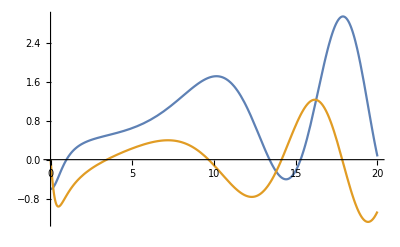

1/5

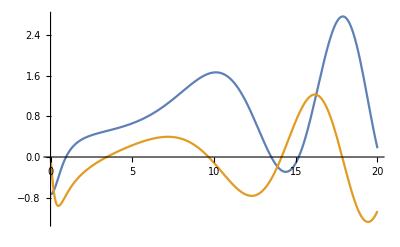

3/10

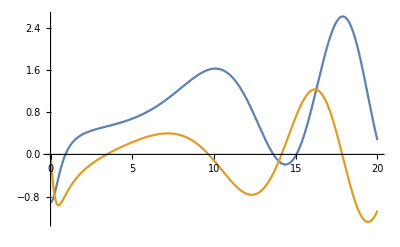

2/5

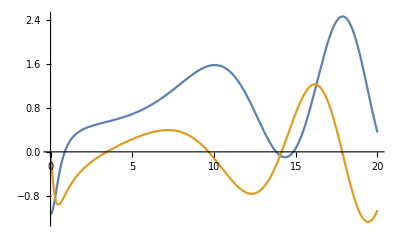

1/2

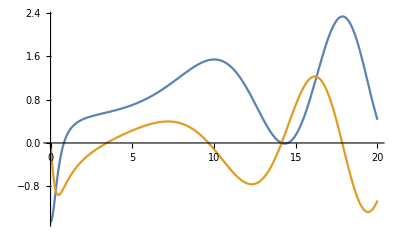

3/5

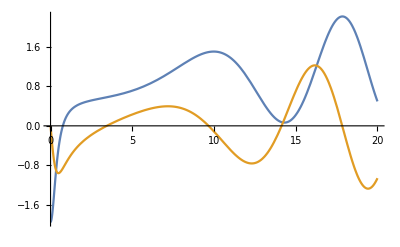

7/10

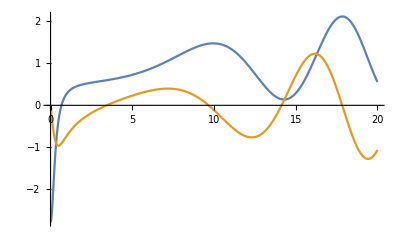

```mathematica
xval=1/10

realZeta=Re[(Zeta[x+I*t]+Zeta[x-I*t])/2]
imZeta=Re[(Zeta[x+I*t]-Zeta[x-I*t])/(2I)]
zetaModSqr=Re[Zeta[x+I*t]Zeta[x-I*t]]

xval
Plot[{Re[realZeta/.x->xval],Re[imZeta/.x->1/2]},{t,0,20}]
xval=xval+1/10
Plot[{Re[realZeta/.x->xval],Re[imZeta/.x->1/2]},{t,0,20}]
xval=xval+1/10
Plot[{Re[realZeta/.x->xval],Re[imZeta/.x->1/2]},{t,0,20}]
xval=xval+1/10
Plot[{Re[realZeta/.x->xval],Re[imZeta/.x->1/2]},{t,0,20}]
xval=xval+1/10
Plot[{Re[realZeta/.x->xval],Re[imZeta/.x->1/2]},{t,0,20}]
xval=xval+1/10
Plot[{Re[realZeta/.x->xval],Re[imZeta/.x->1/2]},{t,0,20}]
xval=xval+1/10
Plot[{Re[realZeta/.x->xval],Re[imZeta/.x->1/2]},{t,0,20}]
```

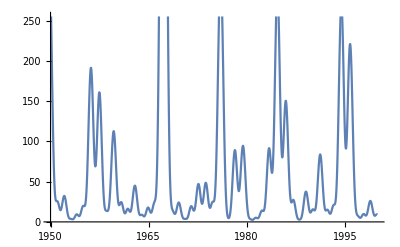

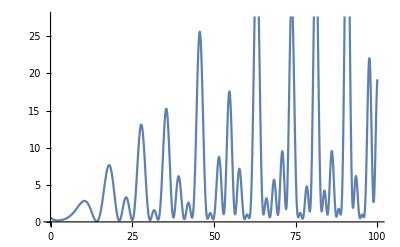

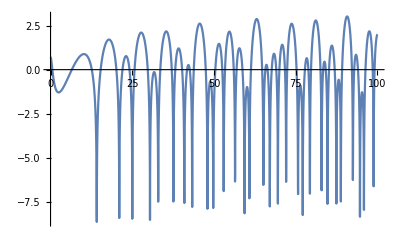

```mathematica
Plot[realZeta^2+imZeta^2/.x->2/10,{t,1950,2000}]
Plot[zetaModSqr/.x->2/10,{t,0,100}]
Plot[Log[zetaModSqr/.x->49/100],{t,0,100}]
```

```mathematica
zetaModSqr
FindRoot[%/.x->2/10,{t,14}]
```

Re(x-ⅈ t ⅈ t+x)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

{t→14.1263}

```mathematica
zetaModSqr/.x->2/10/.t->14.1263
```

0.072534

```mathematica
myZeta=( (1-2^(1-z))Gamma[z])^(-1)Integrate[t^(z-1)/(Exp[t]+1),{t,0,Infinity}]
```

ConditionalExpression[(2^-z (2^z-2) z)/(1-2^(1-z)),Re(z)>0]

```mathematica
myZeta//FullSimplify
```

ConditionalExpression[z,Re(z)>0]

```mathematica
Integrate[t^((1/2+I*14.1263)-1)/(Exp[t]+1),{t,0,Infinity}]
```

-8.67272×10^-12+2.99247×10^-12 ⅈ

```mathematica
meter=1/((1+Exp[rootP*Exp[y]])(1+Exp[rootP*Exp[-y]]))
FourierTransform[meter,y,t]
```

1/((ⅇ^(rootP ⅇ^-y)+1) (ⅇ^(rootP ⅇ^y)+1))

ℱ_y[1/((ⅇ^(rootP ⅇ^-y)+1) (ⅇ^(rootP ⅇ^y)+1))](t)

```mathematica
meter*(rootP^2)^(sigma-1)
%/.rootP->Sqrt[p]//Simplify
Integrate[%,{p,0,Infinity},Assumptions->0<sigma<1&&y∈Reals]
```

((rootP^2)^(σ-1))/((ⅇ^(rootP ⅇ^-y)+1) (ⅇ^(rootP ⅇ^y)+1))

p^(σ-1)/((ⅇ^(√p ⅇ^-y)+1) (ⅇ^(√p ⅇ^y)+1))

Integrate[p^(σ-1)/((ⅇ^(√p ⅇ^-y)+1) (ⅇ^(√p ⅇ^y)+1)),{p,0,∞},Assumptions→0<σ<1∧y∈ℝ]

```mathematica
meter=1/((1+Exp[rootP*Exp[y]])(1+Exp[rootP*Exp[-y]]))
Series[%,{rootP,0,2}]//Normal
FourierTransform[%,y,t]
```

1/((ⅇ^(rootP ⅇ^-y)+1) (ⅇ^(rootP ⅇ^y)+1))

rootP^2/16-1/8 rootP ⅇ^-y (ⅇ^(2 y)+1)+1/4

0

```mathematica
FourierTransform[Exp[I*y],y,t]
```

√(2 π) t+1